```mathematica
SetDirectory["/Users/olivier/Documents/HMM_Project"]
```

PC du boulot

```mathematica
$MachineID
```

6202-75065-80383

```mathematica
SetDirectory["C:\\Users\\ocroissant\\Documents\\Projet X\\HMM_project"]
```

C:\Users\ocroissant\Documents\Projet X\HMM_project

PC de la Maison

```mathematica
SetDirectory["C:/Users/olivier/Documents/Personel/Mathematica/Projet X"]
```

## lecture des fichier de données

#### Fonction de base : TableExtract, gestion du Directory MarketDataDirectory

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
(* une fonction pratique pour convertir les nom de colonne Excel en entier *)
```

```mathematica
LX[l_]:=Switch[l,"A",1,"B",2,"C",3,"D",4,"E",5,"F",6,"G",7,"H",8,"I",9,"J",10,"K",11,"L",12,"M",13,"N",14,"O",15,"P",16,"Q",17,"R",18,"S",19,"T",20,"U",21,"V",22,"W",23,"X",24,"Y",25,"Z",26,"AA",27,"AB",28,"AC",29,"AD",30,"AE",31,"AF",32,"AG",33,"AH",34,"AI",35,"AJ",36,"AK",37,"AL",38,"AM",39,"AN",40,"AO",41,"AP",42,"AQ",43,"AR",44,"AS",45,"AT",46,"AU",47,"AV",48,"AW",49,"AX",50,"AY",51,"AZ",52,"BA",53,"BB",54,"BC",55,"BD",56,"BE",57,"BF",58,"BG",59,"BH",60,"BI",61]
```

```mathematica
(* fonction de base pour extraire des données a partir d'excel *)
```

```mathematica
TableExtract[sps_,col1_,row1_,col2_,row2_]:=Module[{nbrow=row2-row1+1,nbcol=col2-col1+1,res,i,j},
res=Table[Table[ 0,{i,1,nbcol}],{j,1,nbrow}];
Do[res[[j+1,i+1]]=sps[[row1+j,col1+i]],{i,0,nbcol-1},{j,0,nbrow-1}];
 res]
```

```mathematica
(* pour qu'une matrice ait l'air d'un vecteur, lorsque ce n'est qu'un vecteur *)
```

```mathematica
TableExtractF[sps_,col1_,row1_,col2_,row2_]:=Module[{tab=TableExtract[sps,col1,row1,col2,row2],i},
If[Length[tab[[1]]]==1,Table[tab[[i,1]],{i,1,Length[tab]}],tab]]
```

```mathematica
$MachineID
```

6202-29516-23506

```mathematica
SetDirectory[$UserDocumentsDirectory]
```

/Users/croissantolivier/Documents

```mathematica
Directory[]
```

/Users/croissantolivier

```mathematica
If[($OperatingSystem=="Windows"),
Switch[$MachineID,
"6202-75065-80383",
MarketDataDirectory="C:\\Users\\ocroissant\\Documents\\Projet X\\HMM_project",
"6102-25062-85982",
MarketDataDirectory="C:\\Documents and Settings\\Olivier\\Documents\\My Bureau\\HMM_project",
"6239-65596-61921",
MarketDataDirectory="C:\\Users\\Olivier\\Documents\\HMM_project",
"6202-29516-23506",
MarketDataDirectory="C:\\Users\\olivier\\Documents\\Personel\\Mathematica\\Projet X"
],
Switch[$MachineID,
"5116-90412-58665",
MarketDataDirectory="/Users/croissantolivier/Documents/HMM_Project",
"5100-90230-55947",
MarketDataDirectory="/Users/olivier/Documents/HMM_Project"
]];
```

```mathematica
$MachineID
```

6202-75065-80383

```mathematica
MarketDataDirectory
```

MarketDataDirectory

```mathematica
SetDirectory[MarketDataDirectory]
```

C:\Users\ocroissant\Documents\Projet X\HMM_project

```mathematica
FileNames[FileNameJoin[{"/Users/croissantolivier/Documents/HMM_Project","*"}]]
```

{/Users/croissantolivier/Documents/HMM_Project/.DS_Store,/Users/croissantolivier/Documents/HMM_Project/HMM.nb,/Users/croissantolivier/Documents/HMM_Project/SP_Vix_DailyPriceHistory.xls,/Users/croissantolivier/Documents/HMM_Project/vixcurrent.csv}

#### Import des données de SP_Vix _DailyPriceHistory

```mathematica
aa=Import["SP_Vix_DailyPriceHistory.xls"];
```

```mathematica
Length[aa]
```

1

```mathematica
Length[aa[[1]]]
```

6724

```mathematica
aa[[1,6]]
```

{{1986,1,2,0,0,0.},N/A,N/A,209.59,N/A,N/A,N/A,N/A,18.07,N/A}

```mathematica
SPXbrut=TableExtractF[aa[[1]],LX["D"],6,LX["D"],6711] ;
```

```mathematica
DateSPXbrut=TableExtractF[aa[[1]],LX["A"],6,LX["A"],6711] ;
```

```mathematica
VIXbrut=TableExtractF[aa[[1]],LX["H"],1017,LX["H"],6711] ;
```

```mathematica
DateVIXbrut=TableExtractF[aa[[1]],LX["A"],1017,LX["A"],6711] ;
```

```mathematica
BXMbrut=TableExtractF[aa[[1]],LX["B"],130,LX["B"],6711] ;
```

```mathematica
DateBXMbrut=TableExtractF[aa[[1]],LX["A"],130,LX["A"],6711] ;
```

```mathematica
VXObrut=TableExtractF[aa[[1]],LX["I"],6,LX["I"],6711] ;
```

```mathematica
DateVXObrut=TableExtractF[aa[[1]],LX["A"],6,LX["A"],6711] ;
```

```mathematica
OVXbrut=TableExtractF[aa[[1]],LX["J"],5392,LX["J"],6711] ;
```

```mathematica
DateOVXbrut=TableExtractF[aa[[1]],LX["A"],5392,LX["A"],6711] ;
```

```mathematica
VIX={};DateVIX={};
Do[If[NumberQ[VIXbrut[[i]]],
VIX=Append[VIX,VIXbrut[[i]]];
DateVIX=Append[DateVIX,DateVIXbrut[[i]]];i+=1;
],{i,1,Length[VIXbrut]}];
```

```mathematica
SPX={};DateSPX={};
Do[If[NumberQ[SPXbrut[[i]]],
SPX=Append[SPX,SPXbrut[[i]]];
DateSPX=Append[DateSPX,DateSPXbrut[[i]]];i+=1;
],{i,1,Length[SPXbrut]}];
```

```mathematica
BXM={};DateBXM={};
Do[If[NumberQ[BXMbrut[[i]]],
BXM=Append[BXM,BXMbrut[[i]]];
DateBXM=Append[DateBXM,DateBXMbrut[[i]]];i+=1;
],{i,1,Length[BXMbrut]}];
```

```mathematica
VXO={};DateVXO={};
Do[If[NumberQ[VXObrut[[i]]],
VXO=Append[VXO,VXObrut[[i]]];
DateVXO=Append[DateVXO,DateVXObrut[[i]]];i+=1;
],{i,1,Length[VXObrut]}];
```

```mathematica
OVX={};DateOVX={};
Do[If[NumberQ[OVXbrut[[i]]],
OVX=Append[OVX,OVXbrut[[i]]];
DateOVX=Append[DateOVX,DateOVXbrut[[i]]];i+=1;
],{i,1,Length[OVXbrut]}];
```

```mathematica
SPX[[1;;10]]
```

{209.59,210.88,210.65,213.8,207.97,206.11,205.96,206.72,206.64,208.26}

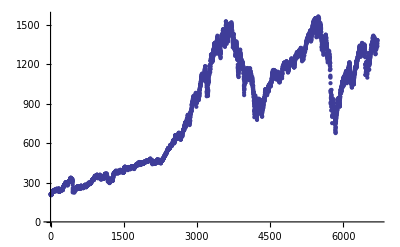

```mathematica
ListPlot[SPX]
```

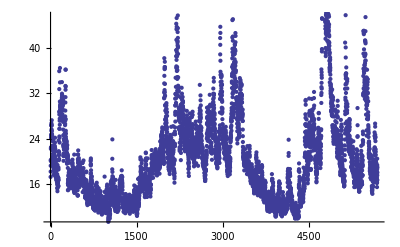

```mathematica
ListPlot[VIX]
```

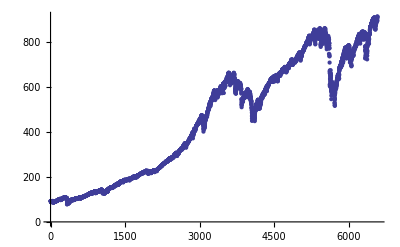

```mathematica
ListPlot[BXM]
```

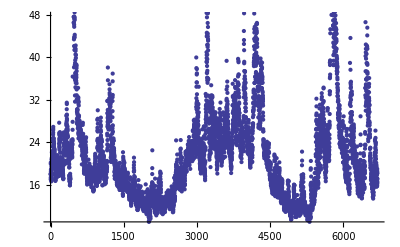

```mathematica
ListPlot[VXO]
```

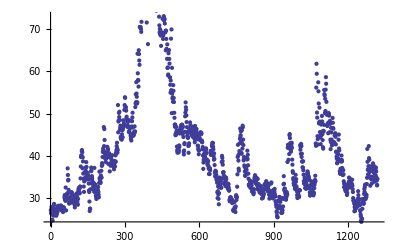

```mathematica
ListPlot[OVX]
```

Nombre de dimension cachées :  HiddenDimensionNb

Propabilité de transition du secteur caché : A[[i, j]]

probabilité initiale de la variable cachée : pi[[i]]

Probabilité d' observation Conditionellement a un etat caché : p[i, xt, theta]

#### Import des données de Datas Normalized

```mathematica
bb=Import["Datas_Normalized2.xls"];
```

```mathematica
DataBrut=Table[0,{i,1,20}];
```

```mathematica
DataBrut[[1]]={"EUR,SX5E","SX5E",TableExtractF[bb[[1]],LX["B"],4,LX["C"],3856] };
DataBrut[[2]]={"EUR VIX","V2X",TableExtractF[bb[[1]],LX["E"],4,LX["F"],3856] };
DataBrut[[3]]={"US SPX500","SPXT",TableExtractF[bb[[1]],LX["H"],4,LX["I"],3856] };
DataBrut[[4]]={"US,VIX","VIX",TableExtractF[bb[[1]],LX["K"],4,LX["L"],3856] };
DataBrut[[5]]={"GSCI Petrole","SPGSCLTR",TableExtractF[bb[[1]],LX["N"],4,LX["O"],3856] };
DataBrut[[6]]={"GSCI Or","SPGSGCTR",TableExtractF[bb[[1]],LX["Q"],4,LX["R"],3856] };
DataBrut[[7]]={"EUR/USD","EURUSD",TableExtractF[bb[[1]],LX["T"],4,LX["U"],3856] };
DataBrut[[8]]={"JPY/EUR","JPYEUR",TableExtractF[bb[[1]],LX["W"],4,LX["X"],3856] };
DataBrut[[9]]={"EUR Tenor 1Y","EUSA1",TableExtractF[bb[[1]],LX["Z"],4,LX["AA"],3856] };
DataBrut[[10]]={"EUR Tenor 2Y","EUSA2",TableExtractF[bb[[1]],LX["AC"],4,LX["AD"],3856] };
DataBrut[[11]]={"EUR Tenor 5Y","EUSA5",TableExtractF[bb[[1]],LX["AF"],4,LX["AG"],3856] };
DataBrut[[12]]={"EUR Tenor 10Y","EUSA10",TableExtractF[bb[[1]],LX["AI"],4,LX["AJ"],3856] };
DataBrut[[13]]={"US Tenor 1Y","USSW1",TableExtractF[bb[[1]],LX["AL"],4,LX["AM"],3856] };
DataBrut[[14]]={"US Tenor 2Y","USSW2",TableExtractF[bb[[1]],LX["AO"],4,LX["AP"],3856] };
DataBrut[[15]]={"US Tenor 5Y","USSW5",TableExtractF[bb[[1]],LX["AR"],4,LX["AS"],3856] };
DataBrut[[16]]={"US Tenor 10Y","USSW10",TableExtractF[bb[[1]],LX["AU"],4,LX["AV"],3856] };
DataBrut[[17]]={"ITraXX Main","ITRXEBE",TableExtractF[bb[[1]],LX["AX"],4,LX["AY"],2429] };
DataBrut[[18]]={"ITraXX Cross Over","ITRXEXE",TableExtractF[bb[[1]],LX["BA"],4,LX["BB"],2429] };
DataBrut[[19]]={"ITraXX Main USD","ITRXX",TableExtractF[bb[[1]],LX["BD"],4,LX["BE"],2598] };
DataBrut[[20]]={"ItraXX HY USD","IBOXHYSE",TableExtractF[bb[[1]],LX["BG"],4,LX["BH"],1218] };
```

```mathematica
DataBrut[[20,2]]==
```

IBOXHYSE

```mathematica
GetHistory[ticker_]:=Switch[ticker,
DataBrut[[1,2]], Transpose[DataBrut[[1,3]]][[2]],
DataBrut[[2,2]], Transpose[DataBrut[[2,3]]][[2]],
DataBrut[[3,2]], Transpose[DataBrut[[3,3]]][[2]],
DataBrut[[4,2]], Transpose[DataBrut[[4,3]]][[2]],
DataBrut[[5,2]], Transpose[DataBrut[[5,3]]][[2]],
DataBrut[[6,2]], Transpose[DataBrut[[6,3]]][[2]],
DataBrut[[7,2]], Transpose[DataBrut[[7,3]]][[2]],
DataBrut[[8,2]], Transpose[DataBrut[[8,3]]][[2]],
DataBrut[[9,2]], Transpose[DataBrut[[9,3]]][[2]],
DataBrut[[10,2]], Transpose[DataBrut[[10,3]]][[2]],
DataBrut[[11,2]], Transpose[DataBrut[[11,3]]][[2]],
DataBrut[[12,2]], Transpose[DataBrut[[12,3]]][[2]],
DataBrut[[13,2]], Transpose[DataBrut[[13,3]]][[2]],
DataBrut[[14,2]], Transpose[DataBrut[[14,3]]][[2]],
DataBrut[[15,2]], Transpose[DataBrut[[15,3]]][[2]],
DataBrut[[16,2]], Transpose[DataBrut[[16,3]]][[2]],
DataBrut[[17,2]], Transpose[DataBrut[[17,3]]][[2]],
DataBrut[[18,2]], Transpose[DataBrut[[18,3]]][[2]],
DataBrut[[19,2]], Transpose[DataBrut[[19,3]]][[2]],
DataBrut[[20,2]], Transpose[DataBrut[[20,3]]][[2]]
]
```

```mathematica
GetHistory["ITRXEBE"];
```

```mathematica
GetHistory[ticker1_,n_Integer]:=Module[{h1=GetHistory[ticker1],l1,l},
l1=Length[h1];l=Min[l1,n];Reverse[h1[[1;;l]]]]
```

```mathematica
GetHistory[ticker1_,n_Integer,p_Integer]:=Module[{h1=GetHistory[ticker1],q1,q2,l},
l=Length[h1];q1=Min[l,n+p];q2=Min[l,p+1];Reverse[h1[[q2;;q1]]]]
```

```mathematica
GetHistory[ticker1_,ticker2_]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],l1,l2,l},
l1=Length[h1];l2=Length[h2];l=Min[l1,l2];Transpose[{h1[[1;;l]],h2[[1;;l]]}]]
```

```mathematica
GetHistory[ticker1_,ticker2_,n_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],l1,l2,l},
l1=Length[h1];l2=Length[h2];l=Min[l1,l2,n];Reverse[Transpose[{h1[[1;;l]],h2[[1;;l]]}]]]
```

```mathematica
GetHistory[ticker1_,ticker2_,n_Integer,p_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],l1,l2,q1,q2},
l1=Length[h1];l2=Length[h2];q1=Min[l1,l2,n+p];q2=Min[l1,l2,p+1];Reverse[Transpose[{h1[[q2;;q1]],h2[[q2;;q1]]}]]]
```

```mathematica
GetHistory[ticker1_,ticker2_,ticker3_,n_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],h3=GetHistory[ticker3],l1,l2,l3,l},
l1=Length[h1];l2=Length[h2];l3=Length[h3];l=Min[l1,l2,l3,n];Reverse[Transpose[{h1[[1;;l]],h2[[1;;l]],h3[[1;;l]]}]]]
```

```mathematica
GetHistory[ticker1_,ticker2_,ticker3_,n_Integer,p_Integer]:=Module[{h1=GetHistory[ticker1],h2=GetHistory[ticker2],h3=GetHistory[ticker3],l1,l2,l3,q1,q2,},
l1=Length[h1];l2=Length[h2];l3=Length[h3];q1=Min[l1,l2,l3,n+p];q2=Min[l1,l2,l3,p+1];Reverse[Transpose[{h1[[q2;;q1]],h2[[q2;;q1]],h3[[q2;;q1]]}]]]
```

```mathematica
GetHistory["ITRXEBE",20]
```

{96.912,97.422,98.022,94.083,94.133,93.41,89.174,99.467,100.014,97.505,97.759,99.427,102.294,103.884,98.75,98.747,100.706,97.055,98.008,100.628}

```mathematica
GetHistory["ITRXEBE",10,10]
```

{96.912,97.422,98.022,94.083,94.133,93.41,89.174,99.467,100.014,97.505}

```mathematica
GetHistory["ITRXEBE","ITRXX",20]
```

{{96.912,76.042},{97.422,77.712},{98.022,77.056},{94.083,74.753},{94.133,73.024},{93.41,69.49},{89.174,69.896},{99.467,79.988},{100.014,80.325},{97.505,78.875},{97.759,79.701},{99.427,79.638},{102.294,80.897},{103.884,82.07},{98.75,79.738},{98.747,79.661},{100.706,80.9},{97.055,79.415},{98.008,82.517},{100.628,84.517}}

```mathematica
GetHistory["ITRXEBE","ITRXX",10,10]
```

{{96.912,76.042},{97.422,77.712},{98.022,77.056},{94.083,74.753},{94.133,73.024},{93.41,69.49},{89.174,69.896},{99.467,79.988},{100.014,80.325},{97.505,78.875}}

```mathematica
GetHistory["ITRXEBE","ITRXX","SPXT",20]
```

{{110.994,86.369,2660.7},{118.318,90.15,2630.05},{115.432,88.459,2657.76},{117.759,89.619,2659.55},{118.292,89.913,2655.84},{116.168,89.408,2670.85},{116.298,89.464,2669.37},{113.551,87.265,2673.77},{111.674,86.113,2676.6},{110.715,85.952,2678.77},{112.934,86.76,2676.21},{112.907,86.72,2676.21},{110.861,85.197,2696.26},{111.056,87.6,2662.94},{114.518,88.39,2646.75},{112.931,86.353,2670.36},{113.573,90.217,2621.46},{122.529,89.526,2637.89},{116.984,87.272,2672.11},{116.292,88.033,2669.92}}

```mathematica
GetHistory["ITRXEBE","ITRXX","SPXT",10,10]
```

{{110.994,86.369,2660.7},{118.318,90.15,2630.05},{115.432,88.459,2657.76},{117.759,89.619,2659.55},{118.292,89.913,2655.84},{116.168,89.408,2670.85},{116.298,89.464,2669.37},{113.551,87.265,2673.77},{111.674,86.113,2676.6},{110.715,85.952,2678.77}}

## Fonctions Specifiques

### Fonctions auxiliaires

```mathematica
biSymetricToFlatIndex[i1_,j1_,n_]:=Module[{i,j},If[i1>=j1,i=i1;j=j1,i=j1;j=i1];If[i>2,Sum[k,{k,1,i-2}]+j,j]]
```

```mathematica
FlatToSymetricIndex[k_,n_]:=Module[{eps=k,i=1,j=1},While[eps>(i-1),eps=eps-(i-1);i=i+1];j=eps;{i,j}]
```

```mathematica
Module[{n=3},Do[Do[Print[biSymetricToFlatIndex[i,j,n]],{j,1,i-1}],{i,1,n}]]
```

1

2

3

```mathematica
Module[{n=3,k},Do[Do[k=biSymetricToFlatIndex[i,j,n];
Print[{i,j}," k=",k," => ",FlatToSymetricIndex[k,n]],{j,1,i-1}],{i,1,n}]]
```

{2,1} k=1 => {2,1}

{3,1} k=2 => {3,1}

{3,2} k=3 => {3,2}

### Densité gaussiennes

```mathematica
SPX[[2;;10]]
```

{210.88,210.65,213.8,207.97,206.11,205.96,206.72,206.64,208.26}

```mathematica
PDF[MultinormalDistribution[{μ1,μ2,μ3},{{σ1^2,ρ12 σ1 σ2,ρ13 σ1 σ3},{ρ12 σ1 σ2,σ2^2,ρ23 σ2 σ3},{ρ13 σ1 σ3,ρ23 σ2 σ3,σ3^2}}],{x1,x2,x3}]
```

ⅇ^(1/2 (-((x3-μ3) (-x3 σ1 σ2+μ3 σ1 σ2+x3 ρ12^2 σ1 σ2-μ3 ρ12^2 σ1 σ2-x2 ρ12 ρ13 σ1 σ3+μ2 ρ12 ρ13 σ1 σ3+x2 ρ23 σ1 σ3-μ2 ρ23 σ1 σ3+x1 ρ13 σ2 σ3-μ1 ρ13 σ2 σ3-x1 ρ12 ρ23 σ2 σ3+μ1 ρ12 ρ23 σ2 σ3))/((-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2) σ1 σ2 σ3^2)-((x2-μ2) (-x3 ρ12 ρ13 σ1 σ2+μ3 ρ12 ρ13 σ1 σ2+x3 ρ23 σ1 σ2-μ3 ρ23 σ1 σ2-x2 σ1 σ3+μ2 σ1 σ3+x2 ρ13^2 σ1 σ3-μ2 ρ13^2 σ1 σ3+x1 ρ12 σ2 σ3-μ1 ρ12 σ2 σ3-x1 ρ13 ρ23 σ2 σ3+μ1 ρ13 ρ23 σ2 σ3))/((-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2) σ1 σ2^2 σ3)-((x1-μ1) (x3 ρ13 σ1 σ2-μ3 ρ13 σ1 σ2-x3 ρ12 ρ23 σ1 σ2+μ3 ρ12 ρ23 σ1 σ2+x2 ρ12 σ1 σ3-μ2 ρ12 σ1 σ3-x2 ρ13 ρ23 σ1 σ3+μ2 ρ13 ρ23 σ1 σ3-x1 σ2 σ3+μ1 σ2 σ3+x1 ρ23^2 σ2 σ3-μ1 ρ23^2 σ2 σ3))/((-1+ρ12^2+ρ13^2-2 ρ12 ρ13 ρ23+ρ23^2) σ1^2 σ2 σ3)))/(2 √2 π^(3/2) √(σ1 σ2 σ3 (σ1 σ2 σ3-ρ12^2 σ1 σ2 σ3-ρ13^2 σ1 σ2 σ3+2 ρ12 ρ13 ρ23 σ1 σ2 σ3-ρ23^2 σ1 σ2 σ3)))

```mathematica
3
```

```mathematica
NormDens[x0_,σ_,x_]:=(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2 π) σ)
```

```mathematica
LogNormDens[x0_,σ_,x_]:=-(x-x0)^2/(2 σ^2)-Log[√(2 π) σ]
```

```mathematica
BivariateNormDens[x_,y_,μ1_,μ2_,σ1_,σ2_,ρ_]:=If[ρ==1 && (μ1-x)/σ1==(μ2-y)/σ2,NormDens[μ1,σ1,x],If[ρ≠1,ExpR[(-((x-μ1)/σ1)^2-((y-μ2)/σ2)^2+2 ((x-μ1)(y-μ2))/(σ1 σ2) ρ)/(2 (1-ρ^2))]/(2 π √(1- ρ^2)σ1 σ2),0]]
```

```mathematica
LogBivariateNormDens[x_,y_,μ1_,μ2_,σ1_,σ2_,ρ_]:=
If[ρ≠1 &&ρ≠-1,(-((x-μ1)/σ1)^2-((y-μ2)/σ2)^2+2 ((x-μ1)(y-μ2))/(σ1 σ2) ρ)/(2 (1-ρ^2))-Log[2 π σ1 σ2 √(1- ρ^2)],
If[ρ==1 && (μ1-x)/σ1==(μ2-y)/σ2,LogNormDens[μ1,σ1,x],
If[ρ==-1 && (μ1-x)/σ1==(μ2-y)/σ2,LogNormDens[μ1,σ1,x],0]]]
```

```mathematica
TrivariateNormDens[x_,y_,z_,μ1_,μ2_,μ3_,σ1_,σ2_,σ3_,ρ12_,ρ13_,ρ23_]:=
If[ρ12==1 && (μ1-x)/σ1==(μ2-y)/σ2,BivariateNormDens[x,z,μ1,μ3,σ1,σ3,ρ13],
If[ρ13==1 && (μ1-x)/σ1==(μ3-y)/σ3,BivariateNormDens[x,y,μ1,μ2,σ1,σ2,ρ12],
If[ρ12≠1&& ρ13≠1,ExpR[(-((x-μ1)/σ1)^2-((y-μ2)/σ2)^2+2 ((x-μ1)(y-μ2))/(σ1 σ2) ρ12)/(2 (1-ρ12^2))]/(2 π √(1- ρ12^2)σ1 σ2),0]]]
```

```mathematica
MultivariateNormDens[μ_,σ_,ρ_,x_]:=Module[{NbDim=Length[μ],Σ},
Σ=Table[If[i==j,σ[[i]]^2,ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}];
PDF[MultinormalDistribution[μ,Σ],x]]
```

```mathematica
LogMultivariateNormDens[μ_,σ_,ρ_,x_]:=Module[{NbDim=Length[μ],Σ},
Σ=Table[If[i==j,σ[[i]]^2,ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}];
Log[PDF[MultinormalDistribution[μ,Σ],x]]]
```

```mathematica
MultivariateΣ[σ_,ρ_]:=Module[{NbDim=Length[σ],Σ},
Σ=Table[If[i==j,σ[[i]]^2,ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}]]
```

```mathematica
MultivariateΣ[{σ1,σ2,σ3},{ρ1,ρ2,ρ3}]//MatrixForm
```

(σ1^2 | ρ1 σ1 σ2 | ρ2 σ1 σ3
ρ1 σ1 σ2 | σ2^2 | ρ3 σ2 σ3
ρ2 σ1 σ3 | ρ3 σ2 σ3 | σ3^2)

```mathematica
Eigenvalues[MultivariateΣ[{0.2,0.3,0.4},{0.3,0.3,0.4},{0.05,-0.05,0.05}]]
```

{0.166554,0.105,0.0684465}

```mathematica
LogMultivariateNormDens[{0.2,0.3,0.4},{0.3,0.3,0.4},{0.05,-0.05,0.05},{0.05,-0.05,0.05}]
```

-0.561616

```mathematica
LogMultivariateNormDens[μ_,σ_,ρ_,x_]:=Module[{NbDim,Σ},
NbDim=Length[μ];
Σ=Table[If[i==j,σ[[i]]*σ[[i]],ρ[[biSymetricToFlatIndex[i,j,NbDim]]]σ[[i]] σ[[j]]],{i,1,NbDim},{j,1,NbDim}];
-0.5((Inverse[Σ].(x-μ)).(x-μ)+Log[Det[Σ]]+Length[Σ]1.837877066409345)]
```

### ExpR, LogR, LogSumExpR , MNormalize, FNormalize

```mathematica
LogR[a_]:=If[a==0, -1.23456789 10^99, Log[a]]
```

```mathematica
Attributes[LogR]={Listable}
```

{Listable}

```mathematica
ExpR[a_]:=If[a<-10^(3),1 10^(-99),Exp[a]]
```

```mathematica
Attributes[ExpR]={Listable}
```

{Listable}

```mathematica
LogSumExp1[vec_]:=Log[Plus@@(Exp[vec])]
```

```mathematica
LogSumExp[vec_]:=Module[{biggest=Max[vec],vecp,sum, logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
vecp=SetPrecision[vec-biggest,nbdecimal];
sum=Sum[If[vecp[[i]]<logCutoff,0.0,ExpR[vecp[[i]]]],{i,1,Length[vec]}];
LogR[sum]+biggest]
```

```mathematica
LogSumExp2[vec_]:=Module[{biggest=Max[vec],vecp,sum, logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
vecp=SetPrecision[vec-biggest,nbdecimal];
sum=Sum[If[vecp[[i,j]]<logCutoff,0.0,ExpR[vecp[[i,j]]]],{i,1,Length[vec]},{j,1,Length[vec]}];LogR[sum]+biggest]
```

```mathematica
LogSumExp[{-1.25,-25,-3000000,-2}]
```

-0.863129

```mathematica
LogSumExp3[{-1.25,-25.,-3000000,-2}]
```

-0.863129

```mathematica
LogSumExpAux[vec_]:=Module[{biggest=Max[vec],vecp,sum,logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
vecp=SetPrecision[vec-biggest,nbdecimal];
sum=∑_(i=1)^Length[vec] If[vecp⟦i⟧<logCutoff,0.0,ExpR[vecp⟦i⟧]];
LogR[sum]+biggest]
```

```mathematica
TensorLogSumExp[tensor_]:=Module[{rank=TensorRank[tensor],dims=Dimensions[tensor]},Switch[rank,
1,LogSumExpAux[tensor],
2,Table[LogSumExpAux[Table[tensor[[i,j]],{i,1,dims[[1]]}]],{j,1,dims[[2]]}],
3,Table[LogSumExpAux[Table[tensor[[i,j,k]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]}],
4,Table[LogSumExpAux[Table[tensor[[i,j,k,l]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}],
5,Table[LogSumExpAux[Table[tensor[[i,j,k,l,m]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]}],
6,Table[LogSumExpAux[Table[tensor[[i,j,k,l,m,o]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]},{o,1,dims[[6]]}],
7,Table[LogSumExpAux[Table[tensor[[i,j,k,l,m,o,p]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]},{o,1,dims[[6]]},{p,1,dims[[7]]}],
8,Table[LogSumExpAux[Table[tensor[[i,j,k,l,m,o,p,q]],{i,1,dims[[1]]}]],{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]},{o,1,dims[[6]]},{p,1,dims[[7]]},{q,1,dims[[8]]}]
]]
```

```mathematica
MNormalize[M_]:=Module[{HDim=Length[Dimensions[M]]},Switch[HDim,
1,M/(Plus@@M),
2,Table[M⟦i⟧/(Plus@@M⟦i⟧),{i,1,Dimensions[M][[1]]}],
3,Table[M⟦i,j⟧/(Plus@@M⟦i,j⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]}],
4,Table[M⟦i,j,k⟧/(Plus@@M⟦i,j,k⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]}],
5,Table[M⟦i,j,k,l⟧/(Plus@@M⟦i,j,k,l⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]}],
6,Table[M⟦i,j,k,l,m⟧/(Plus@@M⟦i,j,k,l,m⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]},{m,1,Dimensions[M][[5]]}],
7,Table[M⟦i,j,k,l,m,n⟧/(Plus@@M⟦i,j,k,l,m,n⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]},{m,1,Dimensions[M][[5]]},{n,1,Dimensions[M][[6]]}],
8,Table[M⟦i,j,k,l,m,n,o⟧/(Plus@@M⟦i,j,k,l,m,n,o⟧),{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]},{m,1,Dimensions[M][[5]]},{n,1,Dimensions[M][[6]]},{o,1,Dimensions[M][[7]]}]
]]
```

```mathematica
MNormalizeLog[M_]:=Module[{HDim=Length[Dimensions[M]]},Switch[HDim,
1,M-LogSumExp[M],
2,Table[M⟦i⟧-LogSumExp[M⟦i⟧],{i,1,Length[M]}],
3,Table[M⟦i,j⟧-LogSumExp[M⟦i,j⟧],{i,1,Length[M]},{j,1,Length[M]}],
4,Table[M⟦i,j,k⟧-LogSumExp[M⟦i,j,k⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]}],
5,Table[M⟦i,j,k,l⟧-LogSumExp[M⟦i,j,k,l⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]},{l,1,Length[M]}],
6,Table[M⟦i,j,k,l,m⟧-LogSumExp[M⟦i,j,k,l,m⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]},{l,1,Length[M]},{m,1,Length[M]}],
7,Table[M⟦i,j,k,l,m,n⟧-LogSumExp[M⟦i,j,k,l,m,n⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]},{l,1,Length[M]},{m,1,Length[M]},{n,1,Length[M]}],
8,Table[M⟦i,j,k,l,m,n,o⟧-LogSumExp[M⟦i,j,k,l,m,n,o⟧],{i,1,Length[M]},{j,1,Length[M]},{k,1,Length[M]},{l,1,Length[M]},{m,1,Length[M]},{n,1,Length[M]},{o,1,Length[M]}]
]]
```

```mathematica
MNormalizeLog1[M_]:=Module[{HDim=Length[Dimensions[M]]},Switch[HDim,
1,Log[M]-Log[Plus@@M],
2,Table[LogR[M⟦i⟧]-LogR[Plus@@M⟦i⟧],{i,1,Dimensions[M][[1]]}],
3,Table[LogR[M⟦i,j⟧]-LogR[Plus@@M⟦i,j⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]}],
4,Table[LogR[M⟦i,j,k⟧]-LogR[Plus@@M⟦i,j,k⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]}],
5,Table[LogR[M⟦i,j,k,l⟧]-LogR[Plus@@M⟦i,j,k,l⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]}],
6,Table[LogR[M⟦i,j,k,l,m⟧]-LogR[Plus@@M⟦i,j,k,l,m⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]},{m,1,Dimensions[M][[5]]}],
7,Table[LogR[M⟦i,j,k,l,m,n⟧]-LogR[Plus@@M⟦i,j,k,l,m,n⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]},{m,1,Dimensions[M][[5]]},{n,1,Dimensions[M][[6]]}],
8,Table[LogR[M⟦i,j,k,l,m,n,o⟧]-LogR[Plus@@M⟦i,j,k,l,m,n,o⟧],{i,1,Dimensions[M][[1]]},{j,1,Dimensions[M][[2]]},{k,1,Dimensions[M][[3]]},{l,1,Dimensions[M][[4]]},{m,1,Dimensions[M][[5]]},{n,1,Dimensions[M][[6]]},{o,1,Dimensions[M][[7]]}]
]]
```

```mathematica
FNormalize[M_]:=Module[{HDim=Length[Dimensions[M]],norm,dims=Dimensions[M]},Switch[HDim,
1,norm=Sum[M[[i]],{i,1,dims[[1]]}];M/norm,
2,norm=Sum[M[[i,j]],{i,1,dims[[1]]},{j,1,dims[[2]]}];M/norm,
3,norm=Sum[M[[i,j,k]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}];M/norm,
4,norm=Sum[M[[i,j,k,l]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}];M/norm,
5,norm=Sum[M[[i,j,k,l,o]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]}];M/norm,
6,norm=Sum[M[[i,j,k,l,o,p]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]}];M/norm,
7,norm=Sum[M[[i,j,k,l,o,p,q]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]},{q,1,dims[[7]]}];M/norm,
8,norm=Sum[M[[i,j,k,l,o,p,q,r]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]},{q,1,dims[[7]]},{r,1,dims[[8]]}];M/norm
]]
```

```mathematica
FNormalizeLog[M_]:=Module[{HDim=Length[Dimensions[M]],norm,dims=Dimensions[M]},Switch[HDim,
1,norm=LogSumExp[Table[M[[i]],{i,1,dims[[1]]}]];ExpR[M-norm],
2,norm=Table[LogSumExp[Table[M[[i,j]],{j,1,dims[[2]]}]],{i,1,dims[[1]]}];
Table[ExpR[M[[i,j]]-norm[[i]]],{i,1,dims[[1]]},{j,1,dims[[2]]}],

3,norm=Table[LogSumExp[Table[M[[i,j,k]],{k,1,dims[[3]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]}];
Table[ExpR[M[[i,j,k]]-norm[[i,j]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}],

4,norm=Table[LogSumExp[Table[M[[i,j,k,l]],{l,1,dims[[4]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}];
Table[ExpR[M[[i,j,k,l]]-norm[[i,j,k]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}],

5,norm=Table[LogSumExp[Table[M[[i,j,k,l,o]],{o,1,dims[[5]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}];
Table[ExpR[M[[i,j,k,l,o]]-norm[[i,j,k,l]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]}],

6,norm=Table[LogSumExp[Table[M[[i,j,k,l,o,p]],{p,1,dims[[6]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]}];
Table[ExpR[M[[i,j,k,l,o,p]]-norm[[i,j,k,l,o]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]}],

7,norm=Table[LogSumExp[Table[M[[i,j,k,l,o,p,q]],{q,1,dims[[7]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]}];
Table[ExpR[M[[i,j,k,l,o,p,q]]-norm[[i,j,k,l,o,p]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]},{q,1,dims[[7]]}],

8,norm=Table[LogSumExp[Table[M[[i,j,k,l,o,p,q,r]],{r,1,dims[[8]]}]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]},{q,1,dims[[7]]}];
Table[ExpR[M[[i,j,k,l,o,p,q,r]]-norm[[i,j,k,l,o,p,q]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{o,1,dims[[5]]},{p,1,dims[[6]]},{q,1,dims[[7]]},{r,1,dims[[8]]}]
]]
```

### BuildMatrixFromLocalCliqueTensor

```mathematica
FromSparseToFlat[indexList_,dimList_,value_]:=Module[{v=Table[0,{j,1,Product[dimList[[i]],{i,1,Length[dimList]}]}]},v[[FromSparseToFlatIndex[indexList,dimList]]]=value;v]
```

```mathematica
FromSparseToFlatIndex[indexList_,dimList_]:=Sum[(indexList[[i]]-1) Product[dimList[[j]],{j,1,i-1}],{i,1,Length[dimList]}]+1
```

```mathematica
FromSparseToFlatIndex[{2,3},{2,3}]
```

6

```mathematica
FromSparseToFlat[{1,3},{2,3},7]
```

{0,0,0,0,7,0}

```mathematica
FromSparseToFlat[{2,1,1,1,1,1,1,1,1,1},{2,3,4,3,2,5,2,3,4,3},7]
```

```mathematica
FromFlatToSparseStateList[Index_,dimList_]:=Module[{Ndim=Length[dimList],base,indexList,quotient,remainder,currentIndex=Index-1,currentBase},
indexList=Table[0,{i,1,Ndim}];
Do[
{quotient,remainder}=QuotientRemainder[currentIndex,dimList[[i]]];
indexList[[i]]=remainder+1;
currentIndex=quotient;
,{i,1,Ndim-1}];
indexList[[Ndim]]=quotient+1;
indexList]
```

```mathematica
FromSparseToFlatIndex[{1,1,2},{2,3,4}]
```

7

```mathematica
FromFlatToSparseStateList[7,{2,3,4}]
```

```mathematica
CliqueTensorParcours
```

{1,1,2}

```mathematica
NextIndex[indexList_,dimList_]:=Module[{n=Length[dimList],Done=False,indexList2,i=1},
While[(Done==False)&& (i≤n),If[indexList[[i]]<dimList[[i]],Done=True,i++];
If[Done==True,indexList2=indexList;indexList2[[i]]=indexList2[[i]]+1;Do[indexList2[[j]]=1,{j,1,i-1}],indexList2=0]];indexList2]
```

```mathematica
II={2,3,2}
```

{2,3,2}

```mathematica
II=NextIndex[II,{2,3,4}]
```

{1,1,3}

CliqueTensor = {nodeList1, nodelist2, principalNode, tensor}

Le tensor est une distribution de probabilité pour principalNode  conditional to nodeList1e t nodelist2,

Contrainte : TensorRank[tensor] = Length[nodeList1] + Length[nodeList2] + 1

On connait les ditribution conditionnelles de tous les noeuds presents cité

Contrainte : Apply[Union, Table[CliqueTensorList[[i, 1]], {i, 1, Length[CliqueTensorList]}]] = Apply[Union, Table[CliqueTensorList[[i, 3]], {i, 1, Length[CliqueTensorList]}]]

On connait les ditribution conditionnelles de tous les noeuds passés cité

Contrainte : Apply[Union, Table[CliqueTensorList[[i, 2]], {i, 1, Length[CliqueTensorList]}]] = Apply[Union, Table[CliqueTensorList[[i, 3]], {i, 1, Length[CliqueTensorList]}]]

Il y a  consistence entre les dimensions des tenseurs pour les memes noeuds

```mathematica
Clear[CliqueProbability]
```

```mathematica
CheckCliqueDimensions[CliqueTensorList_]:=Print["Dimensions Clique=",Table[Dimensions[CliqueTensorList[[i,4]]],{i,1,Length[CliqueTensorList]}]]
```

```mathematica
CheckDimensionsClique[nodeList1_,nodeList2_,principalNode_,tensor_,globalNodeList_,dimList_]:=Module[{rank=TensorRank[tensor],indexList,nodeName,nodePosition,nodeState, dimtensor=Dimensions[tensor],dimattendue,dimdutensor},
(* on suppose que dimList sont la liste des dimensions attendue pour les neuds de  globalNodeList *)
(* on verifie *)
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList1[[j]]];(* je cherche seulement les etats concernés par nodeList1 *)
dimattendue=dimList[[nodePosition]];
dimdutensor=dimtensor[[j]]; 
Print["node:",nodeList1[[j]]," dim attendue",dimdutensor];
If[(dimattendue!=dimdutensor),Print["dims du tensor=",dimtensor];Print["dans le tenseur fourni en argument de CliqueProbability,dimattendue=",dimattendue " alors que dimdutensor=",dimdutensor , " pour la variable",principalNode," dans la dimension(t-1) associée a ", nodeList1[[j]] ]];
,{j,1,Length[nodeList1]}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList2[[j]]];
dimattendue=dimList[[nodePosition]];
dimdutensor=dimtensor[[j+Length[nodeList1]]]; 
Print["node:",nodeList2[[j]]," dim attendue",dimdutensor];
If[(dimattendue!=dimdutensor),Print["dims du tensor=",dimtensor];Print["dans le tenseur fourni en argument de CliqueProbability,dimattendue=",dimattendue " alors que dimdutensor=",dimdutensor , " pour la variable",principalNode," dans la dimension(t) associée a ", nodeList2[[j]] ]];
,{j,1,Length[nodeList2]}];
nodePosition=FindNodePosition[globalNodeList,principalNode];
dimattendue=dimList[[nodePosition]];
dimdutensor=dimtensor[[1+Length[nodeList1]+Length[nodeList2]]]; 
Print["node:",principalNode," dim attendue",dimdutensor];
If[(dimattendue!=dimdutensor),Print["dims du tensor=",dimtensor];Print["dans le tenseur fourni en argument de CliqueProbability,dimattendue=",dimattendue " alors que dimdutensor=",dimdutensor , " pour la variable",principalNode," dans la dimension associée a ", principalNode ]];
(* fin de la verification*)
]
```

```mathematica
CheckCliqueTensor[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList]},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
(* check des dims *)
dimtotale=Product[dimList[[i]],{i,1,nClique}];
Do[
Print["node principal :",CliqueTensorList[[i,3]]];
CheckDimensionsClique[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],nodeList,dimList],{i,1,nClique}];
Print["fin de la verification"];
]
```

```mathematica
CliqueProbability[nodeList1_,nodeList2_,principalNode_,tensor_,index1_,index2_,globalNodeList_,dimList_]:=Module[{rank=TensorRank[tensor],indexList,nodeName,nodePosition,nodeState,dimlistattendue},
(* on suppose que dimList sont la liste des dimensions attendue pour les neuds de  globalNodeList *)
indexList=Table[1,{i,1,rank}];dimlistattendue=indexList;
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList1[[j]]];(* je cherche seulement les etats concernés par nodeList1 *)
dimlistattendue[[j]]=dimList[[nodePosition]];
nodeState=index1[[nodePosition]];(* je le cherche ds index1 car c'est f(t-1) *)
indexList[[j]]=nodeState; (* je construit les etat associé aux nodelist1 *)
,{j,1,Length[nodeList1]}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList2[[j]]];
dimlistattendue[[j+Length[nodeList1]]]=dimList[[nodePosition]];
nodeState=index2[[nodePosition]];(* je le cherche ds index2 car c'est f(t) *)
indexList[[j+Length[nodeList1]]]=nodeState;(* je construit les etat associé aux nodelist2 *)
,{j,1,Length[nodeList2]}];
nodePosition=FindNodePosition[globalNodeList,principalNode];
dimlistattendue[[1+Length[nodeList1]+Length[nodeList2]]]=dimList[[nodePosition]];
nodeState=index2[[nodePosition]];(* je le cherche ds index2 car c'est f(t) *)
indexList[[1+Length[nodeList1]+Length[nodeList2]]]=nodeState; (* je construit l etat associé a principalNode *)
Apply[Part,Insert[indexList,tensor,1]] 
]
```

```mathematica
(* je vais chercher dans le tensor la valeur correspondante *)
(* je suppose donc que les dimensions de tensor sont compatible avec les dimensions traduite par globalNodeList *)
```

```mathematica
BuildMatrixFromLocalCliqueTensor[CliqueTensorList_]:=Module[{globalNodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
(* check des dims *)
dimtotale=Product[dimList[[i]],{i,1,nClique}];M=Table[0,{i,1,dimtotale},{j,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
index2=FromSparseToFlatIndex[CurrentSate2,dimList];
probalist=Table[CliqueProbability[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],CurrentSate1,CurrentSate2,globalNodeList,dimList],{i,1,nClique}];
M[[index1,index2]]=Product[probalist[[i]],{i,1,nClique}];
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
M]
```

```mathematica
CliqueTensorParcours[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];M=Table[0,{i,1,dimtotale},{j,1,dimtotale}];
Print["dimtotale=",dimtotale];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
Print["CurrentSate1=",CurrentSate1," index1=",index1];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
M]
```

```mathematica
FindNodePosition[globalNodeList_,nodeName_]:=Position[globalNodeList,nodeName][[1,1]]
```

```mathematica
FindNodePosition[{1,2,4,7,8},4]
```

3

```mathematica
Apply[Part,Insert[{1,1,2},{{{1,2},{3,4}},{{5,6},{7,8}},{{9,10},{11,12}}},1]]
```

2

d' apres le dictionnaire globalNodeList , Je suis concerné par les positions 1 (old) 2 (nwew) et 3 (new) 
les etats sont donc 1, 1, 2

```mathematica
Module[{nodeList1={4},nodeList2={7},principalNode=1,dimList,
tensor={{{1,2,3,4},{5,6,7,8}},{{9,10,11,12},{13,14,15,16}},{{17,18,19,20},{21,22,23,24}}},
index1={2,1,2,1,2},index2={2,2,2,1,1},
globalNodeList={4,7,3,5,1}},
dimList={3,2,0,0,4};
CliqueProbability[nodeList1,nodeList2,principalNode,tensor,index1,index2,globalNodeList,dimList]]
```

13

Contribution du tenseur M dans la transition de l' index1 vers l' index2pour une probabilité conditionelle decrite par  odeList1, nodeList2, principalNode

```mathematica
M={{{111,112,113},{121,122,123}},{{211,212,213},{221,222,223}}};
CliqueProbability[{1},{2},1,M,{1,1,1},{3,1,1},{1,2,3}]
```

113

```mathematica
M={{{111,112,113},{121,122,123}},{{211,212,213},{221,222,223}},{{211,212,213},{221,222,223}}};
CliqueProbability[{1},{2},1,M,{1,1,1},{3,1,1},{1,2,3},{3,2,0}]
```

113

```mathematica
M[[1,1]]
```

{111,112,113}

```mathematica
Dimensions[M]
```

{2,2,3}

```mathematica
M//MatrixForm
```

((111
112
113) | (121
122
123)
(211
212
213) | (221
222
223))

```mathematica
TensorialStateM332[M31_,M32_,M2_]:=Module[{i1,i2,i3,j1,j2,j3,NbSates=Length[M2⟦1⟧]},
Table[
{i1,i2,i3}=QuotientRemainder3[i-1,NbSates];
{j1,j2,j3}=QuotientRemainder3[j-1,NbSates];
M2⟦i1+1,j1+1⟧ M31⟦i2+1,j1+1,j2+1⟧ M32⟦i3+1,j1+1,j3+1⟧,
{i,1,NbSates^3},{j,1,NbSates^3}]]
```

```mathematica
M={{{111,112,113},{121,122,123}},{{211,212,213},{221,222,223}}};MNormalize[M]
```

{{{37/112,1/3,113/336},{121/366,1/3,41/122}},{{211/636,1/3,71/212},{221/666,1/3,223/666}}}

```mathematica
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
```

```mathematica
A1=MNormalize[A];A1//MatrixForm
```

((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647))

```mathematica
B1=MNormalize[B];B1//MatrixForm
```

((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

```mathematica
F1=MNormalize[F];F1//MatrixForm
```

(0.821138 | 0.178862
0.873199 | 0.126801)

```mathematica
G=TensorialStateM332[A1,B1,F1];G//MatrixForm
```

(0.149051 | 0.124661 | 0.298103 | 0.249322 | 0.0326116 | 0.0440434 | 0.0434822 | 0.0587245
0.252587 | 0.0211255 | 0.505175 | 0.042251 | 0.0675343 | 0.00912079 | 0.0900457 | 0.012161
0.372629 | 0.311653 | 0.0745257 | 0.0623306 | 0.0671416 | 0.0906776 | 0.00895222 | 0.0120903
0.631468 | 0.0528137 | 0.126294 | 0.0105627 | 0.139041 | 0.0187781 | 0.0185388 | 0.00250375
0.158501 | 0.132565 | 0.317003 | 0.26513 | 0.0231195 | 0.0312239 | 0.030826 | 0.0416318
0.268601 | 0.0224648 | 0.537203 | 0.0449297 | 0.0478773 | 0.00646603 | 0.0638364 | 0.00862138
0.396254 | 0.331412 | 0.0792507 | 0.0662824 | 0.047599 | 0.0642844 | 0.00634653 | 0.00857125
0.671504 | 0.0561621 | 0.134301 | 0.0112324 | 0.0985709 | 0.0133124 | 0.0131428 | 0.00177499)

```mathematica
G2=BuildMatrixFromLocalCliqueTensor[{
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
}];G2 //MatrixForm
```

(0.149051 | 0.124661 | 0.298103 | 0.249322 | 0.0326116 | 0.0440434 | 0.0434822 | 0.0587245
0.252587 | 0.0211255 | 0.505175 | 0.042251 | 0.0675343 | 0.00912079 | 0.0900457 | 0.012161
0.372629 | 0.311653 | 0.0745257 | 0.0623306 | 0.0671416 | 0.0906776 | 0.00895222 | 0.0120903
0.631468 | 0.0528137 | 0.126294 | 0.0105627 | 0.139041 | 0.0187781 | 0.0185388 | 0.00250375
0.158501 | 0.132565 | 0.317003 | 0.26513 | 0.0231195 | 0.0312239 | 0.030826 | 0.0416318
0.268601 | 0.0224648 | 0.537203 | 0.0449297 | 0.0478773 | 0.00646603 | 0.0638364 | 0.00862138
0.396254 | 0.331412 | 0.0792507 | 0.0662824 | 0.047599 | 0.0642844 | 0.00634653 | 0.00857125
0.671504 | 0.0561621 | 0.134301 | 0.0112324 | 0.0985709 | 0.0133124 | 0.0131428 | 0.00177499)

namedVector = {nodeName, vector}

```mathematica
QuotientRemainder3[i_,base_]:=IntegerDigits[i,base,3]
```

```mathematica
TotalTransitionMatrix2[TwoDimObservedThreeDimHidden]=Function[{Vx1,Vx2,Ve},
Module[{ie,ix1,ix2,je,jx1,jx2,NbSates},
NbSates=Length[Ve[[1]]];
Table[
{ie,ix1,ix2}=QuotientRemainder3[i-1,NbSates]; (* instant t-1 *)
{je,jx1,jx2}=QuotientRemainder3[j-1,NbSates];  (* instant t *)
Ve[[ie+1,je+1]]Vx1[[je+1,ix1+1,jx1+1]]Vx2[[je+1,ix2+1,jx2+1]],{i,1,NbSates^3},{j,1,NbSates^3}]]];
```

```mathematica
ExchangeDim12[tensor_]:=Module[{tensor2,dims2,dims=Dimensions[tensor]},
dims2=dims;dims2[[1]]=dims[[2]];dims2[[2]]=dims[[1]];tensor2=Array[0&,dims2];
Switch[TensorRank[tensor],
2,Do[tensor2⟦i,j⟧=tensor⟦j,i⟧,{i,1,dims2⟦1⟧},{j,1,dims2⟦2⟧}],
3,Do[tensor2⟦i,j,k⟧=tensor⟦j,i,k⟧,{i,1,dims2⟦1⟧},{j,1,dims2⟦2⟧},{k,1,dims2⟦3⟧}],
4,Do[tensor2⟦i,j,k,l⟧=tensor⟦j,i,k,l⟧,{i,1,dims2⟦1⟧},{j,1,dims2⟦2⟧},{k,1,dims2⟦3⟧},{l,1,dims2⟦4⟧}],
5,Do[tensor2⟦i,j,k,l,m⟧=tensor⟦j,i,k,l,m⟧,{i,1,dims2⟦1⟧},{j,1,dims2⟦2⟧},{k,1,dims2⟦3⟧},{l,1,dims2⟦4⟧},{m,1,dims2⟦5⟧}]];tensor2]
```

```mathematica
TensorialStateM332[Vx1_,Vx2_,Ve_]:=Module[{ie,ix1,ix2,je,jx1,jx2,NbSates},
NbSates=Length[Ve⟦1⟧];
Table[
{ie,ix1,ix2}=QuotientRemainder3[i-1,NbSates];
{je,jx1,jx2}=QuotientRemainder3[j-1,NbSates];
Ve⟦ie+1,je+1⟧ Vx1⟦ix1+1,je+1,jx1+1⟧ Vx2⟦ix2+1,je+1,jx2+1⟧,
{i,1,NbSates^3},{j,1,NbSates^3}]]
```

```mathematica
Module[{CliqueTensor=({{{3}, {1}, 3, {{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}}, {{2}, {1}, 2, {{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}}, {{1}, {}, 1, {{1.,0.5},{0.5,1.}}}})},
BuildMatrixFromLocalCliqueTensor[CliqueTensor]]
```

```mathematica
{{0.31640625,0.03515625,0.03515625,0.00390625,0.001953125,0.017578125,0.017578125,0.158203125},{0.31640625,0.03515625,0.03515625,0.00390625,0.001953125,0.017578125,0.017578125,0.158203125},{0.31640625,0.03515625,0.03515625,0.00390625,0.001953125,0.017578125,0.017578125,0.158203125},{0.31640625,0.03515625,0.03515625,0.00390625,0.001953125,0.017578125,0.017578125,0.158203125},{0.158203125,0.017578125,0.017578125,0.001953125 125,0.00390625,0.03515625,0.03515625,0.31640625},{0.158203125,0.017578125,0.017578125,0.001953125,0.00390625,0.03515625,0.03515625,0.31640625},{0.158203125,0.017578125,0.017578125,0.001953125,0.00390625,0.03515625,0.03515625,0.31640625}}
```

```mathematica
Module[{A1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,B1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,F1={{1.,0.5},{0.5,1.}}},TensorialStateM332[ExchangeDim12[A1],ExchangeDim12[B1],F1]]
```

{{0.316406,0.0351563,0.0351563,0.00390625,0.158203,0.0175781,0.0175781,0.00195313},{0.0351563,0.316406,0.00390625,0.0351563,0.0175781,0.158203,0.00195313,0.0175781},{0.0351563,0.00390625,0.316406,0.0351563,0.0175781,0.00195313,0.158203,0.0175781},{0.00390625,0.0351563,0.0351563,0.316406,0.00195313,0.0175781,0.0175781,0.158203},{0.158203,0.0175781,0.0175781,0.00195313,0.316406,0.0351563,0.0351563,0.00390625},{0.0175781,0.158203,0.00195313,0.0175781,0.0351563,0.316406,0.00390625,0.0351563},{0.0175781,0.00195313,0.158203,0.0175781,0.0351563,0.00390625,0.316406,0.0351563},{0.00195313,0.0175781,0.0175781,0.158203,0.00390625,0.0351563,0.0351563,0.316406}}

```mathematica
Module[{A1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,B1={{{0.5625,0.0625},{0.0625,0.5625}},{{0.5625,0.0625},{0.0625,0.5625}}}
,F1={{1.,0.5},{0.5,1.}}},TotalTransitionMatrix2[TwoDimObservedThreeDimHidden][A1,B1,F1]]
```

{{0.316406,0.0351563,0.0351563,0.00390625,0.158203,0.0175781,0.0175781,0.00195313},{0.0351563,0.316406,0.00390625,0.0351563,0.0175781,0.158203,0.00195313,0.0175781},{0.0351563,0.00390625,0.316406,0.0351563,0.0175781,0.00195313,0.158203,0.0175781},{0.00390625,0.0351563,0.0351563,0.316406,0.00195313,0.0175781,0.0175781,0.158203},{0.158203,0.0175781,0.0175781,0.00195313,0.316406,0.0351563,0.0351563,0.00390625},{0.0175781,0.158203,0.00195313,0.0175781,0.0351563,0.316406,0.00390625,0.0351563},{0.0175781,0.00195313,0.158203,0.0175781,0.0351563,0.00390625,0.316406,0.0351563},{0.00195313,0.0175781,0.0175781,0.158203,0.00390625,0.0351563,0.0351563,0.316406}}

### BuildMatrixFromLocalCliqueTensor[CliqueTensorList_, StructuringList_]

```mathematica
ControlLastDimension[tensor_,ControlledProbability_]:=Module[{rank=TensorRank[tensor],dims=Dimensions[tensor]},Switch[rank,
1,Table[If[i>1,ControlledProbability,tensor[[i]]],{i,1,dims[[1]]}],
2,Table[If[j>1,ControlledProbability,tensor[[i,j]]],{i,1,dims[[1]]},{j,1,dims[[2]]}],
3,Table[If[k>1,ControlledProbability,tensor[[i,j,k]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]}],
4,Table[If[l>1,ControlledProbability,tensor[[i,j,k,l]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]}],
5,Table[If[m>1,ControlledProbability,tensor[[i,j,k,l,m]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]}],
6,Table[If[o>1,ControlledProbability,tensor[[i,j,k,l,m,o]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]},{o,1,dims[[6]]}],
7,Table[If[p>1,ControlledProbability,tensor[[i,j,k,l,m,o,p]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]},{o,1,dims[[6]]},{p,1,dims[[7]]}],
8,Table[If[q>1,ControlledProbability,tensor[[i,j,k,l,m,o,p,q]]],{i,1,dims[[1]]},{j,1,dims[[2]]},{k,1,dims[[3]]},{l,1,dims[[4]]},{m,1,dims[[5]]},{o,1,dims[[6]]},{p,1,dims[[7]]},{q,1,dims[[8]]}]
]]
```

```mathematica
ControlLastDimension[{{1,2},{3,4}},10^(-10)]
```

{{1,1/10000000000},{3,1/10000000000}}

Si  a une position de  StructuringPositionList, un element de CurrentSate1 est > 1,et a la dimension controllée par ce node, on change d’etat, entre  CurrentSate1 et CurrentSate2 , alors   retourner  1 sinon retourner 0

```mathematica
StructuringChangeStateCondition[CurrentSate1_,CurrentSate2_,StructuringPositionList_,ControlledSubPositionList_,StructuringSuperPositionList_]:=Module[{result=0},
Do[
If[((CurrentSate1[[StructuringPositionList[[i]]]]>1)&& 
(CurrentSate1[[ControlledSubPositionList[[i]]]]!=CurrentSate2[[ControlledSubPositionList[[i]]]])),  result=1];
If[(StructuringSuperPositionList[[i]]≠0),If[((CurrentSate2[[StructuringPositionList[[i]]]]>1)&& 
(CurrentSate2[[StructuringSuperPositionList[[i]]]]==1 )),  result=1]];
,{i,1,Length[StructuringPositionList]}];
result]
```

```mathematica
Module[{CurrentSate1={1,1,1,1,1,1},CurrentSate2={1,1,1,2,1,1},StructuringPositionList={4,5,6},ControlledSubPositionList={1,2,1},StructuringSuperPositionList={5,6,0}},StructuringChangeStateCondition[CurrentSate1,CurrentSate2,StructuringPositionList,ControlledSubPositionList,StructuringSuperPositionList]]
```

1

```mathematica
BuildMatrixFromLocalCliqueTensor[CliqueTensorList_,StructuringList_]:=Module[{globalNodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist,MinimalProbability=10^(-10),nStructure=Length[StructuringList],StructuringNodeList,StructuringCoeffList,ControlledNodeList,StructuringSuperNodeList,StructuringPositionList,ControlledPositionList,StructuringSuperPositionList},
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
(* check des dims *)
dimtotale=Product[dimList[[i]],{i,1,nClique}];M=Table[0,{i,1,dimtotale},{j,1,dimtotale}];
StructuringNodeList=Table[StructuringList[[i,1]],{i,1,nStructure}];
StructuringCoeffList=Table[StructuringList[[i,2]],{i,1,nStructure}];
ControlledNodeList=Table[StructuringList[[i,3]],{i,1,nStructure}];
StructuringSuperNodeList=Table[If[Length[StructuringList[[i]]]>3,StructuringList[[i,4]],{}],{i,1,nStructure}];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
StructuringPositionList=Table[FindNodePosition[globalNodeList,StructuringNodeList[[i]]],{i,1,nStructure}];
ControlledPositionList=Table[FindNodePosition[globalNodeList,ControlledNodeList[[i]]],{i,1,nStructure}];
StructuringSuperPositionList=Table[If[StructuringSuperNodeList[[i]]=!={},FindNodePosition[globalNodeList,StructuringSuperNodeList[[i]]],0],{i,1,nStructure}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
index2=FromSparseToFlatIndex[CurrentSate2,dimList];
probalist=Table[CliqueProbability[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],CurrentSate1,CurrentSate2,globalNodeList,dimList],{i,1,nClique}];
If[StructuringChangeStateCondition[CurrentSate1,CurrentSate2,StructuringPositionList,ControlledPositionList,StructuringSuperPositionList]>0,
M[[index1,index2]]=MinimalProbability,
M[[index1,index2]]=Product[probalist[[i]],{i,1,nClique}];];
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
M]
```

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,Q3,Q3N,F3,F3N,CliqueTensorList,GlobalDimList,GlobalNodeList, CliqueTensorDescriptorList, emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,MarkovChainTransitionList,InitialNodeNameDistributionServer,StructuringList,f,b,A},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1},
{{12,2},{3},2},
{{13,3},{},3},
{{},{3,2,1},11},
{{},{11,3,2},12},
{{},{12,3},13}
};
StructuringList={{11,0.003,1,12},{12,0.001,2,13},{13,0.0002,1}};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransitionRandom[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
A=BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList];
Print["Tensor[1]=",Simplify[CliqueTensorMarginalisation[1,CliqueTensorDescriptorList,A,GlobalNodeList,GlobalDimList]] // MatrixForm];
Print["Tensor[2]=",Simplify[CliqueTensorMarginalisation[2,CliqueTensorDescriptorList,A,GlobalNodeList,GlobalDimList]] // MatrixForm];
Print["Tensor[3]=",Simplify[CliqueTensorMarginalisation[3,CliqueTensorDescriptorList,A,GlobalNodeList,GlobalDimList]] // MatrixForm];
Print["Tensor[11]=",Simplify[CliqueTensorMarginalisation[11,CliqueTensorDescriptorList,A,GlobalNodeList,GlobalDimList]] // MatrixForm];
Print["Tensor[12]=",Simplify[CliqueTensorMarginalisation[12,CliqueTensorDescriptorList,A,GlobalNodeList,GlobalDimList]] // MatrixForm];
Print["Tensor[13]=",Simplify[CliqueTensorMarginalisation[13,CliqueTensorDescriptorList,A,GlobalNodeList,GlobalDimList]] // MatrixForm];
]
```

Tensor[1]=((0.482794 | 0.0944902 | 0.422716
0.537312 | 0.356561 | 0.106127) | (0.0276094 | 0.655951 | 0.31644
0.375374 | 0.555176 | 0.06945) | (0.311468 | 0.236938 | 0.451594
0.171205 | 0.295426 | 0.533369)
(1. | 1.35208×10^-8 | 1.35208×10^-8
1. | 5.10549×10^-8 | 5.10549×10^-8) | (1.28973×10^-8 | 1. | 1.28973×10^-8
8.04823×10^-8 | 1. | 8.04823×10^-8) | (5.29346×10^-8 | 5.29346×10^-8 | 1.
1.23413×10^-8 | 1.23413×10^-8 | 1.))

Tensor[2]=((0.343418 | 0.656582
0.576729 | 0.423271) | (0.268794 | 0.731206
0.627688 | 0.372312)
(1. | 3.84273×10^-8
1. | 1.6021×10^-8) | (4.02684×10^-8 | 1.
2.73191×10^-8 | 1.))

Tensor[3]=((0.031557
0.968443) | (0.362733
0.637267)
(0.695287
0.304713) | (0.15057
0.84943))

Tensor[11]=((0.475893 | 0.524107
0.883974 | 0.116026
0.481826 | 0.518174) | (0.80104 | 0.19896
0.757691 | 0.242309
0.922501 | 0.0774992)
(0.726548 | 0.273452
0.515303 | 0.484697
0.390672 | 0.609328) | (0.971178 | 0.0288224
0.916115 | 0.0838851
0.105615 | 0.894385))

Tensor[12]=((0.132407 | 0.867593
0.830143 | 0.169857) | (0.470359 | 0.529641
0.566575 | 0.433425)
(6.15248×10^-8 | 1.
9.24923×10^-8 | 1.) | (1.10856×10^-8 | 1.
3.05314×10^-8 | 1.))

Tensor[13]=((0.482183
0.517817) | (0.386029
0.613971)
(3.06024×10^-8
1.) | (9.07655×10^-9
1.))

### BuildVectorTensorially , BuildGammaVector

```mathematica
VectorProbability[nodeName_,vector_,index1_,globalNodeList_]:=
vector[[index1[[FindNodePosition[globalNodeList,nodeName]]]]]
```

```mathematica
VectorProbabilityLog[nodeName_,vector_,index1_,globalNodeList_]:=
Log[vector[[index1[[FindNodePosition[globalNodeList,nodeName]]]]]]
```

```mathematica
AssocList[assocList_,key_]:=Select[assocList,(#[[1]]==key)&][[1,2]]
```

```mathematica
AssocList[{{1,{e,r}},{4,78}},1]
```

{e,r}

```mathematica
BuildVectorTensorially[namedVectorList_,globalNodeList_]:=Module[{dimList,dimtotale,nClique=Length[namedVectorList],V,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
dimList=Table[Length[AssocList[namedVectorList,globalNodeList[[i]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];V=Table[0,{i,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
probalist=Table[VectorProbability[namedVectorList[[i,1]],namedVectorList[[i,2]],CurrentSate1,globalNodeList],{i,1,nClique}];
V[[index1]]=Product[probalist[[i]],{i,1,nClique}];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
V]
```

```mathematica
BuildVectorTensoriallyLog[namedVectorList_,globalNodeList_]:=Module[{dimList,dimtotale,nClique=Length[namedVectorList],V,CurrentSate1,CurrentSate2,index1,index2,proba,probalistLog},
dimList=Table[Length[AssocList[namedVectorList,globalNodeList[[i]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];V=Table[0,{i,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
probalistLog=Table[VectorProbability[namedVectorList[[i,1]],namedVectorList[[i,2]],CurrentSate1,globalNodeList],{i,1,nClique}];
V[[index1]]=LogSumExp[Table[probalistLog[[i]],{i,1,nClique}]];
V[[index1]]=Sum[probalistLog[[i]],{i,1,nClique}];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
V]
```

```mathematica
VectorMarginalisation[principalNode_,Vector_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[Vector],CurrentSate1,index1,dim,nodePosition,index,nClique=Length[dimList],Mcible,indexCible},
nodePosition=FindNodePosition[globalNodeList,principalNode];
dim=dimList[[nodePosition]];
Mcible=Table[0,{i,1,dim}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
index=CurrentSate1[[nodePosition]];
(* additionner la valeur courrante a la place designée par l'index *)
Mcible[[index]] +=Vector[[index1]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalize[Mcible]]
```

```mathematica
AddLog[a_,b_]:=If[a==0,b,If[b==0,a,Module[{biggest=Max[a,b],ap,bp,sum, logCutoff,nbdecimal=30},
logCutoff=-nbdecimal Log[10.];
ap=SetPrecision[a-biggest,nbdecimal];
bp=SetPrecision[b-biggest,nbdecimal];
LogR[If[ap<logCutoff,0.0,ExpR[ap]]+If[bp<logCutoff,0.0,ExpR[bp]]]+biggest
]]]
```

```mathematica
VectorMarginalisationLog[principalNode_,Vector_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[Vector],CurrentSate1,index1,dim,nodePosition,index,nClique=Length[dimList],Mcible,indexCible},
nodePosition=FindNodePosition[globalNodeList,principalNode];
dim=dimList[[nodePosition]];
Mcible=Table[0,{i,1,dim}];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
index=CurrentSate1[[nodePosition]];
(* additionner la valeur courrante a la place designée par l'index *)
Mcible[[index]] =AddLog[Mcible[[index]],Vector[[index1]]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalizeLog[Mcible]]
```

```mathematica
Module[{Vector,globalNodeList,dimList,V1,V2,V3},
V1= MNormalize[{1,2}];
V2= MNormalize[{3,5}];
V3= MNormalize[{7,11,12}];
Print["V1",V1//MatrixForm," V2",V2//MatrixForm," V3",V3//MatrixForm];
Vector=BuildVectorTensorially[{
{1,V1},
{2,V2},
{5,V3}
},
{5,2,1}
];
globalNodeList={5,2,1};
dimList={Length[V3],Length[V2],Length[V1]};
VectorMarginalisation[2,Vector,globalNodeList,dimList]
]
```

V1(1/3
2/3) V2(3/8
5/8) V3(7/30
11/30
2/5)

{3/8,5/8}

```mathematica
FactorInteger[V]// MatrixForm
```

({{3,1},{7,1}}
{{3,1},{11,1}}
{{5,1},{7,1}}
{{5,1},{11,1}}
{{2,1},{3,1},{7,1}}
{{2,1},{3,1},{11,1}}
{{2,1},{5,1},{7,1}}
{{2,1},{5,1},{11,1}})

```mathematica
pos=Position[{1,3,5,7},8]
```

{}

```mathematica
Length[pos]==0
```

True

namedVector = {nodeName, vector}

emissionNodeList  , emissionTikerList et thetaList doivent bien sur etre coordonnés ,c’est a dire que emissionNodeList[[i]] doit etre associé a emissionTikerList[[i]] et associé a thetaList[[i]]

HitoricalDataServer[tiker_, n_] fournit une valeur

ProbabilityModelServer[nodeNumber, thetaList[[nodeNumber]], x]   code le modele de probabilite

NumberOfStateServer[nodeNumber] retourne le nombre d' etat associé

t est ici l' index temporel

c est essentiellement un appel a BuildVectorTensorially[namedVectorList, nodeList]

```mathematica
BuildGammaVector[nodeNameList_,emissionNodeList_,emissionTikerList_,thetaList_,HitoricalDataServer_,ProbabilityModelServer_,NumberOfStateServer_,n_]:=Module[{namedVectorList,NumberOfStates,NumberOfNodes=Length[nodeNameList]},
NumberOfStates=Product[NumberOfStateServer[nodeNameList[[i]]],{i,1,NumberOfNodes}];
namedVectorList=Table[Module[{probavector,model,tiker,pos,ntik,numberState,nodename=nodeNameList[[i]]},
numberState=NumberOfStateServer[nodename];
pos=Position[emissionNodeList,nodename];
If[Length[pos]>0,
ntik=pos[[1,1]];
tiker=emissionTikerList[[ntik]];
model=ProbabilityModelServer[nodename];
probavector=Table[model[thetaList[[ntik,j]],HitoricalDataServer[tiker][[n]]],{j,1,NumberOfStateServer[nodename]}],
probavector=Table[1./NumberOfStateServer[nodename] ,{j,1,numberState}];
];
{nodename,probavector}],{i,1,NumberOfNodes}];
BuildVectorTensorially[namedVectorList,nodeNameList]]
```

```mathematica
BuildGammaVectorLog[nodeNameList_,emissionNodeList_,emissionTikerList_,thetaList_,HitoricalDataServer_,ProbabilityModelServerLog_,NumberOfStateServer_,n_]:=Module[{namedVectorList,NumberOfStates,NumberOfNodes=Length[nodeNameList]},
NumberOfStates=Product[NumberOfStateServer[nodeNameList[[i]]],{i,1,NumberOfNodes}];
namedVectorList=Table[Module[{probavector,model,tiker,pos,ntik,numberState,nodename=nodeNameList[[i]]},
numberState=NumberOfStateServer[nodename];
pos=Position[emissionNodeList,nodename];
If[Length[pos]>0,
ntik=pos[[1,1]];
tiker=emissionTikerList[[ntik]];
model=ProbabilityModelServerLog[nodename];
probavector=Table[model[thetaList[[ntik,j]],HitoricalDataServer[tiker][[n]]],{j,1,NumberOfStateServer[nodename]}],
probavector=Table[-Log[NumberOfStateServer[nodename] ],{j,1,numberState}];
];
{nodename,probavector}],{i,1,NumberOfNodes}];
BuildVectorTensoriallyLog[namedVectorList,nodeNameList]]
```

```mathematica
Module[{A,B,F,A1,B1,F1,G2,nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,n},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize3[A];
B1=MNormalize3[B];
F1=MNormalize2[F];
G2=BuildMatrixFromLocalCliqueTensor[{
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
}];
nodeNameList={3,2,1};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
NumberOfStateServer[1]=2;
NumberOfStateServer[2]=3;
NumberOfStateServer[3]=2;
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
ProbabilityModelServer[2]=Function[{p,x},Module[{},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])]];
ProbabilityModelServer[3]=Function[{p,x},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])];
n=3;
Log[BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,n]]]
```

{-14.3931,-7.1644,-13.7916,-6.56284,-14.1943,-6.96559,-14.3931,-7.1644,-13.7916,-6.56284,-14.1943,-6.96559}

```mathematica
GetHistory["SPXT",10]
```

{$Failed⟦1⟧⟦13,9⟧,$Failed⟦1⟧⟦12,9⟧,$Failed⟦1⟧⟦11,9⟧,$Failed⟦1⟧⟦10,9⟧,$Failed⟦1⟧⟦9,9⟧,$Failed⟦1⟧⟦8,9⟧,$Failed⟦1⟧⟦7,9⟧,$Failed⟦1⟧⟦6,9⟧,$Failed⟦1⟧⟦5,9⟧,$Failed⟦1⟧⟦4,9⟧}

```mathematica
GetHistory["VIX",10]
```

{13.92,14.26,14.86,16.78,15.64,16.33,18.36,17.03,18.24,20.4}

```mathematica
Module[{a},a[1]=4;a[1]^2]
```

16

### Marginalisation : CliqueTensorMarginalisation

Product[dimList[[i]], {i, 1, Length[dimList]}] doit etre egal a Length[M]

```mathematica
CliqueTensorMarginalisation[nodename_,CliqueTensorDescriptorList_,TransitionMatrix_,globalNodeList_,dimList_]:=Module[{nodePosition},
nodePosition=FindNodePosition[globalNodeList,nodename];
CliqueTensorMarginalisation[CliqueTensorDescriptorList[[nodePosition,1]],CliqueTensorDescriptorList[[nodePosition,2]],CliqueTensorDescriptorList[[nodePosition,3]],TransitionMatrix,globalNodeList,dimList]]
```

```mathematica
CliqueTensorMarginalisation[nodeList1_,nodeList2_,principalNode_,TransitionMatrix_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[TransitionMatrix],CurrentSate1,CurrentSate2,index1,dim,nodePosition,nodeName,index2,proba,probalist,value,index,nClique=Length[dimList],dimcible=Length[nodeList1]+Length[nodeList2]+1,Mcible,dimCibleList,indexCible},
dimCibleList=Table[0,{i,1,dimcible}];
indexCible=Table[0,{i,1,dimcible}];
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j]]=dim;
,{j,1,Length[nodeList1]}];
Do[nodeName=nodeList2[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j+Length[nodeList1]]]=dim;
,{j,1,Length[nodeList2]}];
nodeName=principalNode;
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[1+Length[nodeList1]+Length[nodeList2]]]=dim;
Mcible=Array[0&,dimCibleList];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
index2=FromSparseToFlatIndex[CurrentSate2,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
index=CurrentSate1[[nodePosition]];
indexCible[[j]]=index;
,{j,1,Length[nodeList1]}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList2[[j]]];
index=CurrentSate2[[nodePosition]];
indexCible[[j+Length[nodeList1]]]=index;
,{j,1,Length[nodeList2]}];
nodePosition=FindNodePosition[globalNodeList,principalNode];
index=CurrentSate2[[nodePosition]];
indexCible[[1+Length[nodeList1]+Length[nodeList2]]]=index; 
(* additionner la valeur courrante a la place designée par l'index *)
value=Apply[Part,Insert[indexCible,Mcible,1]] ;
value +=TransitionMatrix[[index1,index2]];
Mcible=ReplacePart[Mcible,indexCible->value];
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalize[Mcible]]
```

```mathematica
CliqueTensorMarginalisationLog[nodename_,CliqueTensorDescriptorList_,TransitionMatrix_,globalNodeList_,dimList_]:=Module[{nodePosition},
nodePosition=FindNodePosition[globalNodeList,nodename];
CliqueTensorMarginalisationLog[CliqueTensorDescriptorList[[nodePosition,1]],CliqueTensorDescriptorList[[nodePosition,2]],CliqueTensorDescriptorList[[nodePosition,3]],TransitionMatrix,globalNodeList,dimList]]
```

```mathematica
CliqueTensorMarginalisationLog[nodeList1_,nodeList2_,principalNode_,TransitionMatrix_,globalNodeList_,dimList_]:=Module[{dimtotale=Length[TransitionMatrix],CurrentSate1,CurrentSate2,index1,dim,nodePosition,nodeName,index2,proba,probalist,value,index,nClique=Length[dimList],dimcible=Length[nodeList1]+Length[nodeList2]+1,Mcible,dimCibleList,indexCible},
dimCibleList=Table[0,{i,1,dimcible}];
indexCible=Table[0,{i,1,dimcible}];
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j]]=dim;
,{j,1,Length[nodeList1]}];
Do[nodeName=nodeList2[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[j+Length[nodeList1]]]=dim;
,{j,1,Length[nodeList2]}];
nodeName=principalNode;
nodePosition=FindNodePosition[globalNodeList,nodeName];
dim=dimList[[nodePosition]];
dimCibleList[[1+Length[nodeList1]+Length[nodeList2]]]=dim;
Mcible=Array[0&,dimCibleList];
CurrentSate1=Table[1,{i,1,nClique}];
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
index2=FromSparseToFlatIndex[CurrentSate2,dimList];
(* determiner l'index du tenseur pour aller sommer au bon endroit *)
Do[nodeName=nodeList1[[j]];
nodePosition=FindNodePosition[globalNodeList,nodeName];
index=CurrentSate1[[nodePosition]];
indexCible[[j]]=index;
,{j,1,Length[nodeList1]}];
Do[
nodePosition=FindNodePosition[globalNodeList,nodeList2[[j]]];
index=CurrentSate2[[nodePosition]];
indexCible[[j+Length[nodeList1]]]=index;
,{j,1,Length[nodeList2]}];
nodePosition=FindNodePosition[globalNodeList,principalNode];
index=CurrentSate2[[nodePosition]];
indexCible[[1+Length[nodeList1]+Length[nodeList2]]]=index; 
(* additionner la valeur courrante a la place designée par l'index *)
value=Apply[Part,Insert[indexCible,Mcible,1]] ;
value +=ExpR[TransitionMatrix[[index1,index2]]];
Mcible=ReplacePart[Mcible,indexCible->value];
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
MNormalizeLog1[Mcible]]
```

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
A={{{a111,a112,1-a111-a112},{a121,a122,1-a121-a122}},{{a211,a212,1-a211-a212},{a221,a222,1-a221-a222}},{{a311,a312,1-a311-a312},{a321,a322,1-a321-a322}}};B={{{b111,1-b111},{b121,1-b121}},{{b211,1-b211},{b221,1-b221}}};F={{f11,1-f11},{f21,1-f21}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
Print["A1=",A1//MatrixForm, " B1=",B1//MatrixForm," F1=",F1//MatrixForm];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print[Simplify[CliqueTensorMarginalisation[{3},{1},3,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{2},{1},2,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{1},{},1,M,globalNodeList,dimList]] // MatrixForm];
]
```

A1=((a111
a112
1-a111-a112) | (a121
a122
1-a121-a122)
(a211
a212
1-a211-a212) | (a221
a222
1-a221-a222)
(a311
a312
1-a311-a312) | (a321
a322
1-a321-a322)) B1=((b111
1-b111) | (b121
1-b121)
(b211
1-b211) | (b221
1-b221)) F1=(f11 | 1-f11
f21 | 1-f21)

((b111
1-b111) | (b121
1-b121)
(b211
1-b211) | (b221
1-b221))

((a111
a112
1-a111-a112) | (a121
a122
1-a121-a122)
(a211
a212
1-a211-a212) | (a221
a222
1-a221-a222)
(a311
a312
1-a311-a312) | (a321
a322
1-a321-a322))

(f11 | 1-f11
f21 | 1-f21)

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};
F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
Print["A1=",A1//MatrixForm, " B1=",B1//MatrixForm," F1=",F1//MatrixForm];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print[Simplify[CliqueTensorMarginalisation[1,CliqueTensorList,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[2,CliqueTensorList,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[3,CliqueTensorList,M,globalNodeList,dimList]] // MatrixForm];]
```

A1=((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647)) B1=((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985)) F1=(0.821138 | 0.178862
0.873199 | 0.126801)

((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647))

(0.821138 | 0.178862
0.873199 | 0.126801)

```mathematica
Module[{Q1,Q2,Q1N,Q2N,F1,F2,F1N,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
Q1={{{{1.,2.,3},{3.,4.,3},{3.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}}},{{{3,1.,2.},{3,3.,4.},{3,3.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}}}};
Q2={{{1.,2.,3},{3.,4.,5},{3.,4.,5}},{{10.,2.,2},{30.,4.,4},{30.,4.,4}}};
F1={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
F2={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
Print["Q1N=",Q1N//MatrixForm, " Q2N=",Q2N//MatrixForm," F1N=",F1N//MatrixForm," F2N=",F2N//MatrixForm];
CliqueTensorList={
{{11,1},{2},1,Q1N}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2,Q2N},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11,F1N},
{{},{11,2},12,F2N}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print[Simplify[CliqueTensorMarginalisation[{11,1},{2},1,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{12,2},{},2,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{},{2,1},11,M,globalNodeList,dimList]] // MatrixForm];
Print[Simplify[CliqueTensorMarginalisation[{},{11,2},12,M,globalNodeList,dimList]] // MatrixForm];]
```

Q1N=((0.166667 | 0.333333 | 0.5
0.3 | 0.4 | 0.3
0.3 | 0.4 | 0.3) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811)
(0.5 | 0.166667 | 0.333333
0.3 | 0.3 | 0.4
0.3 | 0.3 | 0.4) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108)) Q2N=((0.166667
0.333333
0.5) | (0.25
0.333333
0.416667) | (0.25
0.333333
0.416667)
(0.714286
0.142857
0.142857) | (0.789474
0.105263
0.105263) | (0.789474
0.105263
0.105263)) F1N=((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985)) F2N=((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985))

((0.166667 | 0.333333 | 0.5
0.3 | 0.4 | 0.3
0.3 | 0.4 | 0.3) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811) | (0.666667 | 0.133333 | 0.2
0.810811 | 0.108108 | 0.0810811
0.810811 | 0.108108 | 0.0810811)
(0.5 | 0.166667 | 0.333333
0.3 | 0.3 | 0.4
0.3 | 0.3 | 0.4) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108) | (0.2 | 0.666667 | 0.133333
0.0810811 | 0.810811 | 0.108108
0.0810811 | 0.810811 | 0.108108))

((0.166667
0.333333
0.5) | (0.25
0.333333
0.416667) | (0.25
0.333333
0.416667)
(0.714286
0.142857
0.142857) | (0.789474
0.105263
0.105263) | (0.789474
0.105263
0.105263))

((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985))

((0.544554
0.455446) | (0.425434
0.574566) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985) | (0.881015
0.118985))

```mathematica
Module[{Q1,Q2,Q3,Q1N,Q2N,Q3N,F1,F2,F3,F1N,F2N,F3N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b,M,nClique,globalNodeList,dimList},
Q1={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q2={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q3={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};
F1={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F2={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F3={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
Q3N=MNormalize[Q3];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
F3N=MNormalize[F3];
Print["Q1N=",Q1N//MatrixForm, " Q2N=",Q2N//MatrixForm, " Q3N=",Q3N//MatrixForm," F1N=",F1N//MatrixForm," F2N=",F2N//MatrixForm," F3N=",F3N//MatrixForm];
CliqueTensorList={
{{11,1},{2},1,Q1N},
{{12,2},{3},2,Q2N},
{{13,3},{},3,Q3N},
{{},{3,2,1},11,F1N},
{{},{11,3,2},12,F2N},
{{},{12,3},13,F3N}
};
M=BuildMatrixFromLocalCliqueTensor[CliqueTensorList];
nClique=Length[CliqueTensorList];
globalNodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
Print["new Q1N=",Simplify[CliqueTensorMarginalisation[{11,1},{2},1,M,globalNodeList,dimList]] // MatrixForm];
Print["new Q2N=",Simplify[CliqueTensorMarginalisation[{12,2},{3},2,M,globalNodeList,dimList]] // MatrixForm];
Print["new Q3N=",Simplify[CliqueTensorMarginalisation[{13,3},{},3,M,globalNodeList,dimList]] // MatrixForm];
Print["new F1N=",Simplify[CliqueTensorMarginalisation[{},{3,2,1},11,M,globalNodeList,dimList]] // MatrixForm];
Print["new F2N=",Simplify[CliqueTensorMarginalisation[{},{11,3,2},12,M,globalNodeList,dimList]] // MatrixForm];
Print["new F3N=",Simplify[CliqueTensorMarginalisation[{},{12,3},13,M,globalNodeList,dimList]] // MatrixForm];]
```

Q1N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)) Q2N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)) Q3N=((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647)) F1N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)) F2N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)) F3N=((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

new Q1N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647))

new Q2N=((0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647)
(0.333333 | 0.666667
0.428571 | 0.571429) | (0.833333 | 0.166667
0.882353 | 0.117647))

new Q3N=((0.333333
0.666667) | (0.428571
0.571429)
(0.833333
0.166667) | (0.882353
0.117647))

new F1N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985))

new F2N=((0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985)
(0.544554 | 0.455446
0.425434 | 0.574566) | (0.922819 | 0.0771812
0.881015 | 0.118985))

new F3N=((0.544554
0.455446) | (0.425434
0.574566)
(0.922819
0.0771812) | (0.881015
0.118985))

```mathematica
8*3.5
```

28.

```mathematica
12*2.7
```

32.4

### Algo Forward et Backward

```mathematica
InfiniteForwardAlgo[CliqueTensorList_,StructuringList_,  emissionNodeList_, emissionTikerList_,thetaList_, ProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,Z,A,pi,LogLikelyhood,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
gamma[[1]]=BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,1];
Result[[1]]=gamma[[1]] pi;
Z=Sum[Result[[1,i]],{i,1,HDDim}];
LogLikelyhood=Log[Z];
Result[[1]]/=Z;
Do[
gamma[[t]]=BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,t];
Result[[t]]=Table[gamma[[t,i]] Sum[ A[[i,k]]Result[[t-1,k]],{k,1,HDDim}],{i,1,HDDim}];
Z=Sum[Result[[t,i]],{i,1,HDDim}];
Result[[t]]/=Z;
LogLikelyhood+=Log[Z];
,{t,2,HitoricalDataServerDepth}];
{Result,LogLikelyhood}]
```

```mathematica
InfiniteForwardAlgoLog[CliqueTensorList_,StructuringList_,  emissionNodeList_, emissionTikerList_,thetaList_, LogProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_,printflag_]:=
Module[{i,j,k,t,Result,LogZ,A,pi,LogLikelyhood,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList];
If[printflag>5,Print["A=",A//MatrixForm]];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
If[printflag>5,Print["pi=",pi//MatrixForm]];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
gamma[[1]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,1];
Result[[1]]=gamma[[1]] +LogR[pi];
LogZ=LogSumExp[Table[Result[[1,i]],{i,1,HDDim}]];
LogLikelyhood=LogZ;
Result[[1]]-=LogZ;
Do[
gamma[[j]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,j];
Result[[j]]=Table[gamma[[j,i]]+ LogSumExp[Table[ LogR[A[[i,k]]]+Result[[j-1,k]],{k,1,HDDim}]],{i,1,HDDim}];
LogZ=LogSumExp[Table[Result[[j,i]],{i,1,HDDim}]];
Result[[j]]-=LogZ;
LogLikelyhood+=LogZ;
,{j,2,HitoricalDataServerDepth}];
If[printflag>5,Print["gamma=",gamma//MatrixForm]];
{Result,LogLikelyhood}]
```

```mathematica
InfiniteLogLikelihoodH[CliqueTensorList_,StructuringList_,  emissionNodeList_, emissionTikerList_,thetaList_, LogProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,LogZ,A,pi,LogLikelyhood,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
gamma[[1]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,1];
Result[[1]]=gamma[[1]] +LogR[pi];
LogZ=LogSumExp[Table[Result[[1,i]],{i,1,HDDim}]];
LogLikelyhood=LogZ;
Result[[1]]-=LogZ;
Do[
gamma[[j]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,j];
Result[[j]]=Table[gamma[[j,i]]+ LogSumExp[Table[ LogR[A[[i,k]]]+Result[[j-1,k]],{k,1,HDDim}]],{i,1,HDDim}];
LogZ=LogSumExp[Table[Result[[j,i]],{i,1,HDDim}]];
Result[[j]]-=LogZ;
LogLikelyhood+=LogZ;
,{j,2,HitoricalDataServerDepth}];
LogLikelyhood]
```

```mathematica
InfiniteBackwardAlgo[CliqueTensorList_,StructuringList_,  emissionNodeList_, emissionTikerList_,thetaList_, ProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,Z,A,pi,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
Result⟦HitoricalDataServerDepth⟧=Table[1,{i,1,HDDim}];
Do[
gamma[[t+1]]=BuildGammaVector[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,ProbabilityModelServer,NumberOfStateServer,t+1];
Result[[t]]=Table[gamma[[t+1,i]] Sum[ A[[k,i]]Result[[t+1,k]],{k,1,HDDim}],{i,1,HDDim}];
Z=Sum[Result[[t,i]],{i,1,HDDim}];
Result[[t]]/=Z;
,{t,HitoricalDataServerDepth-1,1,-1}];
Result]
```

```mathematica
InfiniteBackwardAlgoLog[CliqueTensorList_,StructuringList_,  emissionNodeList_, emissionTikerList_,thetaList_, LogProbabilityModelServer_,HitoricalDataServer_,HitoricalDataServerDepth_,InitialNodeNameDistributionServer_]:=
Module[{i,j,k,t,Result,LogZ,A,pi,gamma,dimList,HDDim,namedVectorList,NumberOfStateServer,NbNodes,nodeNameList},
NbNodes=Length[CliqueTensorList];
nodeNameList=Table[CliqueTensorList[[i,3]],{i,1,NbNodes}];
A= BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList];
namedVectorList=Table[{nodeNameList[[i]],InitialNodeNameDistributionServer[nodeNameList[[i]]]},{i,1,NbNodes}];
dimList=Table[Length[namedVectorList[[i,2]]],{i,1,NbNodes}];
NumberOfStateServer=Function[nodeName,Module[{pos},pos=Position[nodeNameList,nodeName][[1,1]];dimList[[pos]]]];
HDDim=Product[dimList[[i]],{i,1,NbNodes}];
pi= BuildVectorTensorially[namedVectorList,nodeNameList];
Result=Table[0,{i,1,HitoricalDataServerDepth}];
gamma=Table[0,{i,1,HitoricalDataServerDepth}];
Result⟦HitoricalDataServerDepth⟧=Table[0,{i,1,HDDim}];
Do[
gamma[[t+1]]=BuildGammaVectorLog[nodeNameList,emissionNodeList,emissionTikerList,thetaList,HitoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,t+1];
Result⟦t⟧=Table[gamma[[t+1,i]]+ LogSumExp[ Table[ LogR[A[[k,i]]]+ Result⟦t+1,k⟧,{k,1,HDDim}]],{i,1,HDDim}];
LogZ=LogSumExp[Table[Result[[t,i]],{i,1,HDDim}]];
Result⟦t⟧-=LogZ,
{t,HitoricalDataServerDepth-1,1,-1}];
Result]
```

### Initialisation des matrices de transition : InfiniteInitialMarkovChainTransition and Random

```mathematica
InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList_,globalNodeList_,dimList_,StructuringList_]:=Module[{MarkovChainTransitionList,tensorRank,tensor,tensordimList,nodePosition,nb1,nb2,StructuringNodeList,ControllingNodeposition,StructuringSubNodeCoeffList,MinimalProbability=10^(-10),StructuringCoeffList,nbClique=Length[CliqueTensorDescriptorList],nStructure=Length[StructuringList]},
MarkovChainTransitionList=Array[0&,nbClique];
StructuringNodeList=Table[StructuringList[[i,1]],{i,1,nStructure}];
StructuringCoeffList=Table[StructuringList[[i,2]],{i,1,nStructure}];
StructuringSubNodeCoeffList=Table[StructuringList[[i,3]],{i,1,nStructure}];
Do[
tensorRank=Length[CliqueTensorDescriptorList[[i,1]]]+Length[CliqueTensorDescriptorList[[i,2]]]+1;
tensordimList=Array[0&,tensorRank];
nb1=Length[CliqueTensorDescriptorList[[i,1]]];
nb2=Length[CliqueTensorDescriptorList[[i,2]]];
Do[
nodePosition=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[i,1,j]]];
tensordimList[[j]]=dimList[[nodePosition]];
,{j,1,nb1}];
Do[
nodePosition=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[i,2,j]]];
tensordimList[[j+nb1]]=dimList[[nodePosition]];
,{j,1,nb2}];
nodePosition=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[i,3]]];
tensordimList[[1+nb1+nb2]]=dimList[[nodePosition]];
tensor=Array[1&,tensordimList];
If[MemberQ[StructuringNodeList,CliqueTensorDescriptorList[[i,3]]],
ControllingNodeposition=FindNodePosition[StructuringNodeList,CliqueTensorDescriptorList[[i,3]]];
tensor=ControlLastDimension[tensor,StructuringCoeffList[[ControllingNodeposition]]]];
MarkovChainTransitionList[[i]]=MNormalize[tensor]
,{i,1,nbClique}];
MarkovChainTransitionList]
```

```mathematica
InfiniteInitialMarkovChainTransitionRandom[CliqueTensorDescriptorList_,globalNodeList_,dimList_,StructuringList_]:=Module[{MarkovChainTransitionList,tensorRank,tensor,tensordimList,nodePosition,nb1,nb2,StructuringNodeList,ControllingNodeposition,StructuringSubNodeCoeffList,MinimalProbability=10^(-10),StructuringCoeffList,nbClique=Length[CliqueTensorDescriptorList],nStructure=Length[StructuringList]},
MarkovChainTransitionList=Array[0&,nbClique];
StructuringNodeList=Table[StructuringList[[i,1]],{i,1,nStructure}];
StructuringCoeffList=Table[StructuringList[[i,2]],{i,1,nStructure}];
StructuringSubNodeCoeffList=Table[StructuringList[[i,3]],{i,1,nStructure}];
Do[
tensorRank=Length[CliqueTensorDescriptorList[[i,1]]]+Length[CliqueTensorDescriptorList[[i,2]]]+1;
tensordimList=Array[0&,tensorRank];
nb1=Length[CliqueTensorDescriptorList[[i,1]]];
nb2=Length[CliqueTensorDescriptorList[[i,2]]];
Do[
nodePosition=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[i,1,j]]];
tensordimList[[j]]=dimList[[nodePosition]];
,{j,1,nb1}];
Do[
nodePosition=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[i,2,j]]];
tensordimList[[j+nb1]]=dimList[[nodePosition]];
,{j,1,nb2}];
nodePosition=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[i,3]]];
tensordimList[[1+nb1+nb2]]=dimList[[nodePosition]];
tensor=Array[Random[]&,tensordimList];
If[MemberQ[StructuringNodeList,CliqueTensorDescriptorList[[i,3]]],
ControllingNodeposition=FindNodePosition[StructuringNodeList,CliqueTensorDescriptorList[[i,3]]];
tensor=ControlLastDimension[tensor,StructuringCoeffList[[ControllingNodeposition]]]];
MarkovChainTransitionList[[i]]=MNormalize[tensor]
,{i,1,nbClique}];
MarkovChainTransitionList]
```

```mathematica
InfiniteInitialThetaList[emissionNodeList_,emissionTikerList_,InitialNodeNameDistributionServer_,HistoricalDataServer_]:=Module[{HistoNb,tiker,μnew,σ2new,nbState},
Table[nbState=Length[InitialNodeNameDistributionServer[emissionNodeList[[i]]]];Table[
tiker=emissionTikerList[[i]];
HistoNb=Length[HistoricalDataServer[tiker]];
μnew=Sum[HistoricalDataServer[tiker][[t]],{t,1,HistoNb}]/HistoNb;
σ2new=Sum[(HistoricalDataServer[tiker][[t]]-μnew)^2,{t,1,HistoNb}]/HistoNb;
{μnew(1+(j-nbState/2.0)/(20.0 nbState)),√σ2new}
,{j,1,nbState}],{i,1,Length[emissionNodeList]}]]
```

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,HSimpleSliceList,HDoubleSliceList,CliqueTensorDescriptorList,MarkovChainTransitionList,GlobalNodeList,GlobalDimList},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1}, 
{{12,2},{},2},
{{},{2,1},11},
{{},{11,2},12}
};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
Print["GlobalNodeList=",GlobalNodeList," GlobalDimList=",GlobalDimList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransitionRandom[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
CheckCliqueTensor[CliqueTensorList]
]
```

GlobalNodeList={1,2,11,12} GlobalDimList={3,3,2,2}

node principal :1

node:11 dim attendue2

node:1 dim attendue3

node:2 dim attendue3

node:1 dim attendue3

node principal :2

node:12 dim attendue2

node:2 dim attendue3

node:2 dim attendue3

node principal :11

node:2 dim attendue3

node:1 dim attendue3

node:11 dim attendue2

node principal :12

node:11 dim attendue2

node:2 dim attendue3

node:12 dim attendue2

fin de la verification

### HHMM : correlation 2 underlyings

```mathematica
Module[{A,pi,x,NbStates=2,MarkovChainParametersLst,thetalst,ff,bb,SufficientStatisticsLst,NewMarkovChainParametersLst,NewThetaLst,ss,ss1,ss2},
x=GetHistory["SPXT","VIX",10];
MarkovChainParametersLst=InitialHiddenSateParameters[TwoDimObservedThreeDimHidden][x,NbStates];
thetalst=InitialThetaParameters[TwoDimObservedThreeDimHidden][x,NbStates];
ff=ForwardAlgo[MarkovChainParametersLst,  thetalst, x,TwoDimObservedThreeDimHidden];
bb=BackwardAlgo[MarkovChainParametersLst,  thetalst, x,TwoDimObservedThreeDimHidden];
Print["f=",ff[[1]]// MatrixForm];
Print["b=",bb // MatrixForm];]
```

f=(0.196284 | 0.0403979 | 0.218374 | 0.0449444 | 0.196284 | 0.0403979 | 0.218374 | 0.0449444
0.212529 | 0.0135528 | 0.257498 | 0.0164205 | 0.212529 | 0.0135528 | 0.257498 | 0.0164205
0.113605 | 0.00378152 | 0.370288 | 0.0123256 | 0.113605 | 0.00378152 | 0.370288 | 0.0123256
0.184665 | 0.0156619 | 0.276244 | 0.0234288 | 0.184665 | 0.0156619 | 0.276244 | 0.0234288
0.312082 | 0.0461265 | 0.123533 | 0.0182585 | 0.312082 | 0.0461265 | 0.123533 | 0.0182585
0.31656 | 0.0373289 | 0.130699 | 0.015412 | 0.31656 | 0.0373289 | 0.130699 | 0.015412
0.235919 | 0.242546 | 0.0106184 | 0.0109167 | 0.235919 | 0.242546 | 0.0106184 | 0.0109167
0.179707 | 0.305873 | 0.0053367 | 0.00908342 | 0.179707 | 0.305873 | 0.0053367 | 0.00908342
0.230539 | 0.212204 | 0.0298138 | 0.0274427 | 0.230539 | 0.212204 | 0.0298138 | 0.0274427
0.229709 | 0.187829 | 0.0453668 | 0.0370956 | 0.229709 | 0.187829 | 0.0453668 | 0.0370956)

b=(0.274164 | 0.0133012 | 0.2027 | 0.00983407 | 0.274164 | 0.0133012 | 0.2027 | 0.00983407
0.27747 | 0.0355065 | 0.165806 | 0.0212173 | 0.27747 | 0.0355065 | 0.165806 | 0.0212173
0.282594 | 0.16985 | 0.029703 | 0.0178527 | 0.282594 | 0.16985 | 0.029703 | 0.0178527
0.232124 | 0.237807 | 0.0148527 | 0.0152163 | 0.232124 | 0.237807 | 0.0148527 | 0.0152163
0.183033 | 0.26561 | 0.0209519 | 0.0304046 | 0.183033 | 0.26561 | 0.0209519 | 0.0304046
0.0865893 | 0.40175 | 0.00206761 | 0.00959312 | 0.0865893 | 0.40175 | 0.00206761 | 0.00959312
0.212931 | 0.218331 | 0.0339389 | 0.0347996 | 0.212931 | 0.218331 | 0.0339389 | 0.0347996
0.180511 | 0.0978183 | 0.143765 | 0.0779057 | 0.180511 | 0.0978183 | 0.143765 | 0.0779057
0.145563 | 0.127181 | 0.121286 | 0.10597 | 0.145563 | 0.127181 | 0.121286 | 0.10597
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,StructuringList,f,b},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
StructuringList={};
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
ProbabilityModelServer[2]=Function[{p,x},Module[{},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])]];
ProbabilityModelServer[3]=Function[{p,x},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
f=InfiniteForwardAlgo[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgo[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
Print["f=",f[[1]] //MatrixForm];Print["b=",b//MatrixForm];]
```

f=(0.000782529 | 0.0163023 | 0.0221188 | 0.460796 | 0.000782529 | 0.0163023 | 0.0221188 | 0.460796
0.0000453398 | 0.141399 | 0.00011529 | 0.359041 | 0.0000451808 | 0.140338 | 0.000115668 | 0.3589
0.000962792 | 0.235772 | 0.00109176 | 0.267439 | 0.000954629 | 0.230922 | 0.00108191 | 0.261775
4.70008×10^-59 | 0.363545 | 1.83731×10^-59 | 0.14214 | 4.64865×10^-59 | 0.355408 | 1.81659×10^-59 | 0.138906
0.262081 | 0.0233292 | 0.200967 | 0.0178496 | 0.257544 | 0.022618 | 0.198232 | 0.0173788
0.113438 | 0.241229 | 0.0461462 | 0.0980903 | 0.114525 | 0.241622 | 0.0466211 | 0.0983281
1.21682×10^-88 | 0.0401072 | 1.39841×10^-87 | 0.461055 | 1.20488×10^-88 | 0.0398021 | 1.3893×10^-87 | 0.459035
1.23186×10^-6 | 0.429227 | 2.15306×10^-7 | 0.0748391 | 1.22563×10^-6 | 0.42201 | 2.15087×10^-7 | 0.0739208
3.99422×10^-117 | 0.0453701 | 4.08348×10^-116 | 0.461826 | 3.9061×10^-117 | 0.043749 | 4.0232×10^-116 | 0.449054
5.98288010294296×10^-514 | 0.0000164538 | 1.83243972597257×10^-509 | 0.502852 | 5.95970067559417×10^-514 | 0.000016199 | 1.83196941411202×10^-509 | 0.497116)

b=(0.000136385 | 0.144892 | 0.000609078 | 0.646726 | 0.0000286836 | 0.0488907 | 0.0000930958 | 0.158624
0.00206782 | 0.238399 | 0.00457726 | 0.527712 | 0.000472655 | 0.0879932 | 0.000741463 | 0.138037
2.59087×10^-59 | 0.586497 | 8.65879×10^-60 | 0.19515 | 5.11812×10^-60 | 0.175812 | 1.24287×10^-60 | 0.0425418
0.332029 | 0.117672 | 0.282191 | 0.0999437 | 0.0682636 | 0.0379985 | 0.0397732 | 0.0221285
0.675473 | 0.0736014 | 0.0682037 | 0.00743166 | 0.139211 | 0.0244943 | 0.00985158 | 0.00173339
2.01017×10^-87 | 0.0777404 | 1.83673×10^-86 | 0.710328 | 4.531×10^-88 | 0.0282956 | 2.94057×10^-87 | 0.183636
3.34587×10^-6 | 0.551724 | 1.23281×10^-6 | 0.203287 | 7.25772×10^-7 | 0.193253 | 1.94277×10^-7 | 0.0517305
7.02574×10^-116 | 0.373845 | 7.69259×10^-116 | 0.409328 | 1.4587×10^-116 | 0.125337 | 1.06478×10^-116 | 0.0914898
2.37621226569195×10^-514 | 0.0000134315 | 1.48136335976335×10^-509 | 0.837336 | 4.28855425917042×10^-515 | 3.5453×10^-6 | 1.96745389570453×10^-510 | 0.162647
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,v,StructuringList,f,b},
A={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
StructuringList={};
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
LogProbabilityModelServer[2]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
LogProbabilityModelServer[3]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
f=InfiniteForwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
{f,b}]
```

{{{{-0.693551,-8.65736,-10.5378,-13.4281,-0.693551,-8.65736,-10.5378,-13.4281},{-0.693028,-18.6923,-15.618,-23.2852,-0.693267,-18.7038,-15.6088,-23.2858},{-0.768074,-8.22014,-3.33732,-8.6209,-0.768294,-8.23157,-3.32806,-8.62145},{-81.1761,-183.695,-0.697889,-162.401,-81.174,-183.704,-0.688428,-162.401},{-2.28556,-1.3666,-3.38878,-2.24339,-2.26781,-1.3573,-3.36402,-2.22589},{-2.82304,-3.4272,-1.29454,-1.99449,-2.83513,-3.43737,-1.30257,-2.00027},{-0.697839,-647.876,-276.597,-718.84,-0.688478,-647.87,-276.587,-718.832},{-8.5937,-22.3751,-0.697934,-19.2862,-8.59442,-22.3871,-0.689121,-19.2872},{-0.702071,-791.629,-305.886,-870.16,-0.684303,-791.619,-305.862,-870.142},{-0.692564,-11888.2,-8902.89,-14121.,-0.69373,-11888.2,-8902.88,-14121.}},18094.9},{{-0.188171,-18.9329,-15.3175,-23.7243,-1.76302,-20.0287,-17.2956,-25.2234},{-0.164986,-8.36228,-5.22777,-11.2508,-1.92552,-9.64362,-7.39377,-12.9376},{-79.8838,-183.839,-0.139178,-163.239,-81.4507,-185.005,-2.04079,-164.74},{-1.06371,-1.54634,-1.87689,-2.15479,-2.70778,-2.79177,-3.85929,-3.74113},{-2.64061,-2.95524,-0.820475,-1.27088,-4.21329,-4.04873,-2.79863,-2.76983},{-0.159179,-647.743,-276.922,-719.56,-1.91626,-649.021,-279.084,-721.243},{-7.83401,-22.3609,-0.128949,-19.4569,-9.41567,-23.4634,-2.11607,-20.9649},{-0.18818,-791.849,-303.272,-868.275,-1.76297,-792.944,-305.252,-869.776},{-0.16592,-11889.3,-8903.58,-14123.3,-1.87806,-11890.6,-8905.6,-14124.9},{0,0,0,0,0,0,0,0}}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,StructuringList,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",10];
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
StructuringList={};
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
ProbabilityModelServer[2]=Function[{p,x},Module[{},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])]];
ProbabilityModelServer[3]=Function[{p,x},Exp[-(x-p[[1]])^2/p[[2]]^2]/(Sqrt[2 Pi] p[[2]])];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[3]={1/2,1/2};
f=InfiniteForwardAlgo[CliqueTensorList, StructuringList, emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgo[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, ProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
{f,b}]
```

{{{{0.000445347,0.00927782,0.0125881,0.262245,0.0098679,0.205576,0.000445347,0.00927782,0.0125881,0.262245,0.0098679,0.205576},{0.000018665,0.0582471,0.0000826069,0.257383,0.0000594231,0.185148,0.0000185415,0.0576211,0.0000826862,0.256655,0.0000594802,0.184625},{0.000708352,0.173557,0.000806905,0.197252,0.000539403,0.13186,0.000701704,0.169811,0.000802433,0.193843,0.000536413,0.129581},{3.50857×10^-59,0.271715,1.48816×10^-59,0.115204,1.54053×10^-59,0.119259,3.46272×10^-59,0.264996,1.46963×10^-59,0.112434,1.52135×10^-59,0.116391},{0.204069,0.0181584,0.151875,0.0135048,0.107177,0.00953026,0.200665,0.0176175,0.149514,0.0131197,0.105511,0.00925844},{0.0880975,0.187465,0.038618,0.0821525,0.0329152,0.0700209,0.0888182,0.187478,0.0389552,0.0822085,0.0332026,0.0700686},{3.05272×10^-89,0.0100583,3.55375×10^-88,0.117104,1.1365×10^-87,0.374502,3.02122×10^-89,0.00997685,3.52253×10^-88,0.116331,1.12652×10^-87,0.372029},{8.87984×10^-7,0.309289,2.5636×10^-7,0.0890274,3.02919×10^-7,0.105196,8.84058×10^-7,0.304309,2.56489×10^-7,0.0880883,3.03071×10^-7,0.104086},{1.245×10^-117,0.0141208,1.12761×10^-116,0.127714,3.23051×10^-116,0.365887,1.22064×10^-117,0.0136552,1.10824×10^-116,0.123838,3.17499×10^-116,0.354785},{9.45764913597348×10^-516,2.60023×10^-7,4.66725458272906×10^-511,0.0127956,1.78592362954902×10^-509,0.489625,9.42560314374112×10^-516,2.56138×10^-7,4.6733588160061×10^-511,0.0126723,1.78825941266445×10^-509,0.484906}},-672.562},{{0.0000819921,0.0871015,0.000271597,0.288381,0.000389352,0.413474,0.0000187116,0.0318926,0.0000456791,0.0778291,0.0000589512,0.100456},{0.00163771,0.188812,0.00234393,0.270232,0.0026202,0.302083,0.000401269,0.0747034,0.000429811,0.080017,0.0004099,0.0763101},{2.09691×10^-59,0.474781,4.70941×10^-60,0.106073,8.77821×10^-60,0.197954,4.46523×10^-60,0.153414,7.55236×10^-61,0.0258306,1.22486×10^-60,0.0419481},{0.263755,0.0934927,0.164838,0.0583328,0.182813,0.0647066,0.0590086,0.0328472,0.0266714,0.0148275,0.0248751,0.0138318},{0.597389,0.0650932,0.0455757,0.00496605,0.0944897,0.0102959,0.133895,0.0235589,0.006915,0.0012167,0.0141203,0.00248448},{4.58555×10^-88,0.017734,3.2154×10^-87,0.124351,1.68236×10^-86,0.650628,1.13274×10^-88,0.00707387,5.89191×10^-88,0.0367944,2.61683×10^-87,0.163419},{3.06652×10^-6,0.50566,4.12394×10^-7,0.0680025,1.09194×10^-6,0.180057,6.94258×10^-7,0.184862,6.58549×10^-8,0.0175353,1.64785×10^-7,0.0438777},{1.5042×10^-116,0.0800394,1.64687×10^-116,0.087631,1.17953×10^-115,0.627636,3.42398×10^-117,0.02942,2.49916×10^-117,0.0214737,1.78996×10^-116,0.1538},{5.42753223662059×10^-516,3.0679×10^-7,2.00546108407109×10^-511,0.0113358,1.46862398547707×10^-509,0.830135,1.04732752384781×10^-516,8.65813×10^-8,2.91820788878627×10^-512,0.00241245,1.8884545954729×10^-510,0.156116},{1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,StructuringListk,StructuringList,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
emissionNodeList={3,2};
emissionTikerList={"SPXT","VIX"};
HitoricalDataServer["SPXT"]=GetHistory["SPXT",HitoricalDataServerDepth];
HitoricalDataServer["VIX"]=GetHistory["VIX",HitoricalDataServerDepth];
thetaList={{{1695,1},{1695,2}},{{16,1},{15,2},{15,3}}};
LogProbabilityModelServer[2]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
LogProbabilityModelServer[3]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[3]={1/2,1/2};
StructuringList={};
f=InfiniteForwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
Print["f=",f[[1]]// MatrixForm];
Print["b=",b // MatrixForm];]
```

f=(-7.71666 | -4.68013 | -4.375 | -1.33848 | -4.61847 | -1.58194 | -7.71666 | -4.68013 | -4.375 | -1.33848 | -4.61847 | -1.58194
-10.8889 | -2.84306 | -9.40142 | -1.35719 | -9.73083 | -1.6866 | -10.8955 | -2.85387 | -9.40046 | -1.36002 | -9.72987 | -1.68943
-7.25257 | -1.75125 | -7.1223 | -1.62327 | -7.52505 | -2.02602 | -7.262 | -1.77307 | -7.12786 | -1.64071 | -7.53061 | -2.04345
-134.597 | -1.303 | -135.455 | -2.16105 | -135.42 | -2.12646 | -134.61 | -1.32804 | -135.468 | -2.18539 | -135.433 | -2.1508
-1.5893 | -4.00862 | -1.8847 | -4.30471 | -2.23328 | -4.65328 | -1.60612 | -4.03886 | -1.90036 | -4.33364 | -2.24894 | -4.68222
-2.42931 | -1.67416 | -3.25404 | -2.49918 | -3.41382 | -2.65896 | -2.42116 | -1.6741 | -3.24534 | -2.4985 | -3.40513 | -2.65828
-203.814 | -4.59935 | -201.359 | -2.14469 | -200.197 | -0.982159 | -203.824 | -4.60749 | -201.368 | -2.15132 | -200.206 | -0.988785
-13.9343 | -1.17348 | -15.1767 | -2.41881 | -15.0098 | -2.25193 | -13.9387 | -1.18971 | -15.1762 | -2.42942 | -15.0093 | -2.26253
-269.183 | -4.2601 | -266.98 | -2.05797 | -265.927 | -1.00543 | -269.203 | -4.29363 | -266.997 | -2.08878 | -265.945 | -1.03624
-1185.89 | -15.1625 | -1175.08 | -4.35865 | -1171.44 | -0.714115 | -1185.89 | -15.1775 | -1175.08 | -4.36833 | -1171.43 | -0.723799)

b=(-9.40889 | -2.44068 | -8.21119 | -1.24347 | -7.85103 | -0.883161 | -10.8864 | -3.44538 | -9.99387 | -2.55324 | -9.7388 | -2.29804
-6.41446 | -1.66701 | -6.05593 | -1.30848 | -5.9445 | -1.19705 | -7.82088 | -2.59423 | -7.75217 | -2.52552 | -7.7996 | -2.57295
-135.112 | -0.744902 | -136.606 | -2.24363 | -135.983 | -1.61972 | -136.659 | -1.87461 | -138.436 | -3.65619 | -137.952 | -3.17132
-1.33273 | -2.36987 | -1.80279 | -2.84159 | -1.69929 | -2.73789 | -2.83007 | -3.41589 | -3.62416 | -4.21127 | -3.69389 | -4.28079
-0.515187 | -2.73194 | -3.08838 | -5.30513 | -2.35926 | -4.57601 | -2.0107 | -3.74825 | -4.97406 | -6.71161 | -4.26014 | -5.99769
-201.105 | -4.03227 | -199.157 | -2.08465 | -197.502 | -0.429817 | -202.503 | -4.95135 | -200.854 | -3.30241 | -199.363 | -1.81144
-12.695 | -0.681891 | -14.7013 | -2.68821 | -13.7276 | -1.71448 | -14.1804 | -1.68815 | -16.5358 | -4.04354 | -15.6186 | -3.12635
-266.692 | -2.52524 | -266.601 | -2.43462 | -264.632 | -0.465795 | -268.172 | -3.52608 | -268.487 | -3.84093 | -266.518 | -1.8721
-1186.44 | -14.9971 | -1175.93 | -4.47979 | -1171.63 | -0.186167 | -1188.09 | -16.2622 | -1177.85 | -6.02711 | -1173.68 | -1.85715
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Controle du focus

```mathematica
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList_,StructuringList_,StateList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Length[StateList];M=Table[0,{i,1,dimtotale},{j,1,dimtotale}];
For[index1=1,index1<=dimtotale,index1++,
CurrentSate1=StateList[[index1]];
For[index2=1,index2<=dimtotale,index2++,
CurrentSate2=StateList[[index2]];
probalist=Table[CliqueProbability[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],CurrentSate1,CurrentSate2,nodeList,dimList],{i,1,nClique}];
M[[index1,index2]]=Product[probalist[[i]],{i,1,nClique}];
];
];
M]
```

```mathematica
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList_,StructuringList_,StateList1_,StateList2_]:=Module[{nodeList,dimList,dimtotale1,dimtotale2,nClique=Length[CliqueTensorList],M,CurrentSate1,CurrentSate2,index1,index2,proba,probalist},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale1=Length[StateList1];dimtotale2=Length[StateList2];M=Table[0,{i,1,dimtotale1},{j,1,dimtotale2}];
For[index1=1,index1<=dimtotale1,index1++,
CurrentSate1=StateList1[[index1]];
For[index2=1,index2<=dimtotale2,index2++,
CurrentSate2=StateList2[[index2]];
probalist=Table[CliqueProbability[CliqueTensorList[[i,1]],CliqueTensorList[[i,2]],CliqueTensorList[[i,3]],CliqueTensorList[[i,4]],CurrentSate1,CurrentSate2,nodeList,dimList],{i,1,nClique}];
M[[index1,index2]]=Product[probalist[[i]],{i,1,nClique}];
];
];
M]
```

```mathematica
BuildTotalBiStateList[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],CurrentSate1,CurrentSate2,index1,index2,bistateList,istate},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];
bistateList=Table[0,{i,1,dimtotale^2}];
CurrentSate1=Table[1,{i,1,nClique}];istate=1;
While[Length[CurrentSate1]>0,
index1=FromSparseToFlatIndex[CurrentSate1,dimList];
CurrentSate2=Table[1,{i,1,nClique}];
While[Length[CurrentSate2]>0,
bistateList[[istate]]={CurrentSate1,CurrentSate2};
istate+=1;
CurrentSate2=NextIndex[CurrentSate2,dimList]];
CurrentSate1=NextIndex[CurrentSate1,dimList]];
bistateList]
```

```mathematica
BuildTotalMonoStateList[CliqueTensorList_]:=Module[{nodeList,dimList,dimtotale,nClique=Length[CliqueTensorList],CurrentSate1,index1,monostateList,istate},
nodeList=Table[CliqueTensorList[[i,3]],{i,1,nClique}];
dimList=Table[Last[Dimensions[CliqueTensorList[[i,4]]]],{i,1,nClique}];
dimtotale=Product[dimList[[i]],{i,1,nClique}];
monostateList=Table[0,{i,1,dimtotale}];
CurrentSate1=Table[1,{i,1,nClique}];istate=1;
While[Length[CurrentSate1]>0,
monostateList[[istate]]=CurrentSate1;
istate+=1;
CurrentSate1=NextIndex[CurrentSate1,dimList]];
monostateList]
```

```mathematica
BuildMatrixFromLocalCliqueTensor2[CliqueTensorList_,StructuringList_]:=
Module[{monostateList},
monostateList=BuildTotalMonoStateList[CliqueTensorList];
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList,StructuringList,monostateList]
]
```

```mathematica
BuildMatrixFromLocalCliqueTensor3[CliqueTensorList_,StructuringList_]:=
Module[{bistateList},
bistateList=BuildTotalBiStateList[CliqueTensorList];
BuildMatrixFromLocalCliqueTensorWithFocus[CliqueTensorList,StructuringList,
Union[Table[bistateList[[i,1]],{i,1,Length[bistateList]}]],
Union[Table[bistateList[[i,2]],{i,1,Length[bistateList]}]]]
]
```

### HHMM : Correlation 2 underlyings

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
BuildMatrixFromLocalCliqueTensor2[CliqueTensorList]]
```

{{0.0745257,0.0623306,0.149051,0.124661,0.223577,0.186992,0.0190235,0.025692,0.0253646,0.034256,0.0317058,0.04282},{0.126294,0.0105627,0.252587,0.0211255,0.378881,0.0316882,0.039395,0.00532046,0.0525267,0.00709395,0.0656583,0.00886743},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.0792507,0.0662824,0.158501,0.132565,0.237752,0.198847,0.0134864,0.0182139,0.0179818,0.0242852,0.0224773,0.0303565},{0.134301,0.0112324,0.268601,0.0224648,0.402902,0.0336973,0.0279284,0.00377185,0.0372379,0.00502914,0.0465474,0.00628642},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,StructuringList,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList]]
```

Dimensions Clique={{2,2,2},{3,2,3},{2,2}}

{{0.0745257,0.0623306,0.149051,0.124661,0.223577,0.186992,0.0190235,0.025692,0.0253646,0.034256,0.0317058,0.04282},{0.126294,0.0105627,0.252587,0.0211255,0.378881,0.0316882,0.039395,0.00532046,0.0525267,0.00709395,0.0656583,0.00886743},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.263032,0.21999,0.0526064,0.0439981,0.131516,0.109995,0.0518822,0.0700691,0.00691762,0.00934254,0.0172941,0.0233564},{0.445742,0.0372803,0.0891484,0.00745605,0.222871,0.0186401,0.107441,0.0145103,0.0143255,0.00193471,0.0358136,0.00483678},{0.0792507,0.0662824,0.158501,0.132565,0.237752,0.198847,0.0134864,0.0182139,0.0179818,0.0242852,0.0224773,0.0303565},{0.134301,0.0112324,0.268601,0.0224648,0.402902,0.0336973,0.0279284,0.00377185,0.0372379,0.00502914,0.0465474,0.00628642},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896},{0.279708,0.233938,0.0559417,0.0467876,0.139854,0.116969,0.036781,0.0496743,0.00490414,0.00662324,0.0122603,0.0165581},{0.474003,0.0396438,0.0948005,0.00792877,0.237001,0.0198219,0.0761685,0.0102869,0.0101558,0.00137158,0.0253895,0.00342896}}

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth=10,InitialNodeNameDistributionServer,StructuringList,f,b},
A={{{1.,2.,3},{3.,4.,5}},{{10.,2.,5},{30.,4.,10}},{{10.,2.,5},{30.,4.,10}}};B={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};F={{10.1,2.2},{30.3,4.4}};
A1=MNormalize[A];
B1=MNormalize[B];
F1=MNormalize[F];
CliqueTensorList={
{{3},{1},3,B1},
{{2},{1},2,A1},
{{1},{},1,F1}
};
BuildMatrixFromLocalCliqueTensor3[CliqueTensorList,StructuringList]]
```

{{0.0745257,0.0190235,0.149051,0.0253646,0.223577,0.0317058,0.0623306,0.025692,0.124661,0.034256,0.186992,0.04282},{0.0792507,0.0134864,0.158501,0.0179818,0.237752,0.0224773,0.0662824,0.0182139,0.132565,0.0242852,0.198847,0.0303565},{0.263032,0.0518822,0.0526064,0.00691762,0.131516,0.0172941,0.21999,0.0700691,0.0439981,0.00934254,0.109995,0.0233564},{0.279708,0.036781,0.0559417,0.00490414,0.139854,0.0122603,0.233938,0.0496743,0.0467876,0.00662324,0.116969,0.0165581},{0.263032,0.0518822,0.0526064,0.00691762,0.131516,0.0172941,0.21999,0.0700691,0.0439981,0.00934254,0.109995,0.0233564},{0.279708,0.036781,0.0559417,0.00490414,0.139854,0.0122603,0.233938,0.0496743,0.0467876,0.00662324,0.116969,0.0165581},{0.126294,0.039395,0.252587,0.0525267,0.378881,0.0656583,0.0105627,0.00532046,0.0211255,0.00709395,0.0316882,0.00886743},{0.134301,0.0279284,0.268601,0.0372379,0.402902,0.0465474,0.0112324,0.00377185,0.0224648,0.00502914,0.0336973,0.00628642},{0.445742,0.107441,0.0891484,0.0143255,0.222871,0.0358136,0.0372803,0.0145103,0.00745605,0.00193471,0.0186401,0.00483678},{0.474003,0.0761685,0.0948005,0.0101558,0.237001,0.0253895,0.0396438,0.0102869,0.00792877,0.00137158,0.0198219,0.00342896},{0.445742,0.107441,0.0891484,0.0143255,0.222871,0.0358136,0.0372803,0.0145103,0.00745605,0.00193471,0.0186401,0.00483678},{0.474003,0.0761685,0.0948005,0.0101558,0.237001,0.0253895,0.0396438,0.0102869,0.00792877,0.00137158,0.0198219,0.00342896}}

### HHMM : Long term + Court terme

Q1 : 1
Q2 : 2
F1 : 11
F2 : 12

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,StructuringList,f,b},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
Q1={{{{1.,2.,3},{3.,4.,3},{3.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}}},{{{3,1.,2.},{3,3.,4.},{3,3.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}}}};
Q2={{{1.,2.,3},{3.,4.,5},{3.,4.,5}},{{10.,2.,2},{30.,4.,4},{30.,4.,4}}};
F1={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
F2={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
Print["Dimensions[Q1]=",Dimensions[Q1N]];Print["Dimensions[Q2]=",Dimensions[Q2N]];
Print["Dimensions[F1]=",Dimensions[F1N]];Print["Dimensions[F2]=",Dimensions[F2N]];
CliqueTensorList={
{{11,1},{2},1,Q1N}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2,Q2N},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11,F1N},
{{},{11,2},12,F2N}
};
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",12];
HitoricalDataServerDepth=12;
StructuringList={};
thetaList={{{1695,1},{1695,2},{1695,3}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
f=InfiniteForwardAlgoLog[CliqueTensorList, StructuringList, emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
Print["f=",f[[1]]//MatrixForm];Print["b=",b//MatrixForm];];
```

Dimensions[Q1]={2,3,3,3}

Dimensions[Q2]={2,3,3}

Dimensions[F1]={3,3,2}

Dimensions[F2]={2,3,2}

Dimensions Clique={{2,3,3,3},{2,3,3},{3,3,2},{2,3,2}}

Dimensions Clique={{2,3,3,3},{2,3,3},{3,3,2},{2,3,2}}

f=(-2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491 | -2.51009×10^6 | -392203. | -2.48491
-2.51188×10^6 | -392483. | -2.73945 | -2.51188×10^6 | -392483. | -2.64576 | -2.51188×10^6 | -392483. | -2.64576 | -2.51188×10^6 | -392483. | -2.6323 | -2.51188×10^6 | -392483. | -2.61376 | -2.51188×10^6 | -392483. | -2.61376 | -2.51188×10^6 | -392483. | -2.24146 | -2.51188×10^6 | -392483. | -2.189 | -2.51188×10^6 | -392483. | -2.189 | -2.51188×10^6 | -392483. | -2.5163 | -2.51188×10^6 | -392483. | -2.50138 | -2.51188×10^6 | -392483. | -2.50138
-2.51203×10^6 | -392506. | -2.68672 | -2.51203×10^6 | -392506. | -2.61385 | -2.51203×10^6 | -392506. | -2.61385 | -2.51203×10^6 | -392506. | -2.55724 | -2.51203×10^6 | -392506. | -2.5544 | -2.51203×10^6 | -392506. | -2.5544 | -2.51203×10^6 | -392506. | -2.28342 | -2.51203×10^6 | -392506. | -2.23886 | -2.51203×10^6 | -392506. | -2.23886 | -2.51203×10^6 | -392506. | -2.53872 | -2.51203×10^6 | -392506. | -2.5362 | -2.51203×10^6 | -392506. | -2.5362
-2.51101×10^6 | -392348. | -2.70232 | -2.51101×10^6 | -392348. | -2.62336 | -2.51101×10^6 | -392348. | -2.62336 | -2.51101×10^6 | -392348. | -2.57928 | -2.51101×10^6 | -392348. | -2.57193 | -2.51101×10^6 | -392348. | -2.57193 | -2.51101×10^6 | -392347. | -2.27059 | -2.51101×10^6 | -392347. | -2.22357 | -2.51101×10^6 | -392347. | -2.22357 | -2.51101×10^6 | -392348. | -2.53191 | -2.51101×10^6 | -392348. | -2.52558 | -2.51101×10^6 | -392348. | -2.52558
-2.50922×10^6 | -392068. | -2.69764 | -2.50922×10^6 | -392068. | -2.62051 | -2.50922×10^6 | -392068. | -2.62051 | -2.50922×10^6 | -392068. | -2.57266 | -2.50922×10^6 | -392067. | -2.56667 | -2.50922×10^6 | -392067. | -2.56667 | -2.50922×10^6 | -392067. | -2.2744 | -2.50922×10^6 | -392067. | -2.2281 | -2.50922×10^6 | -392067. | -2.2281 | -2.50922×10^6 | -392067. | -2.53393 | -2.50922×10^6 | -392067. | -2.52873 | -2.50922×10^6 | -392067. | -2.52873
-2.50349×10^6 | -391172. | -2.69904 | -2.50349×10^6 | -391172. | -2.62136 | -2.50349×10^6 | -391172. | -2.62136 | -2.50349×10^6 | -391172. | -2.57463 | -2.50349×10^6 | -391172. | -2.56824 | -2.50349×10^6 | -391172. | -2.56824 | -2.50349×10^6 | -391172. | -2.27325 | -2.50349×10^6 | -391172. | -2.22675 | -2.50349×10^6 | -391172. | -2.22675 | -2.50349×10^6 | -391172. | -2.53333 | -2.50349×10^6 | -391172. | -2.52779 | -2.50349×10^6 | -391172. | -2.52779
-2.50689×10^6 | -391704. | -2.69862 | -2.50689×10^6 | -391704. | -2.62111 | -2.50689×10^6 | -391704. | -2.62111 | -2.50689×10^6 | -391704. | -2.57404 | -2.50689×10^6 | -391704. | -2.56777 | -2.50689×10^6 | -391704. | -2.56777 | -2.50689×10^6 | -391703. | -2.2736 | -2.50689×10^6 | -391703. | -2.22715 | -2.50689×10^6 | -391703. | -2.22715 | -2.50689×10^6 | -391704. | -2.53351 | -2.50689×10^6 | -391704. | -2.52807 | -2.50689×10^6 | -391704. | -2.52807
-2.50483×10^6 | -391382. | -2.69875 | -2.50483×10^6 | -391382. | -2.62119 | -2.50483×10^6 | -391382. | -2.62119 | -2.50483×10^6 | -391382. | -2.57422 | -2.50483×10^6 | -391382. | -2.56791 | -2.50483×10^6 | -391382. | -2.56791 | -2.50483×10^6 | -391381. | -2.27349 | -2.50483×10^6 | -391381. | -2.22703 | -2.50483×10^6 | -391381. | -2.22703 | -2.50483×10^6 | -391382. | -2.53345 | -2.50483×10^6 | -391382. | -2.52798 | -2.50483×10^6 | -391382. | -2.52798
-2.49878×10^6 | -390436. | -2.69871 | -2.49878×10^6 | -390436. | -2.62116 | -2.49878×10^6 | -390436. | -2.62116 | -2.49878×10^6 | -390436. | -2.57417 | -2.49878×10^6 | -390436. | -2.56787 | -2.49878×10^6 | -390436. | -2.56787 | -2.49878×10^6 | -390435. | -2.27352 | -2.49877×10^6 | -390435. | -2.22707 | -2.49877×10^6 | -390435. | -2.22707 | -2.49878×10^6 | -390436. | -2.53347 | -2.49878×10^6 | -390436. | -2.52801 | -2.49878×10^6 | -390436. | -2.52801
-2.50274×10^6 | -391056. | -2.69872 | -2.50274×10^6 | -391055. | -2.62117 | -2.50274×10^6 | -391055. | -2.62117 | -2.50274×10^6 | -391055. | -2.57418 | -2.50274×10^6 | -391055. | -2.56788 | -2.50274×10^6 | -391055. | -2.56788 | -2.50274×10^6 | -391055. | -2.27352 | -2.50274×10^6 | -391055. | -2.22706 | -2.50274×10^6 | -391055. | -2.22706 | -2.50274×10^6 | -391055. | -2.53347 | -2.50274×10^6 | -391055. | -2.528 | -2.50274×10^6 | -391055. | -2.528
-2.49913×10^6 | -390492. | -2.69872 | -2.49913×10^6 | -390492. | -2.62117 | -2.49913×10^6 | -390492. | -2.62117 | -2.49913×10^6 | -390492. | -2.57418 | -2.49913×10^6 | -390492. | -2.56788 | -2.49913×10^6 | -390492. | -2.56788 | -2.49913×10^6 | -390491. | -2.27352 | -2.49913×10^6 | -390491. | -2.22706 | -2.49913×10^6 | -390491. | -2.22706 | -2.49913×10^6 | -390492. | -2.53347 | -2.49913×10^6 | -390492. | -2.528 | -2.49913×10^6 | -390492. | -2.528
-2.4927×10^6 | -389486. | -2.69872 | -2.4927×10^6 | -389486. | -2.62117 | -2.4927×10^6 | -389486. | -2.62117 | -2.4927×10^6 | -389486. | -2.57418 | -2.4927×10^6 | -389486. | -2.56788 | -2.4927×10^6 | -389486. | -2.56788 | -2.4927×10^6 | -389486. | -2.27352 | -2.4927×10^6 | -389486. | -2.22706 | -2.4927×10^6 | -389486. | -2.22706 | -2.4927×10^6 | -389486. | -2.53347 | -2.4927×10^6 | -389486. | -2.528 | -2.4927×10^6 | -389486. | -2.528)

b=(-2.51188×10^6 | -392482. | -2.03088 | -2.51188×10^6 | -392482. | -2.67655 | -2.51188×10^6 | -392481. | -2.36748 | -2.51188×10^6 | -392481. | -1.2029 | -2.51188×10^6 | -392483. | -3.95066 | -2.51188×10^6 | -392482. | -3.6416 | -2.51188×10^6 | -392482. | -2.20957 | -2.51188×10^6 | -392481. | -2.37604 | -2.51188×10^6 | -392481. | -2.06698 | -2.51188×10^6 | -392484. | -3.68418 | -2.51188×10^6 | -392485. | -5.95274 | -2.51188×10^6 | -392484. | -5.64368
-2.51203×10^6 | -392506. | -2.03088 | -2.51203×10^6 | -392505. | -2.67655 | -2.51203×10^6 | -392505. | -2.36748 | -2.51203×10^6 | -392505. | -1.20291 | -2.51203×10^6 | -392506. | -3.95066 | -2.51203×10^6 | -392506. | -3.6416 | -2.51203×10^6 | -392506. | -2.20957 | -2.51203×10^6 | -392505. | -2.37604 | -2.51203×10^6 | -392504. | -2.06698 | -2.51203×10^6 | -392507. | -3.68418 | -2.51203×10^6 | -392508. | -5.95274 | -2.51203×10^6 | -392508. | -5.64368
-2.51101×10^6 | -392347. | -2.03087 | -2.51101×10^6 | -392346. | -2.67655 | -2.51101×10^6 | -392346. | -2.36749 | -2.51101×10^6 | -392346. | -1.2029 | -2.51101×10^6 | -392347. | -3.95066 | -2.51101×10^6 | -392347. | -3.6416 | -2.51101×10^6 | -392347. | -2.20957 | -2.51101×10^6 | -392346. | -2.37604 | -2.51101×10^6 | -392345. | -2.06698 | -2.51101×10^6 | -392348. | -3.68418 | -2.51101×10^6 | -392349. | -5.95274 | -2.51101×10^6 | -392349. | -5.64368
-2.50922×10^6 | -392067. | -2.03088 | -2.50922×10^6 | -392066. | -2.67654 | -2.50922×10^6 | -392066. | -2.36748 | -2.50922×10^6 | -392066. | -1.20291 | -2.50922×10^6 | -392067. | -3.95066 | -2.50922×10^6 | -392067. | -3.64159 | -2.50922×10^6 | -392067. | -2.20957 | -2.50922×10^6 | -392066. | -2.37604 | -2.50922×10^6 | -392065. | -2.06697 | -2.50922×10^6 | -392068. | -3.68419 | -2.50922×10^6 | -392069. | -5.95273 | -2.50922×10^6 | -392069. | -5.64367
-2.50349×10^6 | -391171. | -2.03086 | -2.50349×10^6 | -391171. | -2.67656 | -2.50349×10^6 | -391170. | -2.3675 | -2.50349×10^6 | -391170. | -1.20289 | -2.50349×10^6 | -391172. | -3.95067 | -2.50349×10^6 | -391171. | -3.64161 | -2.50349×10^6 | -391171. | -2.20956 | -2.50349×10^6 | -391170. | -2.37605 | -2.50349×10^6 | -391170. | -2.06699 | -2.50349×10^6 | -391173. | -3.68417 | -2.50349×10^6 | -391174. | -5.95275 | -2.50349×10^6 | -391173. | -5.64369
-2.50689×10^6 | -391703. | -2.03091 | -2.50689×10^6 | -391702. | -2.6765 | -2.50689×10^6 | -391702. | -2.36743 | -2.50689×10^6 | -391702. | -1.20294 | -2.50689×10^6 | -391703. | -3.95062 | -2.50689×10^6 | -391703. | -3.64154 | -2.50689×10^6 | -391703. | -2.2096 | -2.50689×10^6 | -391702. | -2.376 | -2.50689×10^6 | -391701. | -2.06692 | -2.50689×10^6 | -391704. | -3.68422 | -2.50689×10^6 | -391705. | -5.9527 | -2.50689×10^6 | -391705. | -5.64362
-2.50483×10^6 | -391381. | -2.03075 | -2.50483×10^6 | -391380. | -2.67669 | -2.50483×10^6 | -391380. | -2.36766 | -2.50483×10^6 | -391380. | -1.20278 | -2.50483×10^6 | -391382. | -3.9508 | -2.50483×10^6 | -391381. | -3.64178 | -2.50483×10^6 | -391381. | -2.20944 | -2.50483×10^6 | -391380. | -2.37618 | -2.50483×10^6 | -391380. | -2.06716 | -2.50483×10^6 | -391383. | -3.68406 | -2.50483×10^6 | -391384. | -5.95288 | -2.50483×10^6 | -391383. | -5.64386
-2.49877×10^6 | -390435. | -2.03129 | -2.49877×10^6 | -390434. | -2.67608 | -2.49877×10^6 | -390434. | -2.36688 | -2.49877×10^6 | -390434. | -1.20332 | -2.49878×10^6 | -390436. | -3.95019 | -2.49878×10^6 | -390435. | -3.641 | -2.49877×10^6 | -390435. | -2.20999 | -2.49877×10^6 | -390434. | -2.37557 | -2.49877×10^6 | -390434. | -2.06638 | -2.49878×10^6 | -390437. | -3.6846 | -2.49878×10^6 | -390438. | -5.95227 | -2.49878×10^6 | -390437. | -5.64307
-2.50274×10^6 | -391055. | -2.02948 | -2.50274×10^6 | -391054. | -2.67811 | -2.50274×10^6 | -391054. | -2.3695 | -2.50274×10^6 | -391054. | -1.20151 | -2.50274×10^6 | -391055. | -3.95222 | -2.50274×10^6 | -391055. | -3.64362 | -2.50274×10^6 | -391055. | -2.20817 | -2.50274×10^6 | -391054. | -2.3776 | -2.50274×10^6 | -391053. | -2.069 | -2.50274×10^6 | -391056. | -3.68279 | -2.50274×10^6 | -391057. | -5.9543 | -2.50274×10^6 | -391057. | -5.64569
-2.49913×10^6 | -390491. | -2.03556 | -2.49913×10^6 | -390490. | -2.67133 | -2.49913×10^6 | -390490. | -2.36076 | -2.49913×10^6 | -390490. | -1.20759 | -2.49913×10^6 | -390491. | -3.94545 | -2.49913×10^6 | -390491. | -3.63488 | -2.49913×10^6 | -390491. | -2.21425 | -2.49913×10^6 | -390490. | -2.37083 | -2.49913×10^6 | -390490. | -2.06026 | -2.49913×10^6 | -390492. | -3.68886 | -2.49914×10^6 | -390493. | -5.94753 | -2.49914×10^6 | -390493. | -5.63695
-2.4927×10^6 | -389485. | -2.0154 | -2.4927×10^6 | -389485. | -2.64685 | -2.4927×10^6 | -389485. | -2.42667 | -2.4927×10^6 | -389484. | -1.18743 | -2.4927×10^6 | -389487. | -3.92096 | -2.4927×10^6 | -389486. | -3.70078 | -2.4927×10^6 | -389486. | -2.19409 | -2.4927×10^6 | -389485. | -2.34634 | -2.4927×10^6 | -389485. | -2.12616 | -2.4927×10^6 | -389487. | -3.6687 | -2.4927×10^6 | -389489. | -5.92304 | -2.4927×10^6 | -389488. | -5.70286
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### HHMM : Long term + moyen terme + Court terme

Q1 : 1
Q2 : 2
Q3 : 3
F1 : 11
F2 : 12
F3 : 13

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,Q3,Q3N,F3,F3N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,StructuringList,f,b},
Q1={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q2={{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}},{{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}}};
Q3={{{1.,2.},{3.,4.}},{{10.,2.},{30.,4.}}};
F1={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F2={{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}},{{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}}};
F3={{{1.1,0.92},{3.3,4.456789}},{{11,0.92},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
Q3N=MNormalize[Q3];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
F3N=MNormalize[F3];
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorList={
{{11,1},{2},1,Q1N},
{{12,2},{3},2,Q2N},
{{13,3},{},3,Q3N},
{{},{3,2,1},11,F1N},
{{},{11,3,2},12,F2N},
{{},{12,3},13,F3N}
};
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{14,1},{15,2}}};
StructuringList={};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
f=InfiniteForwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
Print["f=",f[[1]]//MatrixForm];Print["b=",b//MatrixForm];];
```

f=(-3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321
-3.97427 | -4.34781 | -4.0203 | -4.36363 | -3.9734 | -4.3475 | -4.01984 | -4.36347 | -3.97427 | -4.34781 | -4.0203 | -4.36363 | -3.9734 | -4.3475 | -4.01984 | -4.36347 | -3.97427 | -4.34781 | -4.0203 | -4.36363 | -3.9734 | -4.3475 | -4.01984 | -4.36347 | -3.97427 | -4.34781 | -4.0203 | -4.36363 | -3.9734 | -4.3475 | -4.01984 | -4.36347 | -3.96971 | -4.34622 | -4.01785 | -4.3628 | -3.96927 | -4.34606 | -4.01761 | -4.36271 | -3.96971 | -4.34622 | -4.01785 | -4.3628 | -3.96927 | -4.34606 | -4.01761 | -4.36271 | -3.96971 | -4.34622 | -4.01785 | -4.3628 | -3.96927 | -4.34606 | -4.01761 | -4.36271 | -3.96971 | -4.34622 | -4.01785 | -4.3628 | -3.96927 | -4.34606 | -4.01761 | -4.36271
-4.26753 | -4.06556 | -4.26971 | -4.05222 | -4.26757 | -4.06594 | -4.26979 | -4.0525 | -4.26753 | -4.06556 | -4.26971 | -4.05222 | -4.26757 | -4.06594 | -4.26979 | -4.0525 | -4.26753 | -4.06556 | -4.26971 | -4.05222 | -4.26757 | -4.06594 | -4.26979 | -4.0525 | -4.26753 | -4.06556 | -4.26971 | -4.05222 | -4.26757 | -4.06594 | -4.26979 | -4.0525 | -4.26774 | -4.06755 | -4.27013 | -4.0537 | -4.26776 | -4.06774 | -4.27017 | -4.05384 | -4.26774 | -4.06755 | -4.27013 | -4.0537 | -4.26776 | -4.06774 | -4.27017 | -4.05384 | -4.26774 | -4.06755 | -4.27013 | -4.0537 | -4.26776 | -4.06774 | -4.27017 | -4.05384 | -4.26774 | -4.06755 | -4.27013 | -4.0537 | -4.26776 | -4.06774 | -4.27017 | -4.05384
-9.61166 | -3.47022 | -9.60651 | -3.46525 | -9.61172 | -3.4703 | -9.6065 | -3.46528 | -9.61166 | -3.47022 | -9.60651 | -3.46525 | -9.61172 | -3.4703 | -9.6065 | -3.46528 | -9.61166 | -3.47022 | -9.60651 | -3.46525 | -9.61172 | -3.4703 | -9.6065 | -3.46528 | -9.61166 | -3.47022 | -9.60651 | -3.46525 | -9.61172 | -3.4703 | -9.6065 | -3.46528 | -9.61194 | -3.47061 | -9.60649 | -3.4654 | -9.61196 | -3.47065 | -9.60649 | -3.46541 | -9.61194 | -3.47061 | -9.60649 | -3.4654 | -9.61196 | -3.47065 | -9.60649 | -3.46541 | -9.61194 | -3.47061 | -9.60649 | -3.4654 | -9.61196 | -3.47065 | -9.60649 | -3.46541 | -9.61194 | -3.47061 | -9.60649 | -3.4654 | -9.61196 | -3.47065 | -9.60649 | -3.46541
-4.44333 | -4.02892 | -4.37508 | -3.87821 | -4.44468 | -4.03206 | -4.37572 | -3.87959 | -4.44333 | -4.02892 | -4.37508 | -3.87821 | -4.44468 | -4.03206 | -4.37572 | -3.87959 | -4.44333 | -4.02892 | -4.37508 | -3.87821 | -4.44468 | -4.03206 | -4.37572 | -3.87959 | -4.44333 | -4.02892 | -4.37508 | -3.87821 | -4.44468 | -4.03206 | -4.37572 | -3.87959 | -4.45047 | -4.04551 | -4.37846 | -3.88547 | -4.45118 | -4.04715 | -4.37879 | -3.88618 | -4.45047 | -4.04551 | -4.37846 | -3.88547 | -4.45118 | -4.04715 | -4.37879 | -3.88618 | -4.45047 | -4.04551 | -4.37846 | -3.88547 | -4.45118 | -4.04715 | -4.37879 | -3.88618 | -4.45047 | -4.04551 | -4.37846 | -3.88547 | -4.45118 | -4.04715 | -4.37879 | -3.88618
-7.53577 | -3.4702 | -7.57924 | -3.49955 | -7.5346 | -3.46941 | -7.57831 | -3.49893 | -7.53577 | -3.4702 | -7.57924 | -3.49955 | -7.5346 | -3.46941 | -7.57831 | -3.49893 | -7.53577 | -3.4702 | -7.57924 | -3.49955 | -7.5346 | -3.46941 | -7.57831 | -3.49893 | -7.53577 | -3.4702 | -7.57924 | -3.49955 | -7.5346 | -3.46941 | -7.57831 | -3.49893 | -7.52965 | -3.46605 | -7.57435 | -3.4963 | -7.52905 | -3.46565 | -7.57387 | -3.49598 | -7.52965 | -3.46605 | -7.57435 | -3.4963 | -7.52905 | -3.46565 | -7.57387 | -3.49598 | -7.52965 | -3.46605 | -7.57435 | -3.4963 | -7.52905 | -3.46565 | -7.57387 | -3.49598 | -7.52965 | -3.46605 | -7.57435 | -3.4963 | -7.52905 | -3.46565 | -7.57387 | -3.49598
-17.6322 | -3.53748 | -17.5499 | -3.38544 | -17.634 | -3.54081 | -17.5508 | -3.387 | -17.6322 | -3.53748 | -17.5499 | -3.38544 | -17.634 | -3.54081 | -17.5508 | -3.387 | -17.6322 | -3.53748 | -17.5499 | -3.38544 | -17.634 | -3.54081 | -17.5508 | -3.387 | -17.6322 | -3.53748 | -17.5499 | -3.38544 | -17.634 | -3.54081 | -17.5508 | -3.387 | -17.6417 | -3.55508 | -17.5548 | -3.39368 | -17.6426 | -3.55682 | -17.5553 | -3.39449 | -17.6417 | -3.55508 | -17.5548 | -3.39368 | -17.6426 | -3.55682 | -17.5553 | -3.39449 | -17.6417 | -3.55508 | -17.5548 | -3.39368 | -17.6426 | -3.55682 | -17.5553 | -3.39449 | -17.6417 | -3.55508 | -17.5548 | -3.39368 | -17.6426 | -3.55682 | -17.5553 | -3.39449
-9.46911 | -3.51059 | -9.47058 | -3.42335 | -9.46863 | -3.51189 | -9.46995 | -3.42356 | -9.46911 | -3.51059 | -9.47058 | -3.42335 | -9.46863 | -3.51189 | -9.46995 | -3.42356 | -9.46911 | -3.51059 | -9.47058 | -3.42335 | -9.46863 | -3.51189 | -9.46995 | -3.42356 | -9.46911 | -3.51059 | -9.47058 | -3.42335 | -9.46863 | -3.51189 | -9.46995 | -3.42356 | -9.46658 | -3.51741 | -9.46728 | -3.42445 | -9.46633 | -3.51809 | -9.46695 | -3.42456 | -9.46658 | -3.51741 | -9.46728 | -3.42445 | -9.46633 | -3.51809 | -9.46695 | -3.42456 | -9.46658 | -3.51741 | -9.46728 | -3.42445 | -9.46633 | -3.51809 | -9.46695 | -3.42456 | -9.46658 | -3.51741 | -9.46728 | -3.42445 | -9.46633 | -3.51809 | -9.46695 | -3.42456
-16.6983 | -3.52015 | -16.6688 | -3.40561 | -16.6987 | -3.52237 | -16.6689 | -3.40646 | -16.6983 | -3.52015 | -16.6688 | -3.40561 | -16.6987 | -3.52237 | -16.6689 | -3.40646 | -16.6983 | -3.52015 | -16.6688 | -3.40561 | -16.6987 | -3.52237 | -16.6689 | -3.40646 | -16.6983 | -3.52015 | -16.6688 | -3.40561 | -16.6987 | -3.52237 | -16.6689 | -3.40646 | -16.7006 | -3.53184 | -16.6691 | -3.41009 | -16.7009 | -3.533 | -16.6692 | -3.41052 | -16.7006 | -3.53184 | -16.6691 | -3.41009 | -16.7009 | -3.533 | -16.6692 | -3.41052 | -16.7006 | -3.53184 | -16.6691 | -3.41009 | -16.7009 | -3.533 | -16.6692 | -3.41052 | -16.7006 | -3.53184 | -16.6691 | -3.41009 | -16.7009 | -3.533 | -16.6692 | -3.41052
-34.9954 | -3.51572 | -34.9788 | -3.41141 | -34.9955 | -3.51756 | -34.9785 | -3.41199 | -34.9954 | -3.51572 | -34.9788 | -3.41141 | -34.9955 | -3.51756 | -34.9785 | -3.41199 | -34.9954 | -3.51572 | -34.9788 | -3.41141 | -34.9955 | -3.51756 | -34.9785 | -3.41199 | -34.9954 | -3.51572 | -34.9788 | -3.41141 | -34.9955 | -3.51756 | -34.9785 | -3.41199 | -34.9957 | -3.52541 | -34.9775 | -3.41444 | -34.9957 | -3.52636 | -34.9774 | -3.41474 | -34.9957 | -3.52541 | -34.9775 | -3.41444 | -34.9957 | -3.52636 | -34.9774 | -3.41474 | -34.9957 | -3.52541 | -34.9775 | -3.41444 | -34.9957 | -3.52636 | -34.9774 | -3.41474 | -34.9957 | -3.52541 | -34.9775 | -3.41444 | -34.9957 | -3.52636 | -34.9774 | -3.41474)

b=(-3.56587 | -4.18594 | -3.26356 | -4.08874 | -3.35152 | -3.97278 | -3.23016 | -4.05596 | -3.74456 | -3.88543 | -5.74484 | -6.09082 | -3.53021 | -3.67228 | -5.71144 | -6.05804 | -3.2171 | -3.83717 | -2.43559 | -3.26077 | -5.10483 | -5.72609 | -4.50428 | -5.33007 | -3.39579 | -3.53666 | -4.91687 | -5.26285 | -5.28352 | -5.42559 | -6.98555 | -7.33215 | -3.74456 | -4.36463 | -3.44225 | -4.26744 | -3.05101 | -3.67228 | -2.92966 | -3.75545 | -3.92325 | -4.06412 | -5.92353 | -6.26952 | -3.2297 | -3.37177 | -5.41093 | -5.75753 | -5.69837 | -6.31844 | -4.91687 | -5.74205 | -7.10691 | -7.72817 | -6.50636 | -7.33215 | -5.87706 | -6.01794 | -7.39814 | -7.74413 | -7.2856 | -7.42767 | -8.98763 | -9.33423
-3.27355 | -5.07369 | -2.97079 | -4.9759 | -3.05523 | -4.85545 | -2.93492 | -4.94008 | -3.45224 | -4.77319 | -5.45207 | -6.97798 | -3.23393 | -4.55494 | -5.4162 | -6.94216 | -2.92478 | -4.72492 | -2.14282 | -4.14793 | -4.80855 | -6.60876 | -4.20904 | -6.21419 | -3.10347 | -4.42441 | -4.6241 | -6.15001 | -4.98724 | -6.30825 | -6.69031 | -8.21627 | -3.45224 | -5.25238 | -3.14948 | -5.15459 | -2.75473 | -4.55494 | -2.63442 | -4.63957 | -3.63093 | -4.95188 | -5.63076 | -7.15667 | -2.93342 | -4.25444 | -5.11569 | -6.64165 | -5.40605 | -7.2062 | -4.6241 | -6.62921 | -6.81062 | -8.61084 | -6.21112 | -8.21627 | -5.58475 | -6.90569 | -7.10537 | -8.63129 | -6.98932 | -8.31033 | -8.69239 | -10.2183
-8.69507 | -3.1897 | -8.39317 | -3.09306 | -8.47824 | -2.9754 | -8.35837 | -3.05961 | -8.87376 | -2.88919 | -10.8745 | -5.09514 | -8.65693 | -2.67489 | -10.8397 | -5.06169 | -8.34629 | -2.84093 | -7.5652 | -2.26509 | -10.2315 | -4.72871 | -9.63249 | -4.33373 | -8.52499 | -2.54042 | -10.0465 | -4.26717 | -10.4102 | -4.4282 | -12.1138 | -6.33581 | -8.87376 | -3.36839 | -8.57187 | -3.27175 | -8.17773 | -2.67489 | -8.05787 | -2.75911 | -9.05245 | -3.06788 | -11.0531 | -5.27383 | -8.35642 | -2.37438 | -10.5391 | -4.76119 | -10.8276 | -5.3222 | -10.0465 | -4.74637 | -12.2336 | -6.73079 | -11.6346 | -6.33581 | -11.0063 | -5.0217 | -12.5278 | -6.74845 | -12.4123 | -6.43028 | -14.1158 | -8.33789
-4.01214 | -3.70771 | -3.70803 | -3.60867 | -3.79434 | -3.49097 | -3.67278 | -3.57396 | -4.19083 | -3.4072 | -6.18931 | -5.61075 | -3.97303 | -3.19047 | -6.15406 | -5.57604 | -3.66337 | -3.35894 | -2.88006 | -2.7807 | -5.54765 | -5.24428 | -4.9469 | -4.84808 | -3.84206 | -3.05843 | -5.36134 | -4.78278 | -5.72634 | -4.94378 | -7.42817 | -6.85015 | -4.19083 | -3.8864 | -3.88673 | -3.78736 | -3.49383 | -3.19047 | -3.37228 | -3.27346 | -4.36953 | -3.5859 | -6.368 | -5.78944 | -3.67252 | -2.88996 | -5.85355 | -5.27554 | -6.14465 | -5.84021 | -5.36134 | -5.26198 | -7.54973 | -7.24636 | -6.94897 | -6.85015 | -6.32334 | -5.53971 | -7.84262 | -7.26406 | -7.72842 | -6.94586 | -9.43025 | -8.85223
-5.70121 | -3.26397 | -5.40152 | -3.16925 | -5.48398 | -3.04674 | -5.36685 | -3.13458 | -5.8799 | -2.96346 | -7.88279 | -5.17132 | -5.66267 | -2.74623 | -7.84813 | -5.13666 | -5.35243 | -2.9152 | -4.57355 | -2.34127 | -7.23729 | -4.80005 | -6.64096 | -4.40869 | -5.53112 | -2.61469 | -7.05482 | -4.34335 | -7.41598 | -4.49954 | -9.12224 | -6.41077 | -5.8799 | -3.44266 | -5.58021 | -3.34794 | -5.18347 | -2.74623 | -5.06634 | -2.83407 | -6.05859 | -3.14216 | -8.06148 | -5.35002 | -5.36216 | -2.44573 | -7.54762 | -4.83615 | -7.83371 | -5.39647 | -7.05482 | -4.82255 | -9.23937 | -6.80213 | -8.64304 | -6.41077 | -8.0124 | -5.09597 | -9.5361 | -6.82463 | -9.41806 | -6.50162 | -11.1243 | -8.41285
-16.8424 | -3.19136 | -16.5327 | -3.08662 | -16.622 | -2.97107 | -16.4949 | -3.04894 | -17.021 | -2.89085 | -19.0139 | -5.0887 | -16.8007 | -2.67056 | -18.9762 | -5.05102 | -16.4936 | -2.84258 | -15.7047 | -2.25865 | -18.3753 | -4.72438 | -17.7691 | -4.32306 | -16.6723 | -2.54208 | -18.186 | -4.26073 | -18.554 | -4.42387 | -20.2503 | -6.32514 | -17.021 | -3.37005 | -16.7113 | -3.26531 | -16.3215 | -2.67056 | -16.1944 | -2.74844 | -17.1997 | -3.06954 | -19.1926 | -5.26739 | -16.5002 | -2.37006 | -18.6757 | -4.75052 | -18.9749 | -5.32386 | -18.186 | -4.73992 | -20.3774 | -6.72646 | -19.7711 | -6.32514 | -19.1536 | -5.02335 | -20.6672 | -6.742 | -20.5561 | -6.42595 | -22.2524 | -8.32721
-8.78094 | -3.17969 | -8.49491 | -3.09864 | -8.57524 | -2.974 | -8.47096 | -3.07468 | -8.95963 | -2.87919 | -10.9762 | -5.10072 | -8.75393 | -2.67349 | -10.9522 | -5.07676 | -8.43216 | -2.83092 | -7.66694 | -2.27067 | -10.3286 | -4.72731 | -9.74507 | -4.34879 | -8.61085 | -2.53041 | -10.1482 | -4.27274 | -10.5072 | -4.4268 | -12.2263 | -6.35087 | -8.95963 | -3.35839 | -8.67361 | -3.27733 | -8.27473 | -2.67349 | -8.17045 | -2.77417 | -9.13832 | -3.05788 | -11.1549 | -5.27941 | -8.45343 | -2.37299 | -10.6517 | -4.77625 | -10.9134 | -5.3122 | -10.1482 | -4.75194 | -12.3306 | -6.72939 | -11.7471 | -6.35087 | -11.0921 | -5.01169 | -12.6295 | -6.75402 | -12.5093 | -6.42888 | -14.2284 | -8.35295
-16.031 | -3.22724 | -15.6902 | -3.09137 | -15.7594 | -2.95565 | -15.595 | -2.99619 | -16.2097 | -2.92673 | -18.1714 | -5.09345 | -15.9381 | -2.65514 | -18.0763 | -4.99827 | -15.6822 | -2.87847 | -14.8622 | -2.2634 | -17.5127 | -4.70896 | -16.8691 | -4.2703 | -15.8609 | -2.57796 | -17.3435 | -4.26548 | -17.6914 | -4.40845 | -19.3504 | -6.27238 | -16.2097 | -3.40593 | -15.8689 | -3.27006 | -15.4589 | -2.65514 | -15.2945 | -2.69568 | -16.3884 | -3.10542 | -18.3501 | -5.27214 | -15.6376 | -2.35463 | -17.7758 | -4.69776 | -18.1635 | -5.35974 | -17.3435 | -4.74467 | -19.5148 | -6.71104 | -18.8712 | -6.27238 | -18.3422 | -5.05924 | -19.8247 | -6.74675 | -19.6935 | -6.41053 | -21.3524 | -8.27446
-35.412 | -3.01847 | -35.3513 | -3.06392 | -35.5018 | -3.10828 | -35.5472 | -3.25989 | -35.5907 | -2.71796 | -37.8326 | -5.066 | -35.6805 | -2.80777 | -38.0285 | -5.26197 | -35.0632 | -2.6697 | -34.5233 | -2.23595 | -37.2551 | -4.86159 | -36.8214 | -4.534 | -35.2419 | -2.36919 | -37.0046 | -4.23803 | -37.4338 | -4.56108 | -39.3026 | -6.53608 | -35.5907 | -3.19716 | -35.53 | -3.24261 | -35.2013 | -2.80777 | -35.2467 | -2.95938 | -35.7694 | -2.89666 | -38.0112 | -5.24469 | -35.38 | -2.50726 | -37.728 | -4.96146 | -37.5445 | -5.15097 | -37.0046 | -4.71722 | -39.2572 | -6.86367 | -38.8234 | -6.53608 | -37.7232 | -4.85047 | -39.4859 | -6.7193 | -39.4359 | -6.56316 | -41.3047 | -8.53816
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,Q3,Q3N,F3,F3N,CliqueTensorList,GlobalDimList,GlobalNodeList, CliqueTensorDescriptorList, emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,MarkovChainTransitionList,InitialNodeNameDistributionServer,StructuringList,f,b},
InitialNodeNameDistributionServer[1]={1/2,1/2};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1},
{{12,2},{3},2},
{{13,3},{},3},
{{},{3,2,1},11},
{{},{11,3,2},12},
{{},{12,3},13}
};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{14,1},{15,2}}};
StructuringList={};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
f=InfiniteForwardAlgoLog[CliqueTensorList, StructuringList, emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
Print["dim traitée =",Length[b[[1]]]];
Print["f=",f[[1]]//MatrixForm];Print["b=",b//MatrixForm];];
```

dim traitée =64

f=(-3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321 | -3.78487 | -4.76321
-3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108
-4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832
-9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768
-5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059
-7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793
-18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574
-10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631
-18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574
-36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574)

b=(-3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108 | -3.84863 | -4.61108
-4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832 | -4.17988 | -4.13832
-9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768 | -9.71083 | -3.46768
-5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059 | -5.49995 | -3.6059
-7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793 | -7.77283 | -3.4793
-18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574 | -18.9598 | -3.46574
-10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631 | -10.9238 | -3.46631
-18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574 | -18.1258 | -3.46574
-36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574 | -36.4426 | -3.46574
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,Q3,Q3N,F3,F3N,CliqueTensorList,GlobalDimList,GlobalNodeList, CliqueTensorDescriptorList, emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,MarkovChainTransitionList,InitialNodeNameDistributionServer,StructuringList,f,b},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1},
{{12,2},{3},2},
{{13,3},{},3},
{{},{3,2,1},11},
{{},{11,3,2},12},
{{},{12,3},13}
};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{14,1},{15,2},{15,3}}};
StructuringList={};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
f=InfiniteForwardAlgoLog[CliqueTensorList, StructuringList, emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
b=InfiniteBackwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer];
Print["dim traitée =",Length[b[[1]]]];
Print["f=",f[[1]]//MatrixForm];Print["b=",b//MatrixForm];];
```

dim traitée =96

f=(-3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075 | -3.97894 | -4.95728 | -5.20075
-4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655
-4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462
-10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269
-5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282
-8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931
-20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782
-11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918
-19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514
-40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153)

b=(-4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655 | -4.0547 | -4.81714 | -5.14655
-4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462 | -4.47343 | -4.43188 | -4.83462
-10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269 | -10.4204 | -4.17728 | -4.14269
-5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282 | -5.97829 | -4.08424 | -4.43282
-8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931 | -8.38305 | -4.08952 | -4.24931
-20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782 | -20.3944 | -4.90035 | -3.73782
-11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918 | -11.7036 | -4.24607 | -4.07918
-19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514 | -19.4777 | -4.81767 | -3.76514
-40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153 | -40.1129 | -7.13607 | -3.49153
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Reestimation

### InfiniteSufficientStatisticsComputeLog et InfiniteThetaReestimationLog

```mathematica
InfiniteSufficientStatisticsComputeLog=Function[{CliqueTensorDescriptorList,StructuringList,emissionNodeList,emissionTikerList,HistoricalDataServer,LogProbabilityModelServer,ForwardProbabilitylog, BackwardProbabilityLog,MarkovChainTransitionList,NumberOfStateServer,thetaList},
Module[{nClique=Length[CliqueTensorDescriptorList],j,k,t,HDdim=Length[ForwardProbabilitylog[[1]]],HistoNb=Length[ForwardProbabilitylog],gamma,SimpleSliceMarginal,TwoSliceMarginal,tmpXi,A,LogZ,newMarkovChainTInitialValueList,HSimpleSliceList,newMarkovChainTransitionList,HDoubleSliceList,CliqueTensorList , dimList , globalNodeList,j1},
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
dimList=Table[NumberOfStateServer[CliqueTensorDescriptorList[[i,3]]],{i,1,nClique}];
globalNodeList=Table[CliqueTensorDescriptorList[[i,3]],{i,1,nClique}];
A=  BuildMatrixFromLocalCliqueTensor[CliqueTensorList,StructuringList];
(* update des initial values des nodes *)
SimpleSliceMarginal=Table[0,{i,1,HistoNb}];
HSimpleSliceList=Table[Table[0,{j,1,HistoNb}],{i,1,nClique}];
Do[
SimpleSliceMarginal[[t]]=Table[Max[ForwardProbabilitylog[[t,j]]+BackwardProbabilityLog[[t,j]],-10],{j,1,HDdim}];
LogZ=LogSumExp[Table[SimpleSliceMarginal[[t,j]],{j,1,HDdim}]];
SimpleSliceMarginal[[t]]-=LogZ;
Do[j1=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[j,3]]];
HSimpleSliceList[[j1,t]]=VectorMarginalisationLog[CliqueTensorDescriptorList[[j,3]],SimpleSliceMarginal[[t]],globalNodeList,dimList],{j,1,nClique}]
,{t,1,HistoNb}];
(* update des matrice de transition des nodes *)
TwoSliceMarginal=Table[0,{i,1,HistoNb-1}];
HDoubleSliceList=Table[Table[0,{j,1,HistoNb-1 }],{i,1,nClique}];
gamma=Table[BuildGammaVectorLog[globalNodeList,emissionNodeList,emissionTikerList,thetaList,
HistoricalDataServer,LogProbabilityModelServer,NumberOfStateServer,j],{j,1,HistoNb}];
Do[
tmpXi=Table[ForwardProbabilitylog[[t,i]]+gamma[[t+1,j]]+BackwardProbabilityLog[[t+1,j]]+LogR[A[[i,j]]] ,{i,1,HDdim},{j,1,HDdim}];
LogZ=LogSumExp2[Table[tmpXi[[j,k]],{j,1,HDdim},{k,1,HDdim}]];
TwoSliceMarginal[[t]]=Table[tmpXi[[j,k]]-LogZ,{j,1,HDdim},{k,1,HDdim}];
Do[j1=FindNodePosition[globalNodeList,CliqueTensorDescriptorList[[j,3]]];
(*
Print["CliqueTensorDescriptorList=",CliqueTensorDescriptorList];
Print["j1=",j1, "  nClique=",nClique, " j=",j, " globalNodeList=",globalNodeList, " CliqueTensorDescriptorList[[j,3]]=",CliqueTensorDescriptorList[[j,3]]];
Print[" TwoSliceMarginal[[t]]=",TwoSliceMarginal[[t]]];
*)
HDoubleSliceList[[j1,t]]=CliqueTensorMarginalisationLog[CliqueTensorDescriptorList[[j,3]],CliqueTensorDescriptorList,TwoSliceMarginal[[t]],globalNodeList,dimList];
(*Print["HDoubleSliceList[[",j1,",",t,"]]=",HDoubleSliceList[[j1,t]]];*)
,{j,1,nClique}];
, {t,1,HistoNb-1}];
(* calcul des nouvelles valeurs pour les parametres latents *)
newMarkovChainTInitialValueList=Table[
Module[{norm,dim=dimList[[j]]},
norm= Sum[ExpR[HSimpleSliceList[[j,1,k]]],{k,1,dim}];
ExpR[HSimpleSliceList[[j,1]]]/norm]
,{j,1,nClique}];
newMarkovChainTransitionList=Table[
FNormalizeLog[
TensorLogSumExp[Table[HDoubleSliceList[[j,t]],{t,1,HistoNb-1}]]],{j,1,nClique}];
{newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList}
]];
```

```mathematica
InfiniteHHMMDimensions[CliqueTensorDescriptorList_,InitialNodeNameDistributionServer_]:=Module[{nClique=Length[CliqueTensorDescriptorList],GlobalNodeList,MarkovChainTInitialValueList},
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
MarkovChainTInitialValueList=Table[InitialNodeNameDistributionServer[GlobalNodeList[[i]]],{i,1,Length[GlobalNodeList]}];
Product[Length[MarkovChainTInitialValueList[[i]]],{i,1,nClique}]]
```

```mathematica
InfiniteThetaReestimationLog=Function[{newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,CliqueTensorDescriptorList,emissionNodeList,emissionTikerList,HistoricalDataServer,NumberOfStateServer},
Module[{nClique=Length[CliqueTensorDescriptorList],HistoNb=Length[HSimpleSliceList[[1]]], dimList,globalNodeList,Ux,
NumberOfEmissionNodes=Length[emissionNodeList]},
dimList=Table[Length[newMarkovChainTInitialValueList[[i]]],{i,1,nClique}];
globalNodeList=Table[CliqueTensorDescriptorList[[i,3]],{i,1,nClique}];
Ux =ExpR[HSimpleSliceList];
Table[
Module[{nodename,NbStates,nodePosition,dim,tiker},
nodename=emissionNodeList[[j]];
NbStates=NumberOfStateServer[nodename];
nodePosition=FindNodePosition[globalNodeList,nodename];
tiker=emissionTikerList[[j]];
dim=dimList[[nodePosition]];
(* trouver le i qui represente nodename *)
Table[Module[{μnew,σnew,base},
base=Sum[Ux[[nodePosition,t,i]],{t,1,HistoNb}];
If[base ≠ 0,
μnew=Sum[Ux[[nodePosition,t,i]]HistoricalDataServer[tiker][[t]],{t,1,HistoNb}]/base;
σnew=Sum[Ux[[nodePosition,t,i]](HistoricalDataServer[tiker][[t]]-μnew)^2,{t,1,HistoNb}]/base,
base=HistoNb;
μnew=Sum[HistoricalDataServer[tiker][[t]],{t,1,HistoNb}]/base;
σnew=Sum[(HistoricalDataServer[tiker][[t]]-μnew)^2,{t,1,HistoNb}]/base
];
σnew=√σnew;
{μnew,σnew}],{i,1,NbStates}]],{j,1,NumberOfEmissionNodes}]
]];
```

### InfiniteReEstimationOneStepLog et InfiniteReEstimationNStepLog

```mathematica
InfiniteReEstimationOneStepLog[MarkovChainTransitionList_,MarkovChainTInitialValueList_, thetaList_, CliqueTensorDescriptorList_, StructuringList_,LogProbabilityModelServer_,HistoricalDataServer_,HitoricalDataServerDepth_ ,emissionNodeList_,emissionTikerList_,printflag_] :=
 Module[{ NewThetaLst,ForwardProbabilitylog,BackwardProbabilityLog,  ff,newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList,CliqueTensorList ,NodeNameDistributionServer,numberofStateServer},
Do[NodeNameDistributionServer[CliqueTensorDescriptorList[[i,3]]]=MarkovChainTInitialValueList[[i]],{i,1,Length[MarkovChainTransitionList]}];
Do[numberofStateServer[CliqueTensorDescriptorList[[i,3]]]=Length[MarkovChainTInitialValueList[[i]]],{i,1,Length[CliqueTensorDescriptorList]}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
ForwardProbabilitylog=InfiniteForwardAlgoLog[CliqueTensorList,StructuringList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HistoricalDataServer,HitoricalDataServerDepth,NodeNameDistributionServer,printflag];
If[printflag>3,Print["ForwardProbabilitylog=",ForwardProbabilitylog[[1]]//MatrixForm]];
BackwardProbabilityLog=InfiniteBackwardAlgoLog[CliqueTensorList,  StructuringList,emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HistoricalDataServer,HitoricalDataServerDepth,NodeNameDistributionServer];
If[printflag>3,Print["BackwardProbabilityLog=",BackwardProbabilityLog//MatrixForm]];
{newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList}=InfiniteSufficientStatisticsComputeLog[CliqueTensorDescriptorList,StructuringList,emissionNodeList,emissionTikerList,HistoricalDataServer,LogProbabilityModelServer,ForwardProbabilitylog[[1]], BackwardProbabilityLog,MarkovChainTransitionList,numberofStateServer,thetaList];
NewThetaLst=InfiniteThetaReestimationLog[newMarkovChainTInitialValueList,newMarkovChainTransitionList,HSimpleSliceList,CliqueTensorDescriptorList,emissionNodeList,emissionTikerList,HistoricalDataServer,numberofStateServer];
      ff = InfiniteLogLikelihoodH[CliqueTensorList, StructuringList, emissionNodeList, emissionTikerList,NewThetaLst, LogProbabilityModelServer,HistoricalDataServer,HitoricalDataServerDepth,NodeNameDistributionServer];
    {ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}
    ]
```

```mathematica
InfiniteReEstimationNStepLog[MarkovChainTransitionList0_,MarkovChainTInitialValueList0_, Thetalst0_, CliqueTensorDescriptorList_, StructuringList_,LogProbabilityModelServer_,HistoricalDataServer_,HitoricalDataServerDepth_,emissionNodeList_,emissionTikerList_,nbloopMin_,nbloopMax_,ϵ_,printflag_]:=Module[{llhood,MarkovChainParametersLst, ThetaLst,NewMarkovChainParametersLst, NewThetaLst,nbloop=1,llhoodHistory={},NewMarkovChainTInitialValueList,NewMarkovChainTransitionList,MarkovChainTransitionList,MarkovChainTInitialValueList,llhoodSelected,llhoodPrc},
{llhood, NewMarkovChainTInitialValueList,NewMarkovChainTransitionList, NewThetaLst}=
InfiniteReEstimationOneStepLog[MarkovChainTransitionList0,MarkovChainTInitialValueList0, Thetalst0, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HistoricalDataServer,HitoricalDataServerDepth,emissionNodeList,emissionTikerList,printflag];
If[printflag>0,Print["llhood =",llhood];
Print["newMarkovChainTInitialValueList=",NewMarkovChainTInitialValueList//MatrixForm];
Do[Print["newMarkovChainTransitionList[[",i,"]]=",NewMarkovChainTransitionList[[i]]//MatrixForm],{i,1,Length[NewMarkovChainTransitionList]}];
Print["newthetaList=",NewThetaLst//MatrixForm];];
llhoodHistory=Append[llhoodHistory,llhood];
llhoodPrc=-10^5000;
While[(nbloop<nbloopMax)&& ((llhood>llhoodPrc+ϵ)||(nbloop<nbloopMin)),
{MarkovChainTInitialValueList,MarkovChainTransitionList, ThetaLst}={NewMarkovChainTInitialValueList,NewMarkovChainTransitionList, NewThetaLst};
llhoodPrc=llhood;
{llhood, NewMarkovChainTInitialValueList,NewMarkovChainTransitionList, NewThetaLst}=InfiniteReEstimationOneStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, ThetaLst, CliqueTensorDescriptorList,StructuringList, LogProbabilityModelServer,HistoricalDataServer,HitoricalDataServerDepth,emissionNodeList,emissionTikerList,printflag];
If[printflag>0,Print["Etape ",nbloop," llhood =",llhood]];
llhoodHistory=Append[llhoodHistory,llhood];
If[printflag>1,
Print["likelihood=",llhood];
Print["newMarkovChainTInitialValueList=",NewMarkovChainTInitialValueList//MatrixForm];
Do[Print["newMarkovChainTransitionList[[",i,"]]=",NewMarkovChainTransitionList[[i]]//MatrixForm],{i,1,Length[NewMarkovChainTransitionList]}];
Print["newthetaList=",NewThetaLst//MatrixForm];
];
nbloop+=1;
];
Print["nb loop : ",nbloop];
If[llhood>llhoodPrc+ϵ,{llhood, NewMarkovChainTInitialValueList,NewMarkovChainTransitionList, NewThetaLst},
{llhoodPrc, MarkovChainTInitialValueList,MarkovChainTransitionList, ThetaLst}]
]
```

### InfiniteHHMMExpectationmaximisation

```mathematica
InfiniteHHMMExpectationMaximisation[CliqueTensorDescriptorList_,StructuringList_,InitialNodeNameDistributionServer_,LogProbabilityModelServerModel_,EmissionList_,StructuringNodeList_,HistoricalDataServerDepth_,printflag_,nbloopMin_,nbloopMax_,ϵ_]:=Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HistoricalDataServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList,MarkovChainTransitionList,GlobalDimList,GlobalNodeList,NewThetaLst,ThetaList},
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,StructuringNodeList];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList=Table[EmissionList[[i,1]],{i,1,Length[EmissionList]}];
emissionTikerList=Table[EmissionList[[i,2]],{i,1,Length[EmissionList]}];
Do[
HistoricalDataServer[emissionTikerList[[i]]]=GetHistory[emissionTikerList[[i]],HistoricalDataServerDepth];
LogProbabilityModelServer[emissionNodeList[[i]]]=LogProbabilityModelServerModel;
,{i,1,Length[emissionTikerList]}];
ThetaList=InfiniteInitialThetaList[emissionNodeList,emissionTikerList,InitialNodeNameDistributionServer,HistoricalDataServer];
MarkovChainTInitialValueList=Table[InitialNodeNameDistributionServer[GlobalNodeList[[i]]],{i,1,Length[GlobalNodeList]}];
InfiniteReEstimationNStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, ThetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HistoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList,nbloopMin,nbloopMax,ϵ,printflag]
]
```

## Tests InfiniteReEstimationOneStepLog

#### HHMM non infinite

```mathematica
InitialHiddenSateParameters2[TwoDimObservedThreeDimHidden]=Function[{x,NbStates},Module[{Uc,Ux1,Ux2,Ve,Vx1,Vx2},
Uc=Table[1./NbStates,{i,1,NbStates}];
Ux1=Table[1./NbStates,{i,1,NbStates}];
Ux2=Table[1./NbStates,{i,1,NbStates}];
Ve=Table[1./(2(NbStates-1) )+1/2 KroneckerDelta[i,j],{i,1,NbStates},{j,1,NbStates}];
Vx1=Table[1./(2NbStates NbStates NbStates)+1/2 KroneckerDelta[j,k],{i,1,NbStates},{j,1,NbStates},{k,1,NbStates}];
Vx2=Table[1./(2NbStates NbStates NbStates)+1/2 KroneckerDelta[j,k],{i,1,NbStates},{j,1,NbStates},{k,1,NbStates}];
{Vx1,Vx2,Ve}]];
```

```mathematica
InitialThetaParameters[TwoDimObservedThreeDimHidden]=
Function[{x,Nbstate},
Module[{μ1,σ1,μ2,σ2,xvec1,xvec2},
xvec1=Table[x[[i,1]],{i,1,Length[x]}];
xvec2=Table[x[[i,2]],{i,1,Length[x]}];
μ1=Mean[xvec1];
σ1=√Variance[xvec1];
μ2=Mean[xvec2];
σ2=√Variance[xvec2];
{Table[{μ1+(i-Nbstate/2.) σ1,σ1},{i,1,Nbstate}],Table[{μ2+(i-Nbstate/2.) σ2,σ2},{i,1,Nbstate}]}
]];
```

```mathematica
Module[{A,pi,x,NbStates=2,MarkovChainParametersLst,thetalst,ff,bb,SufficientStatisticsLst,NewMarkovChainParametersLst,NewThetaLst,ll},
x=GetHistory["ITRXEBE","ITRXX",10];
MarkovChainParametersLst=InitialHiddenSateParameters[TwoDimObservedThreeDimHidden][x,NbStates];
thetalst=InitialThetaParameters[TwoDimObservedThreeDimHidden][x,NbStates];
 {ll, NewMarkovChainParametersLst, NewThetaLst}=ReEstimationOneStepLog[MarkovChainParametersLst, thetalst, x, TwoDimObservedThreeDimHidden];
Print["NewMarkovChainParametersLst=",NewMarkovChainParametersLst//MatrixForm];
Print["NewThetaLst=",NewThetaLst//MatrixForm];
Print["Likelihood=",ll//MatrixForm];
]
```

NewMarkovChainParametersLst=(0.5 | 0.5
0.837779 | 0.162221
0.974768 | 0.0252324
{0.666667,0.333333} | {0.333333,0.666667}
{{0.953188,0.0468118},{0.953188,0.0468118}} | {{0.396365,0.603635},{0.396365,0.603635}}
{{0.878913,0.121087},{0.878913,0.121087}} | {{0.332991,0.667009},{0.332991,0.667009}})

NewThetaLst=((99.6055
2.00189) | (100.567
2.10417)
(80.5605
1.27404) | (82.5964
1.8619))

Likelihood=-38.3753

#### HHMM infinite

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,CliqueTensorDescriptorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,MarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,StructuringList,printflag=6},
HistoricalDataServerDepth=10;
MarkovChainTransitionList=InitialHiddenSateParameters2[TwoDimObservedThreeDimHidden][0,2] ;
thetaList=InitialThetaParameters[TwoDimObservedThreeDimHidden][GetHistory["ITRXEBE","ITRXX",HistoricalDataServerDepth],2];
CliqueTensorDescriptorList={
{{3},{1},3},
{{2},{1},2},
{{1},{},1}
};
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
StructuringList={};
emissionNodeList={2,3};
emissionTikerList={"ITRXEBE","ITRXX"};
HitoricalDataServer["ITRXEBE"]=GetHistory["ITRXEBE",10];
HitoricalDataServer["ITRXX"]=GetHistory["ITRXX",10];
LogProbabilityModelServer[2]=Function[{p,x},LogNormDens[p[[1]],p[[2]],x]];
LogProbabilityModelServer[3]=Function[{p,x},LogNormDens[p[[1]],p[[2]],x]];
MarkovChainTInitialValueList={{1/2,1/2},{1/2,1/2},{1/2,1/2}};
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteReEstimationOneStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, thetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList,printflag];
Print["newMarkovChainTInitialValueList=",newMarkovChainTInitialValueList//MatrixForm];
Print["newMarkovChainTransitionList=",newMarkovChainTransitionList//MatrixForm];
Print["newthetaList=",NewThetaLst//MatrixForm];
Print["Likelihood=",ff//MatrixForm];
]
```

A=(0.316406 | 0.0351563 | 0.0351563 | 0.00390625 | 0.00195313 | 0.0175781 | 0.0175781 | 0.158203
0.316406 | 0.0351563 | 0.0351563 | 0.00390625 | 0.00195313 | 0.0175781 | 0.0175781 | 0.158203
0.316406 | 0.0351563 | 0.0351563 | 0.00390625 | 0.00195313 | 0.0175781 | 0.0175781 | 0.158203
0.316406 | 0.0351563 | 0.0351563 | 0.00390625 | 0.00195313 | 0.0175781 | 0.0175781 | 0.158203
0.158203 | 0.0175781 | 0.0175781 | 0.00195313 | 0.00390625 | 0.0351563 | 0.0351563 | 0.316406
0.158203 | 0.0175781 | 0.0175781 | 0.00195313 | 0.00390625 | 0.0351563 | 0.0351563 | 0.316406
0.158203 | 0.0175781 | 0.0175781 | 0.00195313 | 0.00390625 | 0.0351563 | 0.0351563 | 0.316406
0.158203 | 0.0175781 | 0.0175781 | 0.00195313 | 0.00390625 | 0.0351563 | 0.0351563 | 0.316406)

pi=(1/8
1/8
1/8
1/8
1/8
1/8
1/8
1/8)

gamma=(-4.48865 | -5.7086 | -5.90333 | -7.12328 | -4.48865 | -5.7086 | -5.90333 | -7.12328
-4.10781 | -5.36542 | -4.74677 | -6.00438 | -4.10781 | -5.36542 | -4.74677 | -6.00438
-4.52443 | -5.02945 | -3.83007 | -4.33509 | -4.52443 | -5.02945 | -3.83007 | -4.33509
-5.92329 | -5.72713 | -4.48948 | -4.29332 | -5.92329 | -5.72713 | -4.48948 | -4.29332
-4.15762 | -5.35546 | -5.11143 | -6.30926 | -4.15762 | -5.35546 | -5.11143 | -6.30926
-4.19144 | -5.4353 | -5.14664 | -6.3905 | -4.19144 | -5.4353 | -5.14664 | -6.3905
-3.91507 | -4.4183 | -3.95922 | -4.46245 | -3.91507 | -4.4183 | -3.95922 | -4.46245
-4.97941 | -6.37033 | -6.72149 | -8.11241 | -4.97941 | -6.37033 | -6.72149 | -8.11241
-4.59431 | -4.13094 | -5.89318 | -5.42982 | -4.59431 | -4.13094 | -5.89318 | -5.42982
-6.22963 | -4.57072 | -6.31005 | -4.65115 | -6.22963 | -4.57072 | -6.31005 | -4.65115)

ForwardProbabilitylog=(-1.16938 | -2.38933 | -2.58405 | -3.80401 | -1.16938 | -2.38933 | -2.58405 | -3.80401
-1.14115 | -2.39876 | -1.78011 | -3.03772 | -1.65986 | -2.91748 | -2.29882 | -3.55644
-2.03951 | -2.54453 | -1.34515 | -1.85017 | -2.55595 | -3.06097 | -1.86159 | -2.36661
-3.07763 | -2.88147 | -1.64383 | -1.44766 | -3.1997 | -3.00353 | -1.76589 | -1.56973
-1.46716 | -2.665 | -2.42096 | -3.6188 | -1.12724 | -2.32508 | -2.08105 | -3.27888
-1.09568 | -2.33955 | -2.05088 | -3.29474 | -1.4861 | -2.72996 | -2.4413 | -3.68516
-1.60661 | -2.10983 | -1.65076 | -2.15398 | -2.13776 | -2.64098 | -2.18191 | -2.68513
-0.937401 | -2.32832 | -2.67948 | -4.0704 | -1.23875 | -2.62967 | -2.98083 | -4.37175
-1.63265 | -1.16928 | -2.93153 | -2.46816 | -2.22566 | -1.7623 | -3.52454 | -3.06117
-3.01418 | -1.35527 | -3.0946 | -1.43569 | -3.379 | -1.72009 | -3.45942 | -1.80051)

BackwardProbabilityLog=(-0.320239 | -3.77508 | -3.15642 | -6.61126 | -4.59301 | -3.6534 | -3.03474 | -2.09513
-1.16019 | -3.86244 | -2.66305 | -5.3653 | -5.33248 | -3.64028 | -2.44089 | -0.74869
-1.60582 | -3.60688 | -2.36923 | -4.3703 | -6.54451 | -4.15112 | -2.91348 | -0.520091
-0.182048 | -3.57711 | -3.33308 | -6.72814 | -5.09632 | -4.09694 | -3.8529 | -2.85352
-0.199719 | -3.64081 | -3.35214 | -6.79323 | -4.90646 | -3.9531 | -3.66443 | -2.71108
-0.477566 | -3.17802 | -2.71894 | -5.41939 | -5.44367 | -3.74967 | -3.29059 | -1.59659
-0.132726 | -3.72087 | -4.07203 | -7.66017 | -4.61598 | -3.80968 | -4.16084 | -3.35453
-0.760665 | -2.49452 | -4.25677 | -5.99062 | -4.80415 | -2.14356 | -3.9058 | -1.24521
-1.98682 | -2.52514 | -4.26447 | -4.80278 | -6.38127 | -2.52514 | -4.26447 | -0.408336
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

newMarkovChainTInitialValueList=(0.970066 | 0.0299337
0.960325 | 0.0396746
0.951014 | 0.0489862)

newMarkovChainTransitionList=(({0.945825,0.0541753}
{0.0483196,0.95168}) | ({0.945825,0.0541753}
{0.0483196,0.95168})
({0.974279,0.0257212}
{0.0620067,0.937993}) | ({0.974279,0.0257212}
{0.0620067,0.937993})
(0.772299
0.227701) | (0.612556
0.387444))

newthetaList=((99.3329
1.89773) | (100.971
1.97397)
(80.3584
1.12482) | (82.4185
1.69369))

Likelihood=-50.7832

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,HSimpleSliceList,HDoubleSliceList,StructuringList,CliqueTensorDescriptorList,MarkovChainTransitionList,printflag=1},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
Q1={{{{1.,2.,3},{3.,4.,3},{3.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}}},{{{3,1.,2.},{3,3.,4.},{3,3.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}}}};
Q2={{{1.,2.,3},{3.,4.,5},{3.,4.,5}},{{10.,2.,2},{30.,4.,4},{30.,4.,4}}};
F1={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
F2={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
MarkovChainTransitionList={Q1N,Q2N,F1N,F2N};
Print["Dimensions[Q1]=",Dimensions[Q1N]];Print["Dimensions[Q2]=",Dimensions[Q2N]];
Print["Dimensions[F1]=",Dimensions[F1N]];Print["Dimensions[F2]=",Dimensions[F2N]];
CliqueTensorDescriptorList={
{{11,1},{2},1}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11},
{{},{11,2},12}
};
StructuringList={};
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",12];
HitoricalDataServerDepth=12;
thetaList={{{14,1},{14.5,2},{15,3}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
MarkovChainTInitialValueList={{1/3,1/3,1/3},{1/3,1/3,1/3},{1/2,1/2},{1/2,1/2}};
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteReEstimationOneStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, thetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,emissionNodeList,emissionTikerList,printflag];
Print["newMarkovChainTInitialValueList=",newMarkovChainTInitialValueList//MatrixForm];
Print["newthetaList=",NewThetaLst//MatrixForm];
Do[Print["newMarkovChainTransitionList[[",i,"]]=",newMarkovChainTransitionList[[i]]//MatrixForm],{i,1,Length[newMarkovChainTransitionList]}];
Print["Likelihood=",ff//MatrixForm];
]
```

Dimensions[Q1]={2,3,3,3}

Dimensions[Q2]={2,3,3}

Dimensions[F1]={3,3,2}

Dimensions[F2]={2,3,2}

newMarkovChainTInitialValueList=({0.711244,0.210358,0.0783981}
{0.419166,0.253987,0.326848}
{0.740254,0.259746}
{0.575068,0.424932})

newthetaList=((14.2591
0.564238) | (15.5336
1.17723) | (17.5418
1.74239))

newMarkovChainTransitionList[[1]]=((0.160211 | 0.184327 | 0.655462
0.197199 | 0.367539 | 0.435262
0.193091 | 0.376275 | 0.430634) | (0.257481 | 0.127647 | 0.614872
0.267673 | 0.305972 | 0.426355
0.266381 | 0.311969 | 0.421649) | (0.257481 | 0.127647 | 0.614872
0.267673 | 0.305972 | 0.426355
0.266381 | 0.311969 | 0.421649)
(0.241931 | 0.112936 | 0.645133
0.20743 | 0.294219 | 0.498352
0.203717 | 0.302365 | 0.493918) | (0.155869 | 0.419471 | 0.424659
0.0780135 | 0.650138 | 0.271848
0.0743195 | 0.657057 | 0.268623) | (0.155869 | 0.419471 | 0.424659
0.0780135 | 0.650138 | 0.271848
0.0743195 | 0.657057 | 0.268623))

newMarkovChainTransitionList[[2]]=((0.224789
0.262011
0.5132) | (0.3251
0.256238
0.418663) | (0.3251
0.256238
0.418663)
(0.776873
0.0964946
0.126632) | (0.83849
0.069822
0.091688) | (0.83849
0.069822
0.091688))

newMarkovChainTransitionList[[3]]=((0.464564
0.535436) | (0.260209
0.739791) | (0.260209
0.739791)
(0.983256
0.0167444) | (0.964247
0.0357534) | (0.964247
0.0357534)
(0.983256
0.0167444) | (0.964247
0.0357534) | (0.964247
0.0357534))

newMarkovChainTransitionList[[4]]=((0.58442
0.41558) | (0.360596
0.639404) | (0.360596
0.639404)
(0.986669
0.0133314) | (0.972899
0.0271013) | (0.972899
0.0271013))

Likelihood=-60.5091

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,HSimpleSliceList,HDoubleSliceList,StructuringList,CliqueTensorDescriptorList,MarkovChainTransitionList,GlobalNodeList,GlobalDimList,printflag=1},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11},
{{},{11,2},12}
};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",12];
HitoricalDataServerDepth=12;
thetaList={{{14,1},{14.5,2},{15,3}}};
StructuringList={};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
MarkovChainTInitialValueList={{1/3,1/3,1/3},{1/3,1/3,1/3},{1/2,1/2},{1/2,1/2}};
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteReEstimationOneStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, thetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,emissionNodeList,emissionTikerList,printflag];
Print["newMarkovChainTInitialValueList=",newMarkovChainTInitialValueList//MatrixForm];
Do[Print["newMarkovChainTransitionList[[",i,"]]=",newMarkovChainTransitionList[[i]]//MatrixForm],{i,1,Length[newMarkovChainTransitionList]}];
Print["newthetaList=",NewThetaLst//MatrixForm];
Print["Likelihood=",ff//MatrixForm];
]
```

newMarkovChainTInitialValueList=({0.686617,0.221369,0.0920131}
{0.333333,0.333333,0.333333}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056)
(0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056))

newMarkovChainTransitionList[[2]]=((0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333)
(0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2368
0.522996) | (15.3107
1.14149) | (17.342
1.74803))

Likelihood=-57.6798

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,HSimpleSliceList,HDoubleSliceList,CliqueTensorDescriptorList,MarkovChainTransitionList,printflag=1},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
Q1={{{{1.,2.,3},{3.,4.,3},{3.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}}},{{{3,1.,2.},{3,3.,4.},{3,3.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}}}};
Q2={{{1.,2.,3},{3.,4.,5},{3.,4.,5}},{{10.,2.,2},{30.,4.,4},{30.,4.,4}}};
F1={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
F2={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
MarkovChainTransitionList={Q1N,Q2N,F1N,F2N};
Print["Dimensions[Q1]=",Dimensions[Q1N]];Print["Dimensions[Q2]=",Dimensions[Q2N]];
Print["Dimensions[F1]=",Dimensions[F1N]];Print["Dimensions[F2]=",Dimensions[F2N]];
CliqueTensorDescriptorList={
{{11,1},{2},1}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11},
{{},{11,2},12}
};
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
CheckCliqueTensor[CliqueTensorList]
]
```

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,Q3,Q3N,F3,F3N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,HSimpleSliceList,StructuringList,HDoubleSliceList,CliqueTensorDescriptorList,MarkovChainTransitionList,GlobalNodeList,GlobalDimList,printflag=1},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1},
{{12,2},{3},2},
{{13,3},{},3},
{{},{3,2,1},11},
{{},{11,3,2},12},
{{},{12,3},13}
};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HitoricalDataServerDepth=10;
thetaList={{{14,1},{15,2},{15,3}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
MarkovChainTInitialValueList=Table[InitialNodeNameDistributionServer[GlobalNodeList[[i]]],{i,1,Length[GlobalNodeList]}];
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteReEstimationOneStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, thetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HitoricalDataServerDepth,emissionNodeList,emissionTikerList,printflag];
Print["dims traitée =",Dimensions[HSimpleSliceList]];
Print["newMarkovChainTInitialValueList=",newMarkovChainTInitialValueList//MatrixForm];
Do[Print["newMarkovChainTransitionList[[",i,"]]=",newMarkovChainTransitionList[[i]]//MatrixForm],{i,1,Length[newMarkovChainTransitionList]}];
Print["newthetaList=",NewThetaLst//MatrixForm];
Print["Likelihood=",ff//MatrixForm];];
```

dims traitée ={6,10}

newMarkovChainTInitialValueList=({0.784758,0.137632,0.0776107}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383)
(0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383))

newMarkovChainTransitionList[[2]]=((0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[5]]=((0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5))

newthetaList=((14.0671
0.178726) | (15.9067
1.24828) | (17.5391
1.74396))

Likelihood=-58.7295

## Tests InfiniteReEstimationNStepLog

### 3 nodes, 2 observable

```mathematica
Module[{A,B,F,A1,B1,F1,CliqueTensorList,CliqueTensorDescriptorList,  emissionNodeList, emissionTikerList,ThetaList, LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,MarkovChainTransitionList,HSimpleSliceList,HDoubleSliceList,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, StructuringList,NewThetaLst,printflag=2,nbloopMin=3,nbloopMax=20,ϵ=0.0001},
HistoricalDataServerDepth=10;
MarkovChainTransitionList=InitialHiddenSateParameters2[TwoDimObservedThreeDimHidden][0,2] ;
ThetaList=InitialThetaParameters[TwoDimObservedThreeDimHidden][GetHistory["ITRXEBE","ITRXX",HistoricalDataServerDepth],2];
CliqueTensorDescriptorList={
{{3},{1},3},
{{2},{1},2},
{{1},{},1}
};
StructuringList={};
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={2,3};
emissionTikerList={"ITRXEBE","ITRXX"};
HitoricalDataServer["ITRXEBE"]=GetHistory["ITRXEBE",10];
HitoricalDataServer["ITRXX"]=GetHistory["ITRXX",10];
LogProbabilityModelServer[2]=Function[{p,x},LogNormDens[p[[1]],p[[2]],x]];
LogProbabilityModelServer[3]=Function[{p,x},LogNormDens[p[[1]],p[[2]],x]];
MarkovChainTInitialValueList={{1/2,1/2},{1/2,1/2},{1/2,1/2}};
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=
InfiniteReEstimationNStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, ThetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList,nbloopMin,nbloopMax,ϵ,printflag];
Print["newMarkovChainTInitialValueList=",newMarkovChainTInitialValueList//MatrixForm];
Print["newMarkovChainTransitionList=",newMarkovChainTransitionList//MatrixForm];
Print["newthetaList=",NewThetaLst//MatrixForm];
Print["Likelihood=",ff//MatrixForm]
]
```

llhood =-50.7832

newMarkovChainTInitialValueList=(0.970066 | 0.0299337
0.960325 | 0.0396746
0.951014 | 0.0489862)

newMarkovChainTransitionList[[1]]=((0.945825
0.0541753) | (0.0483196
0.95168)
(0.945825
0.0541753) | (0.0483196
0.95168))

newMarkovChainTransitionList[[2]]=((0.974279
0.0257212) | (0.0620067
0.937993)
(0.974279
0.0257212) | (0.0620067
0.937993))

newMarkovChainTransitionList[[3]]=(0.772299 | 0.227701
0.612556 | 0.387444)

newthetaList=((99.3329
1.89773) | (100.971
1.97397)
(80.3584
1.12482) | (82.4185
1.69369))

Etape 1 llhood =-42.2799

likelihood=-42.2799

newMarkovChainTInitialValueList=(0.999756 | 0.000244078
0.999558 | 0.000441622
0.999768 | 0.000231835)

newMarkovChainTransitionList[[1]]=((0.805732
0.194268) | (0.0151433
0.984857)
(0.805732
0.194268) | (0.0151433
0.984857))

newMarkovChainTransitionList[[2]]=((0.994935
0.00506471) | (0.0153407
0.984659)
(0.994935
0.00506471) | (0.0153407
0.984659))

newMarkovChainTransitionList[[3]]=(0.720927 | 0.279073
0.672461 | 0.327539)

newthetaList=((99.3666
1.89761) | (100.724
2.08889)
(80.132
0.837391) | (82.5257
1.56459))

Etape 2 llhood =-41.7862

likelihood=-41.7862

newMarkovChainTInitialValueList=(0.999803 | 0.000196718
0.999803 | 0.000196718
0.999803 | 0.000196718)

newMarkovChainTransitionList[[1]]=((0.734228
0.265772) | (0.00330794
0.996692)
(0.734228
0.265772) | (0.00330794
0.996692))

newMarkovChainTransitionList[[2]]=((0.999311
0.000688662) | (0.00188078
0.998119)
(0.999311
0.000688662) | (0.00188078
0.998119))

newMarkovChainTransitionList[[3]]=(0.687818 | 0.312182
0.664742 | 0.335258)

newthetaList=((99.2316
1.72841) | (101.012
2.21956)
(80.0471
0.732513) | (82.0912
1.68317))

Etape 3 llhood =-40.7172

likelihood=-40.7172

newMarkovChainTInitialValueList=(0.999794 | 0.000206144
0.999794 | 0.000206144
0.999794 | 0.000206144)

newMarkovChainTransitionList[[1]]=((0.584339
0.415661) | (0.0000704233
0.99993)
(0.584339
0.415661) | (0.0000704233
0.99993))

newMarkovChainTransitionList[[2]]=((0.999916
0.000083977) | (0.000204025
0.999796)
(0.999916
0.000083977) | (0.000204025
0.999796))

newMarkovChainTransitionList[[3]]=(0.620366 | 0.379634
0.609564 | 0.390436)

newthetaList=((98.9574
1.39217) | (101.388
2.22042)
(79.95
0.54732) | (81.8043
1.71454))

Etape 4 llhood =-40.8186

likelihood=-40.8186

newMarkovChainTInitialValueList=(0.999782 | 0.000218472
0.999782 | 0.000218472
0.999782 | 0.000218472)

newMarkovChainTransitionList[[1]]=((0.41196
0.58804) | (2.72212×10^-8
1.)
(0.41196
0.58804) | (2.72212×10^-8
1.))

newMarkovChainTransitionList[[2]]=((0.999987
0.0000127777) | (0.00001883
0.999981)
(0.999987
0.0000127777) | (0.00001883
0.999981))

newMarkovChainTransitionList[[3]]=(0.577668 | 0.422332
0.572717 | 0.427283)

newthetaList=((98.7606
1.23647) | (101.487
2.04035)
(79.936
0.492264) | (81.566
1.73004))

nb loop : 5

newMarkovChainTInitialValueList=(0.999794 | 0.000206144
0.999794 | 0.000206144
0.999794 | 0.000206144)

newMarkovChainTransitionList=(({0.584339,0.415661}
{0.0000704233,0.99993}) | ({0.584339,0.415661}
{0.0000704233,0.99993})
({0.999916,0.000083977}
{0.000204025,0.999796}) | ({0.999916,0.000083977}
{0.000204025,0.999796})
(0.620366
0.379634) | (0.609564
0.390436))

newthetaList=((98.9574
1.39217) | (101.388
2.22042)
(79.95
0.54732) | (81.8043
1.71454))

Likelihood=-40.7172

### 4 nodes, 1 observable

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList,CliqueTensorDescriptorList,MarkovChainTransitionList,StructuringList,NewThetaLst,ThetaList,printflag=2,nbloopMin=3,nbloopMax=20,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
Q1={{{{1.,2.,3},{3.,4.,3},{3.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}},{{10.,2.,3},{30.,4.,3},{30.,4.,3}}},{{{3,1.,2.},{3,3.,4.},{3,3.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}},{{3,10.,2.},{3,30.,4.},{3,30.,4.}}}};
Q2={{{1.,2.,3},{3.,4.,5},{3.,4.,5}},{{10.,2.,2},{30.,4.,4},{30.,4.,4}}};
F1={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
F2={{{1.1,0.92},{3.3,4.456789},{3.3,4.456789}},{{11,0.92},{33,4.456789},{33,4.456789}}};
Q1N=MNormalize[Q1];
Q2N=MNormalize[Q2];
F1N=MNormalize[F1];
F2N=MNormalize[F2];
MarkovChainTransitionList={Q1N,Q2N,F1N,F2N};
Print["Dimensions[Q1]=",Dimensions[Q1N]];Print["Dimensions[Q2]=",Dimensions[Q2N]];
Print["Dimensions[F1]=",Dimensions[F1N]];Print["Dimensions[F2]=",Dimensions[F2N]];
CliqueTensorDescriptorList={
{{11,1},{2},1}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11},
{{},{11,2},12}
};
StructuringList={};
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",12];
HistoricalDataServerDepth=12;
ThetaList={{{14,1},{14.5,2},{15,3}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
MarkovChainTInitialValueList={{1/3,1/3,1/3},{1/3,1/3,1/3},{1/2,1/2},{1/2,1/2}};
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=
InfiniteReEstimationNStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, ThetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList,nbloopMin,nbloopMax,ϵ,printflag];
Print["Likelihood=",ff//MatrixForm]
]
```

Dimensions[Q1]={2,3,3,3}

Dimensions[Q2]={2,3,3}

Dimensions[F1]={3,3,2}

Dimensions[F2]={2,3,2}

llhood =-60.6299

newMarkovChainTInitialValueList=({0.713496,0.210143,0.076361}
{0.420493,0.253038,0.326469}
{0.742599,0.257401}
{0.576889,0.423111})

newMarkovChainTransitionList[[1]]=((0.160211 | 0.184327 | 0.655462
0.197199 | 0.367539 | 0.435262
0.193091 | 0.376275 | 0.430634) | (0.257481 | 0.127647 | 0.614872
0.267673 | 0.305972 | 0.426355
0.266381 | 0.311969 | 0.421649) | (0.257481 | 0.127647 | 0.614872
0.267673 | 0.305972 | 0.426355
0.266381 | 0.311969 | 0.421649)
(0.241931 | 0.112936 | 0.645133
0.20743 | 0.294219 | 0.498352
0.203717 | 0.302365 | 0.493918) | (0.155869 | 0.419471 | 0.424659
0.0780135 | 0.650138 | 0.271848
0.0743195 | 0.657057 | 0.268623) | (0.155869 | 0.419471 | 0.424659
0.0780135 | 0.650138 | 0.271848
0.0743195 | 0.657057 | 0.268623))

newMarkovChainTransitionList[[2]]=((0.224789
0.262011
0.5132) | (0.3251
0.256238
0.418663) | (0.3251
0.256238
0.418663)
(0.776873
0.0964946
0.126632) | (0.83849
0.069822
0.091688) | (0.83849
0.069822
0.091688))

newMarkovChainTransitionList[[3]]=((0.464564
0.535436) | (0.260209
0.739791) | (0.260209
0.739791)
(0.983256
0.0167444) | (0.964247
0.0357534) | (0.964247
0.0357534)
(0.983256
0.0167444) | (0.964247
0.0357534) | (0.964247
0.0357534))

newMarkovChainTransitionList[[4]]=((0.58442
0.41558) | (0.360596
0.639404) | (0.360596
0.639404)
(0.986669
0.0133314) | (0.972899
0.0271013) | (0.972899
0.0271013))

newthetaList=((14.178
0.274301) | (15.5337
1.17101) | (17.5439
1.73309))

Etape 1 llhood =-57.7112

likelihood=-57.7112

newMarkovChainTInitialValueList=({0.97588,0.0240508,0.0000693779}
{0.487758,0.16014,0.352101}
{0.843871,0.156129}
{0.596008,0.403992})

newMarkovChainTransitionList[[1]]=((0.189214 | 0.166636 | 0.64415
0.180461 | 0.323641 | 0.495898
0.179598 | 0.328517 | 0.491884) | (0.199244 | 0.139527 | 0.661229
0.183461 | 0.314455 | 0.502084
0.182701 | 0.319488 | 0.497811) | (0.199244 | 0.139527 | 0.661229
0.183461 | 0.314455 | 0.502084
0.182701 | 0.319488 | 0.497811)
(0.199971 | 0.129686 | 0.670343
0.182128 | 0.307567 | 0.510305
0.181271 | 0.313416 | 0.505313) | (0.182542 | 0.254794 | 0.562664
0.166291 | 0.365906 | 0.467803
0.164054 | 0.370097 | 0.46585) | (0.182542 | 0.254794 | 0.562664
0.166291 | 0.365906 | 0.467803
0.164054 | 0.370097 | 0.46585))

newMarkovChainTransitionList[[2]]=((0.356108
0.151299
0.492592) | (0.464151
0.143647
0.392202) | (0.464151
0.143647
0.392202)
(0.828862
0.0526502
0.118488) | (0.87432
0.0385375
0.0871425) | (0.87432
0.0385375
0.0871425))

newMarkovChainTransitionList[[3]]=((0.300851
0.699148552087) | (0.0794122
0.920588) | (0.0794122
0.920588)
(0.998015
0.00198543) | (0.994558
0.00544215) | (0.994558
0.00544215)
(0.998015
0.00198543) | (0.994558
0.00544215) | (0.994558
0.00544215))

newMarkovChainTransitionList[[4]]=((0.656912
0.343088) | (0.252146
0.747854) | (0.252146
0.747854)
(0.998622
0.00137788) | (0.996831
0.00316863) | (0.996831
0.00316863))

newthetaList=((14.1536
0.291936) | (15.2376
0.891775) | (17.8321
1.48004))

Etape 2 llhood =-57.8258

likelihood=-57.8258

newMarkovChainTInitialValueList=({0.99755,0.00245035,6.37924×10^-10}
{0.543986,0.0598962,0.396118}
{0.822329,0.177671}
{0.599615,0.400385})

newMarkovChainTransitionList[[1]]=((0.186351 | 0.178655 | 0.634993
0.180358 | 0.286586 | 0.533056
0.180058 | 0.289246 | 0.530697) | (0.187987 | 0.166333 | 0.645679
0.180619 | 0.284416 | 0.534965
0.18032 | 0.287165 | 0.532515) | (0.187987 | 0.166333 | 0.645679
0.180619 | 0.284416 | 0.534965
0.18032 | 0.287165 | 0.532515)
(0.188586 | 0.161351 | 0.650063
0.180704 | 0.282531 | 0.536765
0.180386 | 0.285524 | 0.53409) | (0.183561 | 0.212661 | 0.603777
0.179138 | 0.295915 | 0.524947
0.178783 | 0.298172 | 0.523045) | (0.183561 | 0.212661 | 0.603777
0.179138 | 0.295915 | 0.524947
0.178783 | 0.298172 | 0.523045))

newMarkovChainTransitionList[[2]]=((0.550779
0.0487378
0.400483) | (0.652662
0.0441096
0.303229) | (0.652662
0.0441096
0.303229)
(0.905141
0.0142659
0.0805927) | (0.931057
0.0103231
0.0586194) | (0.931057
0.0103231
0.0586194))

newMarkovChainTransitionList[[3]]=((0.111482
0.888518) | (0.0109298
0.98907) | (0.0109298
0.98907)
(0.999814
0.000186233) | (0.999462
0.000538165) | (0.999462
0.000538165)
(0.999814
0.000186233) | (0.999462
0.000538165) | (0.999462
0.000538165))

newMarkovChainTransitionList[[4]]=((0.773981
0.226019) | (0.115717
0.884283) | (0.115717
0.884283)
(0.999873
0.000126993) | (0.999703
0.000297243) | (0.999703
0.000297243))

newthetaList=((14.1561
0.293079) | (15.1433
0.831694) | (17.7883
1.47246))

nb loop : 3

Likelihood=-57.7112

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList,CliqueTensorDescriptorList,MarkovChainTransitionList,StructuringList,GlobalDimList,GlobalNodeList,NewThetaLst,ThetaList,printflag=2,nbloopMin=3,nbloopMax=20,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11},
{{},{11,2},12}
};
StructuringList={};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",12];
HistoricalDataServerDepth=12;
ThetaList={{{14,1},{14.5,2},{15,3}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
MarkovChainTInitialValueList={{1/3,1/3,1/3},{1/3,1/3,1/3},{1/2,1/2},{1/2,1/2}};
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=
InfiniteReEstimationNStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, ThetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList,nbloopMin,nbloopMax,ϵ,printflag];
Print["Likelihood=",ff//MatrixForm]
]
```

llhood =-57.6798

newMarkovChainTInitialValueList=({0.686617,0.221369,0.0920131}
{0.333333,0.333333,0.333333}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056)
(0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056) | (0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056
0.189175 | 0.199769 | 0.611056))

newMarkovChainTransitionList[[2]]=((0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333)
(0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2368
0.522996) | (15.3107
1.14149) | (17.342
1.74803))

Etape 1 llhood =-57.7988

likelihood=-57.7988

newMarkovChainTInitialValueList=({0.969063,0.0222761,0.00866059}
{0.333333,0.333333,0.333333}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921) | (0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921) | (0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921)
(0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921) | (0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921) | (0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921
0.242448 | 0.0866307 | 0.670921))

newMarkovChainTransitionList[[2]]=((0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333)
(0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2306
0.453435) | (15.3584
0.889738) | (17.521
1.59858))

Etape 2 llhood =-57.3002

likelihood=-57.3002

newMarkovChainTInitialValueList=({0.986586,0.00670685,0.00670685}
{0.333333,0.333333,0.333333}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305) | (0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305) | (0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305)
(0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305) | (0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305) | (0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305
0.269051 | 0.0186435 | 0.712305))

newMarkovChainTransitionList[[2]]=((0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333)
(0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2425
0.446047) | (15.4584
0.8119) | (17.4352
1.61015))

Etape 3 llhood =-57.3575

likelihood=-57.3575

newMarkovChainTInitialValueList=({0.98691,0.00654486,0.00654486}
{0.333333,0.333333,0.333333}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195) | (0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195) | (0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195)
(0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195) | (0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195) | (0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195
0.272119 | 0.000686556 | 0.727195))

newMarkovChainTransitionList[[2]]=((0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333)
(0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333) | (0.333333
0.333333
0.333333))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2438
0.440738) | (15.5021
0.912057) | (17.3034
1.62983))

nb loop : 4

Likelihood=-57.3002

### 4 nodes, 1 superobservable

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,CliqueTensorList,  emissionNodeList, emissionTikerList,thetaList, LogProbabilityModelServer,HistoricalDataServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList,CliqueTensorDescriptorList,MarkovChainTransitionList,StructuringList,LogProbabilityModelServerModel,EmissionList,GlobalDimList,GlobalNodeList,NewThetaLst,ThetaList,printflag=2,nbloopMin=10,nbloopMax=20,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1}, (* les dimensions des neuds sont fixe par InitialNodeNameDistributionServer *)
{{12,2},{},2},(* les dimension des tenseurs doive se lire dans les clique tenseur *)
{{},{2,1},11},
{{},{11,2},12}
};
StructuringList={};
EmissionList={{1,"VIX"},{2,"VIX"}};
HistoricalDataServerDepth=12;
LogProbabilityModelServerModel=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList=Table[EmissionList[[i,1]],{i,1,Length[EmissionList]}];
emissionTikerList=Table[EmissionList[[i,2]],{i,1,Length[EmissionList]}];
Do[
HistoricalDataServer[emissionTikerList[[i]]]=GetHistory[emissionTikerList[[i]],HistoricalDataServerDepth];
LogProbabilityModelServer[emissionNodeList[[i]]]=LogProbabilityModelServerModel;
,{i,1,Length[emissionTikerList]}];
ThetaList=InfiniteInitialThetaList[emissionNodeList,emissionTikerList,InitialNodeNameDistributionServer,HistoricalDataServer];
MarkovChainTInitialValueList=Table[InitialNodeNameDistributionServer[GlobalNodeList[[i]]],{i,1,Length[GlobalNodeList]}];
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=
InfiniteReEstimationNStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, ThetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HistoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList,nbloopMin,nbloopMax,ϵ,printflag];
Print["Likelihood=",ff//MatrixForm]
]
```

llhood =-77.1489

newMarkovChainTInitialValueList=({0.527064,0.307073,0.165862}
{0.527064,0.307073,0.165862}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512))

newMarkovChainTransitionList[[2]]=((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((15.4303
1.69201) | (16.1861
1.92659) | (16.9988
1.93724)
(15.4303
1.69201) | (16.1861
1.92659) | (16.9988
1.93724))

Etape 1 llhood =-72.6273

likelihood=-72.6273

newMarkovChainTInitialValueList=({0.851514,0.133726,0.0147601}
{0.851514,0.133726,0.0147601}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292)
(0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292))

newMarkovChainTransitionList[[2]]=((0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292)
(0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.6625
0.926189) | (16.0661
1.69969) | (17.7304
1.63953)
(14.6625
0.926189) | (16.0661
1.69969) | (17.7304
1.63953))

Etape 2 llhood =-69.4074

likelihood=-69.4074

newMarkovChainTInitialValueList=({0.988841,0.00804703,0.00311227}
{0.988841,0.00804703,0.00311227}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348)
(0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348))

newMarkovChainTransitionList[[2]]=((0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348)
(0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2616
0.460715) | (15.879
1.02493) | (17.8842
1.51949)
(14.2616
0.460715) | (15.879
1.02493) | (17.8842
1.51949))

Etape 3 llhood =-70.6199

likelihood=-70.6199

newMarkovChainTInitialValueList=({0.995507,0.00224659,0.00224659}
{0.995507,0.00224659,0.00224659}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125)
(0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125))

newMarkovChainTransitionList[[2]]=((0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125)
(0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2293
0.41361) | (15.7596
0.797838) | (17.9662
1.46233)
(14.2293
0.41361) | (15.7596
0.797838) | (17.9662
1.46233))

Etape 4 llhood =-70.5881

likelihood=-70.5881

newMarkovChainTInitialValueList=({0.995625,0.00218763,0.00218763}
{0.995625,0.00218763,0.00218763}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979) | (0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979) | (0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979)
(0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979) | (0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979) | (0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979
0.271318 | 0.234703 | 0.493979))

newMarkovChainTransitionList[[2]]=((0.271318
0.234703
0.493979) | (0.271318
0.234703
0.493979) | (0.271318
0.234703
0.493979)
(0.271318
0.234703
0.493979) | (0.271318
0.234703
0.493979) | (0.271318
0.234703
0.493979))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.234
0.419876) | (15.7701
0.790746) | (17.9785
1.46207)
(14.234
0.419876) | (15.7701
0.790746) | (17.9785
1.46207))

Etape 5 llhood =-70.5324

likelihood=-70.5324

newMarkovChainTInitialValueList=({0.995628,0.00218594,0.00218594}
{0.995628,0.00218594,0.00218594}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728) | (0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728) | (0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728)
(0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728) | (0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728) | (0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728
0.271504 | 0.239769 | 0.488728))

newMarkovChainTransitionList[[2]]=((0.271504
0.239769
0.488728) | (0.271504
0.239769
0.488728) | (0.271504
0.239769
0.488728)
(0.271504
0.239769
0.488728) | (0.271504
0.239769
0.488728) | (0.271504
0.239769
0.488728))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2349
0.422184) | (15.7754
0.790183) | (17.9878
1.4588)
(14.2349
0.422184) | (15.7754
0.790183) | (17.9878
1.4588))

Etape 6 llhood =-70.5087

likelihood=-70.5087

newMarkovChainTInitialValueList=({0.995629,0.00218558,0.00218558}
{0.995629,0.00218558,0.00218558}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454) | (0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454) | (0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454)
(0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454) | (0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454) | (0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454
0.271534 | 0.243012 | 0.485454))

newMarkovChainTransitionList[[2]]=((0.271534
0.243012
0.485454) | (0.271534
0.243012
0.485454) | (0.271534
0.243012
0.485454)
(0.271534
0.243012
0.485454) | (0.271534
0.243012
0.485454) | (0.271534
0.243012
0.485454))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2353
0.423856) | (15.7766
0.79065) | (17.9951
1.45577)
(14.2353
0.423856) | (15.7766
0.79065) | (17.9951
1.45577))

Etape 7 llhood =-70.4962

likelihood=-70.4962

newMarkovChainTInitialValueList=({0.995629,0.00218569,0.00218569}
{0.995629,0.00218569,0.00218569}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333) | (0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333) | (0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333)
(0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333) | (0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333) | (0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333
0.271522 | 0.245145 | 0.483333))

newMarkovChainTransitionList[[2]]=((0.271522
0.245145
0.483333) | (0.271522
0.245145
0.483333) | (0.271522
0.245145
0.483333)
(0.271522
0.245145
0.483333) | (0.271522
0.245145
0.483333) | (0.271522
0.245145
0.483333))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2355
0.424995) | (15.777
0.791121) | (18.0001
1.4536)
(14.2355
0.424995) | (15.777
0.791121) | (18.0001
1.4536))

Etape 8 llhood =-70.4889

likelihood=-70.4889

newMarkovChainTInitialValueList=({0.995628,0.00218586,0.00218586}
{0.995628,0.00218586,0.00218586}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991) | (0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991) | (0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991)
(0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991) | (0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991) | (0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991
0.271508 | 0.246501 | 0.481991))

newMarkovChainTransitionList[[2]]=((0.271508
0.246501
0.481991) | (0.271508
0.246501
0.481991) | (0.271508
0.246501
0.481991)
(0.271508
0.246501
0.481991) | (0.271508
0.246501
0.481991) | (0.271508
0.246501
0.481991))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2356
0.425752) | (15.7771
0.79145) | (18.0032
1.45218)
(14.2356
0.425752) | (15.7771
0.79145) | (18.0032
1.45218))

Etape 9 llhood =-70.4844

likelihood=-70.4844

newMarkovChainTInitialValueList=({0.995628,0.00218597,0.00218597}
{0.995628,0.00218597,0.00218597}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158) | (0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158) | (0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158)
(0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158) | (0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158) | (0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158
0.271499 | 0.247343 | 0.481158))

newMarkovChainTransitionList[[2]]=((0.271499
0.247343
0.481158) | (0.271499
0.247343
0.481158) | (0.271499
0.247343
0.481158)
(0.271499
0.247343
0.481158) | (0.271499
0.247343
0.481158) | (0.271499
0.247343
0.481158))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2358
0.426247) | (15.7772
0.791657) | (18.0053
1.45128)
(14.2358
0.426247) | (15.7772
0.791657) | (18.0053
1.45128))

Etape 10 llhood =-70.4816

likelihood=-70.4816

newMarkovChainTInitialValueList=({0.995628,0.00218605,0.00218605}
{0.995628,0.00218605,0.00218605}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647) | (0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647) | (0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647)
(0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647) | (0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647) | (0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647
0.271493 | 0.247861 | 0.480647))

newMarkovChainTransitionList[[2]]=((0.271493
0.247861
0.480647) | (0.271493
0.247861
0.480647) | (0.271493
0.247861
0.480647)
(0.271493
0.247861
0.480647) | (0.271493
0.247861
0.480647) | (0.271493
0.247861
0.480647))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2358
0.426565) | (15.7773
0.791782) | (18.0065
1.45072)
(14.2358
0.426565) | (15.7773
0.791782) | (18.0065
1.45072))

Etape 11 llhood =-70.4799

likelihood=-70.4799

newMarkovChainTInitialValueList=({0.995628,0.00218609,0.00218609}
{0.995628,0.00218609,0.00218609}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334) | (0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334) | (0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334)
(0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334) | (0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334) | (0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334
0.27149 | 0.248176 | 0.480334))

newMarkovChainTransitionList[[2]]=((0.27149
0.248176
0.480334) | (0.27149
0.248176
0.480334) | (0.27149
0.248176
0.480334)
(0.27149
0.248176
0.480334) | (0.27149
0.248176
0.480334) | (0.27149
0.248176
0.480334))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2359
0.426767) | (15.7773
0.791857) | (18.0073
1.45038)
(14.2359
0.426767) | (15.7773
0.791857) | (18.0073
1.45038))

Etape 12 llhood =-70.4788

likelihood=-70.4788

newMarkovChainTInitialValueList=({0.995628,0.00218612,0.00218612}
{0.995628,0.00218612,0.00218612}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144) | (0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144) | (0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144)
(0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144) | (0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144) | (0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144
0.271488 | 0.248368 | 0.480144))

newMarkovChainTransitionList[[2]]=((0.271488
0.248368
0.480144) | (0.271488
0.248368
0.480144) | (0.271488
0.248368
0.480144)
(0.271488
0.248368
0.480144) | (0.271488
0.248368
0.480144) | (0.271488
0.248368
0.480144))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2359
0.426892) | (15.7774
0.791901) | (18.0078
1.45017)
(14.2359
0.426892) | (15.7774
0.791901) | (18.0078
1.45017))

Etape 13 llhood =-70.4782

likelihood=-70.4782

newMarkovChainTInitialValueList=({0.995628,0.00218614,0.00218614}
{0.995628,0.00218614,0.00218614}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029) | (0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029) | (0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029)
(0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029) | (0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029) | (0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029
0.271487 | 0.248485 | 0.480029))

newMarkovChainTransitionList[[2]]=((0.271487
0.248485
0.480029) | (0.271487
0.248485
0.480029) | (0.271487
0.248485
0.480029)
(0.271487
0.248485
0.480029) | (0.271487
0.248485
0.480029) | (0.271487
0.248485
0.480029))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2359
0.42697) | (15.7774
0.791927) | (18.0081
1.45004)
(14.2359
0.42697) | (15.7774
0.791927) | (18.0081
1.45004))

Etape 14 llhood =-70.4778

likelihood=-70.4778

newMarkovChainTInitialValueList=({0.995628,0.00218614,0.00218614}
{0.995628,0.00218614,0.00218614}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958) | (0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958) | (0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958)
(0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958) | (0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958) | (0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958
0.271486 | 0.248555 | 0.479958))

newMarkovChainTransitionList[[2]]=((0.271486
0.248555
0.479958) | (0.271486
0.248555
0.479958) | (0.271486
0.248555
0.479958)
(0.271486
0.248555
0.479958) | (0.271486
0.248555
0.479958) | (0.271486
0.248555
0.479958))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2359
0.427018) | (15.7774
0.791942) | (18.0082
1.44996)
(14.2359
0.427018) | (15.7774
0.791942) | (18.0082
1.44996))

Etape 15 llhood =-70.4775

likelihood=-70.4775

newMarkovChainTInitialValueList=({0.995628,0.00218615,0.00218615}
{0.995628,0.00218615,0.00218615}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916) | (0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916) | (0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916)
(0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916) | (0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916) | (0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916
0.271486 | 0.248598 | 0.479916))

newMarkovChainTransitionList[[2]]=((0.271486
0.248598
0.479916) | (0.271486
0.248598
0.479916) | (0.271486
0.248598
0.479916)
(0.271486
0.248598
0.479916) | (0.271486
0.248598
0.479916) | (0.271486
0.248598
0.479916))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.236
0.427048) | (15.7774
0.791951) | (18.0083
1.44992)
(14.236
0.427048) | (15.7774
0.791951) | (18.0083
1.44992))

Etape 16 llhood =-70.4774

likelihood=-70.4774

newMarkovChainTInitialValueList=({0.995628,0.00218615,0.00218615}
{0.995628,0.00218615,0.00218615}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989) | (0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989) | (0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989)
(0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989) | (0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989) | (0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989
0.271486 | 0.248624 | 0.47989))

newMarkovChainTransitionList[[2]]=((0.271486
0.248624
0.47989) | (0.271486
0.248624
0.47989) | (0.271486
0.248624
0.47989)
(0.271486
0.248624
0.47989) | (0.271486
0.248624
0.47989) | (0.271486
0.248624
0.47989))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.236
0.427065) | (15.7774
0.791957) | (18.0084
1.44989)
(14.236
0.427065) | (15.7774
0.791957) | (18.0084
1.44989))

Etape 17 llhood =-70.4773

likelihood=-70.4773

newMarkovChainTInitialValueList=({0.995628,0.00218616,0.00218616}
{0.995628,0.00218616,0.00218616}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874) | (0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874) | (0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874)
(0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874) | (0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874) | (0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874
0.271486 | 0.24864 | 0.479874))

newMarkovChainTransitionList[[2]]=((0.271486
0.24864
0.479874) | (0.271486
0.24864
0.479874) | (0.271486
0.24864
0.479874)
(0.271486
0.24864
0.479874) | (0.271486
0.24864
0.479874) | (0.271486
0.24864
0.479874))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.236
0.427076) | (15.7774
0.79196) | (18.0085
1.44987)
(14.236
0.427076) | (15.7774
0.79196) | (18.0085
1.44987))

nb loop : 18

Likelihood=-70.4774

### 6 nodes, 1 observable

```mathematica
Module[{Q1,Q1N,F1,F1N,Q2,Q2N,F2,F2N,Q3,Q3N,F3,F3N,CliqueTensorList,  emissionNodeList, emissionTikerList, LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer,StructuringList,MarkovChainTInitialValueList,ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst,ThetaList,CliqueTensorDescriptorList,MarkovChainTransitionList,GlobalNodeList,GlobalDimList,printflag=2,nbloopMin=1,nbloopMax=20,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/2,1/2};
InitialNodeNameDistributionServer[3]={1/2,1/2};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1},
{{12,2},{3},2},
{{13,3},{},3},
{{},{3,2,1},11},
{{},{11,3,2},12},
{{},{12,3},13}
};
StructuringList={};
GlobalNodeList=Map[#[[3]]&,CliqueTensorDescriptorList];
GlobalDimList=Map[Length[InitialNodeNameDistributionServer[#]]&,GlobalNodeList];
MarkovChainTransitionList=InfiniteInitialMarkovChainTransition[CliqueTensorDescriptorList,GlobalNodeList,GlobalDimList,{}];
CliqueTensorList=Table[{CliqueTensorDescriptorList[[i,1]],CliqueTensorDescriptorList[[i,2]],CliqueTensorDescriptorList[[i,3]],MarkovChainTransitionList[[i]]},{i,1,Length[MarkovChainTransitionList]}];
emissionNodeList={1};
emissionTikerList={"VIX"};
HitoricalDataServer["VIX"]=GetHistory["VIX",10];
HistoricalDataServerDepth=10;
ThetaList={{{14,1},{15,2},{15,3}}};
LogProbabilityModelServer[1]=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
MarkovChainTInitialValueList=Table[InitialNodeNameDistributionServer[GlobalNodeList[[i]]],{i,1,Length[GlobalNodeList]}];
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=
InfiniteReEstimationNStepLog[MarkovChainTransitionList,MarkovChainTInitialValueList, ThetaList, CliqueTensorDescriptorList, StructuringList,LogProbabilityModelServer,HitoricalDataServer,HistoricalDataServerDepth,emissionNodeList,emissionTikerList,nbloopMin,nbloopMax,ϵ,printflag];
Print["Likelihood=",ff]];
```

llhood =-59.4187

newMarkovChainTInitialValueList=({0.760257,0.133335,0.106409}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383)
(0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383) | (0.0648764 | 0.31274 | 0.622383
0.0648764 | 0.31274 | 0.622383))

newMarkovChainTransitionList[[2]]=((0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[5]]=((0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5))

newthetaList=((14.8503
1.34485) | (15.941
1.29053) | (17.5598
1.78906))

Etape 1 llhood =-60.2831

likelihood=-60.2831

newMarkovChainTInitialValueList=({0.812907,0.0935466,0.0935466}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.029989 | 0.28846 | 0.681551
0.029989 | 0.28846 | 0.681551) | (0.029989 | 0.28846 | 0.681551
0.029989 | 0.28846 | 0.681551) | (0.029989 | 0.28846 | 0.681551
0.029989 | 0.28846 | 0.681551)
(0.029989 | 0.28846 | 0.681551
0.029989 | 0.28846 | 0.681551) | (0.029989 | 0.28846 | 0.681551
0.029989 | 0.28846 | 0.681551) | (0.029989 | 0.28846 | 0.681551
0.029989 | 0.28846 | 0.681551))

newMarkovChainTransitionList[[2]]=((0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[5]]=((0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5))

newthetaList=((14.8243
1.24282) | (15.7051
1.07471) | (17.7241
1.70823))

nb loop : 2

Likelihood=-59.4187

## Tests InfiniteHHMMExpectationMaximisation

### 4 nodes, 1 superobservable new

```mathematica
Module[{ ff, LogProbabilityModelServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer, newMarkovChainTInitialValueList,newMarkovChainTransitionList,CliqueTensorDescriptorList,,LogProbabilityModelServerModel,EmissionList,NewThetaLst,StructuringList,StructuringNodeList,dimensionTotale,printflag=2,nbloopMin=2,nbloopMax=20,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2},1}, 
{{12,2},{},2},
{{},{2,1},11},
{{},{11,2},12}
};
EmissionList={{1,"VIX"},{2,"VIX"}};
StructuringNodeList={{11,0.01,1},{12,0.1,2}};
HistoricalDataServerDepth=12;
StructuringList={};
LogProbabilityModelServerModel=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
dimensionTotale=InfiniteHHMMDimensions[CliqueTensorDescriptorList,InitialNodeNameDistributionServer];
Print["dimensionTotale=",dimensionTotale];
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteHHMMExpectationMaximisation[CliqueTensorDescriptorList,StructuringList,InitialNodeNameDistributionServer,LogProbabilityModelServerModel,EmissionList,StructuringNodeList,HistoricalDataServerDepth,printflag,nbloopMin,nbloopMax,ϵ];
Print["Likelihood=",ff//MatrixForm]
]
```

dimensionTotale=36

llhood =-77.1489

newMarkovChainTInitialValueList=({0.527064,0.307073,0.165862}
{0.527064,0.307073,0.165862}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512))

newMarkovChainTransitionList[[2]]=((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((15.4303
1.69201) | (16.1861
1.92659) | (16.9988
1.93724)
(15.4303
1.69201) | (16.1861
1.92659) | (16.9988
1.93724))

Etape 1 llhood =-72.6273

likelihood=-72.6273

newMarkovChainTInitialValueList=({0.851514,0.133726,0.0147601}
{0.851514,0.133726,0.0147601}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292)
(0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292) | (0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292
0.325226 | 0.238482 | 0.436292))

newMarkovChainTransitionList[[2]]=((0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292)
(0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292) | (0.325226
0.238482
0.436292))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.6625
0.926189) | (16.0661
1.69969) | (17.7304
1.63953)
(14.6625
0.926189) | (16.0661
1.69969) | (17.7304
1.63953))

Etape 2 llhood =-69.4074

likelihood=-69.4074

newMarkovChainTInitialValueList=({0.988841,0.00804703,0.00311227}
{0.988841,0.00804703,0.00311227}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348)
(0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348) | (0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348
0.275674 | 0.212978 | 0.511348))

newMarkovChainTransitionList[[2]]=((0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348)
(0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348) | (0.275674
0.212978
0.511348))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2616
0.460715) | (15.879
1.02493) | (17.8842
1.51949)
(14.2616
0.460715) | (15.879
1.02493) | (17.8842
1.51949))

Etape 3 llhood =-70.6199

likelihood=-70.6199

newMarkovChainTInitialValueList=({0.995507,0.00224659,0.00224659}
{0.995507,0.00224659,0.00224659}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=((0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125)
(0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125) | (0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125
0.270871 | 0.225004 | 0.504125))

newMarkovChainTransitionList[[2]]=((0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125)
(0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125) | (0.270871
0.225004
0.504125))

newMarkovChainTransitionList[[3]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newMarkovChainTransitionList[[4]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((14.2293
0.41361) | (15.7596
0.797838) | (17.9662
1.46233)
(14.2293
0.41361) | (15.7596
0.797838) | (17.9662
1.46233))

nb loop : 4

Likelihood=-69.4074

### 6 nodes, 1 superobservable new sans structuring Constraints

```mathematica
Module[{ ff, LogProbabilityModelServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer, newMarkovChainTInitialValueList,newMarkovChainTransitionList,CliqueTensorDescriptorList,,LogProbabilityModelServerModel,EmissionList,NewThetaLst,StructuringList,StructuringNodeList,dimensionTotale,printflag=2,nbloopMin=2,nbloopMax=20,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[3]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2,3},1},
{{2,11,12},{3},2},
{{3,12,13},{},3},
{{},{1,2,3},11},
{{},{11,2,3},12},
{{},{12,3},13}
};
StructuringList={};
EmissionList={{1,"VIX"},{2,"VIX"},{3,"VIX"}};
StructuringNodeList={{11,0.001,1},{12,0.01,2},{13,0.1,3}};
HistoricalDataServerDepth=12;
LogProbabilityModelServerModel=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
dimensionTotale=InfiniteHHMMDimensions[CliqueTensorDescriptorList,InitialNodeNameDistributionServer];
Print["dimensionTotale=",dimensionTotale];
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteHHMMExpectationMaximisation[CliqueTensorDescriptorList,StructuringList,InitialNodeNameDistributionServer,LogProbabilityModelServerModel,EmissionList,StructuringNodeList,HistoricalDataServerDepth,printflag,nbloopMin,nbloopMax,ϵ];
Print["Likelihood=",ff//MatrixForm]
]
```

dimensionTotale=216

llhood =-117.506

newMarkovChainTInitialValueList=({0.369613,0.31981,0.310577}
{0.369613,0.31981,0.310577}
{0.369613,0.31981,0.310577}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=(((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)) | ((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)) | ((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512))
((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)) | ((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)) | ((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)))

newMarkovChainTransitionList[[2]]=(((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)) | ((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512))
((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)) | ((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512))
((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)) | ((0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)
(0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512) | (0.330635
0.318165
0.3512)))

newMarkovChainTransitionList[[3]]=((0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512))

newMarkovChainTransitionList[[4]]=((0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[5]]=((0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((15.9086
1.7903) | (16.1774
1.93344) | (16.4849
2.0976)
(15.9086
1.7903) | (16.1774
1.93344) | (16.4849
2.0976)
(15.9086
1.7903) | (16.1774
1.93344) | (16.4849
2.0976))

Etape 1 llhood =-116.506

likelihood=-116.506

newMarkovChainTInitialValueList=({0.360134,0.321608,0.318258}
{0.360134,0.321608,0.318258}
{0.360134,0.321608,0.318258}
{0.5,0.5}
{0.5,0.5}
{0.5,0.5})

newMarkovChainTransitionList[[1]]=(((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)) | ((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)) | ((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192))
((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)) | ((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)) | ((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)))

newMarkovChainTransitionList[[2]]=(((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)) | ((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192))
((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)) | ((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192))
((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)) | ((0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)
(0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192) | (0.28924
0.276568
0.434192)))

newMarkovChainTransitionList[[3]]=((0.28924 | 0.276568 | 0.434192
0.28924 | 0.276568 | 0.434192) | (0.28924 | 0.276568 | 0.434192
0.28924 | 0.276568 | 0.434192)
(0.28924 | 0.276568 | 0.434192
0.28924 | 0.276568 | 0.434192) | (0.28924 | 0.276568 | 0.434192
0.28924 | 0.276568 | 0.434192)
(0.28924 | 0.276568 | 0.434192
0.28924 | 0.276568 | 0.434192) | (0.28924 | 0.276568 | 0.434192
0.28924 | 0.276568 | 0.434192))

newMarkovChainTransitionList[[4]]=((0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[5]]=((0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5)
(0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5) | (0.5 | 0.5
0.5 | 0.5
0.5 | 0.5))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(0.5
0.5) | (0.5
0.5) | (0.5
0.5))

newthetaList=((15.741
1.60096) | (16.0194
1.84283) | (16.6908
2.18643)
(15.741
1.60096) | (16.0194
1.84283) | (16.6908
2.18643)
(15.741
1.60096) | (16.0194
1.84283) | (16.6908
2.18643))

$Aborted

### 6 nodes, 1 superobservable new avec structuring Constraints

```mathematica
Module[{ ff, LogProbabilityModelServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer, newMarkovChainTInitialValueList,newMarkovChainTransitionList,CliqueTensorDescriptorList,,LogProbabilityModelServerModel,EmissionList,NewThetaLst,StructuringList,StructuringNodeList,dimensionTotale,printflag=2,nbloopMin=2,nbloopMax=20,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[3]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2,3},1},
{{2,11,12},{3},2},
{{3,12,13},{},3},
{{},{1,2,3},11},
{{},{11,2,3},12},
{{},{12,3},13}
};
StructuringList={{11,0.3,1,12},{12,0.1,2,13},{13,0.02,1}};
EmissionList={{1,"VIX"},{2,"VIX"},{3,"VIX"}};
StructuringNodeList={{11,0.001,1},{12,0.01,2},{13,0.1,3}};
HistoricalDataServerDepth=12;
LogProbabilityModelServerModel=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
dimensionTotale=InfiniteHHMMDimensions[CliqueTensorDescriptorList,InitialNodeNameDistributionServer];
Print["dimensionTotale=",dimensionTotale];
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteHHMMExpectationMaximisation[CliqueTensorDescriptorList,StructuringList,InitialNodeNameDistributionServer,LogProbabilityModelServerModel,EmissionList,StructuringNodeList,HistoricalDataServerDepth,printflag,nbloopMin,nbloopMax,ϵ];
Print["Likelihood=",ff//MatrixForm]
]
```

dimensionTotale=216

llhood =-134.297

newMarkovChainTInitialValueList=({0.419213,0.306758,0.274029}
{0.407459,0.314336,0.278205}
{0.39968,0.318945,0.281375}
{0.546219,0.453781}
{0.5,0.5}
{0.453781,0.546219})

newMarkovChainTransitionList[[1]]=(((0.397795
0.270979
0.331225) | (0.397795
0.270979
0.331225) | (0.397795
0.270979
0.331225)
(0.395936
0.270837
0.333227) | (0.395936
0.270837
0.333227) | (0.395936
0.270837
0.333227)
(0.39367
0.2705
0.33583) | (0.39367
0.2705
0.33583) | (0.39367
0.2705
0.33583)) | ((0.285934
0.383828
0.330238) | (0.285934
0.383828
0.330238) | (0.285934
0.383828
0.330238)
(0.284422
0.383513
0.332065) | (0.284422
0.383513
0.332065) | (0.284422
0.383513
0.332065)
(0.282608
0.382932
0.33446) | (0.282608
0.382932
0.33446) | (0.282608
0.382932
0.33446)) | ((0.296239
0.280311
0.42345) | (0.296239
0.280311
0.42345) | (0.296239
0.280311
0.42345)
(0.294551
0.279856
0.425593) | (0.294551
0.279856
0.425593) | (0.294551
0.279856
0.425593)
(0.292559
0.279176
0.428264) | (0.292559
0.279176
0.428264) | (0.292559
0.279176
0.428264))
((1.
3.70071×10^-8
5.53134×10^-8) | (1.
3.70071×10^-8
5.53134×10^-8) | (1.
3.70071×10^-8
5.53134×10^-8)
(1.
3.72967×10^-8
5.53262×10^-8) | (1.
3.72967×10^-8
5.53262×10^-8) | (1.
3.72967×10^-8
5.53262×10^-8)
(1.
3.74788×10^-8
5.54531×10^-8) | (1.
3.74788×10^-8
5.54531×10^-8) | (1.
3.74788×10^-8
5.54531×10^-8)) | ((2.86685×10^-8
1.
3.51325×10^-8) | (2.86685×10^-8
1.
3.51325×10^-8) | (2.86685×10^-8
1.
3.51325×10^-8)
(2.97328×10^-8
1.
3.54014×10^-8) | (2.97328×10^-8
1.
3.54014×10^-8) | (2.97328×10^-8
1.
3.54014×10^-8)
(3.04841×10^-8
1.
3.5601×10^-8) | (3.04841×10^-8
1.
3.5601×10^-8) | (3.04841×10^-8
1.
3.5601×10^-8)) | ((4.10069×10^-8
3.06704×10^-8
1.) | (4.10069×10^-8
3.06704×10^-8
1.) | (4.10069×10^-8
3.06704×10^-8
1.)
(4.28592×10^-8
3.17909×10^-8
1.) | (4.28592×10^-8
3.17909×10^-8
1.) | (4.28592×10^-8
3.17909×10^-8
1.)
(4.42259×10^-8
3.25761×10^-8
1.) | (4.42259×10^-8
3.25761×10^-8
1.) | (4.42259×10^-8
3.25761×10^-8
1.)))

newMarkovChainTransitionList[[2]]=(((0.328026
0.31577
0.356204) | (0.328026
0.31577
0.356204) | (0.328026
0.31577
0.356204)
(1.
3.58175×10^-8
5.09885×10^-8) | (1.
3.58175×10^-8
5.09885×10^-8) | (1.
3.58175×10^-8
5.09885×10^-8)) | ((0.328139
0.315735
0.356126) | (0.328139
0.315735
0.356126) | (0.328139
0.315735
0.356126)
(1.
8.2559×10^-8
1.17257×10^-7) | (1.
8.2559×10^-8
1.17257×10^-7) | (1.
8.2559×10^-8
1.17257×10^-7))
((0.328026
0.31577
0.356204) | (0.328026
0.31577
0.356204) | (0.328026
0.31577
0.356204)
(2.92211×10^-8
1.
3.36703×10^-8) | (2.92211×10^-8
1.
3.36703×10^-8) | (2.92211×10^-8
1.
3.36703×10^-8)) | ((0.328139
0.315735
0.356126) | (0.328139
0.315735
0.356126) | (0.328139
0.315735
0.356126)
(6.43512×10^-8
1.
7.75524×10^-8) | (6.43512×10^-8
1.
7.75524×10^-8) | (6.43512×10^-8
1.
7.75524×10^-8))
((0.328026
0.31577
0.356204) | (0.328026
0.31577
0.356204) | (0.328026
0.31577
0.356204)
(4.0423×10^-8
3.13361×10^-8
1.) | (4.0423×10^-8
3.13361×10^-8
1.) | (4.0423×10^-8
3.13361×10^-8
1.)) | ((0.328139
0.315735
0.356126) | (0.328139
0.315735
0.356126) | (0.328139
0.315735
0.356126)
(8.56885×10^-8
6.90286×10^-8
1.) | (8.56885×10^-8
6.90286×10^-8
1.) | (8.56885×10^-8
6.90286×10^-8
1.)))

newMarkovChainTransitionList[[3]]=((0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512))

newMarkovChainTransitionList[[4]]=((0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25))

newMarkovChainTransitionList[[5]]=((0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333)
(7.14702×10^-9 | 1.
7.14702×10^-9 | 1.
7.14702×10^-9 | 1.) | (6.89287×10^-9 | 1.
6.89287×10^-9 | 1.
6.89287×10^-9 | 1.) | (6.59882×10^-9 | 1.
6.59882×10^-9 | 1.
6.59882×10^-9 | 1.))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(3.38712×10^-9
1.) | (3.38712×10^-9
1.) | (3.38712×10^-9
1.))

newthetaList=((15.686
1.72928) | (16.1714
1.9161) | (16.6961
2.07844)
(15.7409
1.7583) | (16.173
1.92487) | (16.6494
2.07381)
(15.7758
1.77874) | (16.1764
1.93254) | (16.6186
2.06619))

Etape 1 llhood =-113.8

likelihood=-113.8

newMarkovChainTInitialValueList=({0.590882,0.218023,0.191095}
{0.558072,0.244717,0.197211}
{0.490429,0.286965,0.222606}
{0.618503,0.381497}
{0.5,0.5}
{0.381497,0.618503})

newMarkovChainTransitionList[[1]]=(((0.387315
0.141791
0.470894) | (0.387315
0.141791
0.470894) | (0.387315
0.141791
0.470894)
(0.365817
0.136246
0.497937) | (0.365817
0.136246
0.497937) | (0.365817
0.136246
0.497937)
(0.333645
0.123074
0.54328) | (0.333645
0.123074
0.54328) | (0.333645
0.123074
0.54328)) | ((0.218844
0.314854
0.466302) | (0.218844
0.314854
0.466302) | (0.218844
0.314854
0.466302)
(0.205629
0.303823
0.490549) | (0.205629
0.303823
0.490549) | (0.205629
0.303823
0.490549)
(0.187193
0.277337
0.53547) | (0.187193
0.277337
0.53547) | (0.187193
0.277337
0.53547)) | ((0.24166
0.157589
0.600751) | (0.24166
0.157589
0.600751) | (0.24166
0.157589
0.600751)
(0.226402
0.148547
0.625052) | (0.226402
0.148547
0.625052) | (0.226402
0.148547
0.625052)
(0.205493
0.132376
0.662131) | (0.205493
0.132376
0.662131) | (0.205493
0.132376
0.662131))
((1.
3.12967×10^-8
2.06336×10^-7) | (1.
3.25234×10^-8
2.14423×10^-7) | (1.
2.94641×10^-8
1.94254×10^-7)
(1.
2.46284×10^-8
1.57653×10^-7) | (1.
2.55937×10^-8
1.63832×10^-7) | (1.
2.31863×10^-8
1.48421×10^-7)
(1.
2.15832×10^-8
1.49485×10^-7) | (1.
2.24292×10^-8
1.55344×10^-7) | (1.
2.03194×10^-8
1.40732×10^-7)) | ((3.17752×10^-9
1.
1.57624×10^-8) | (3.30206×10^-9
1.
1.63802×10^-8) | (2.99146×10^-9
1.
1.48394×10^-8)
(4.73315×10^-9
1.
1.4396×10^-8) | (4.91866×10^-9
1.
1.49603×10^-8) | (4.456×10^-9
1.
1.35531×10^-8)
(5.42907×10^-9
1.
1.60806×10^-8) | (5.64186×10^-9
1.
1.67109×10^-8) | (5.11117×10^-9
1.
1.5139×10^-8)) | ((6.12401×10^-9
2.73641×10^-9
1.) | (6.36404×10^-9
2.84367×10^-9
1.) | (5.76541×10^-9
2.57618×10^-9
1.)
(8.73044×10^-9
3.72529×10^-9
1.) | (9.07263×10^-9
3.8713×10^-9
1.) | (8.21923×10^-9
3.50715×10^-9
1.)
(9.37622×10^-9
3.96572×10^-9
1.) | (9.74372×10^-9
4.12116×10^-9
1.) | (8.82719×10^-9
3.73351×10^-9
1.)))

newMarkovChainTransitionList[[2]]=(((0.277848
0.221133
0.501019) | (0.277848
0.221133
0.501019) | (0.277848
0.221133
0.501019)
(1.
1.75423×10^-8
8.96499×10^-8) | (1.
1.82299×10^-8
9.31637×10^-8) | (1.
1.65151×10^-8
8.44004×10^-8)) | ((0.288156
0.22576
0.486084) | (0.288156
0.22576
0.486084) | (0.288156
0.22576
0.486084)
(1.
1.37874×10^-8
6.63917×10^-8) | (1.
1.43278×10^-8
6.89939×10^-8) | (1.
1.29801×10^-8
6.25041×10^-8))
((0.277848
0.221133
0.501019) | (0.277848
0.221133
0.501019) | (0.277848
0.221133
0.501019)
(4.66988×10^-9
1.
1.19672×10^-8) | (4.85292×10^-9
1.
1.24362×10^-8) | (4.39643×10^-9
1.
1.12664×10^-8)) | ((0.288156
0.22576
0.486084) | (0.288156
0.22576
0.486084) | (0.288156
0.22576
0.486084)
(3.29908×10^-9
1.
1.02529×10^-8) | (3.42839×10^-9
1.
1.06548×10^-8) | (3.1059×10^-9
1.
9.65258×10^-9))
((0.277848
0.221133
0.501019) | (0.277848
0.221133
0.501019) | (0.277848
0.221133
0.501019)
(8.87474×10^-9
4.55503×10^-9
1.) | (9.22259×10^-9
4.73357×10^-9
1.) | (8.35508×10^-9
4.28831×10^-9
1.)) | ((0.288156
0.22576
0.486084) | (0.288156
0.22576
0.486084) | (0.288156
0.22576
0.486084)
(5.58896×10^-9
3.31822×10^-9
1.) | (5.80802×10^-9
3.44828×10^-9
1.) | (5.2617×10^-9
3.12392×10^-9
1.)))

newMarkovChainTransitionList[[3]]=((0.299942 | 0.266127 | 0.43393
0.299942 | 0.266127 | 0.43393) | (0.299942 | 0.266127 | 0.43393
0.299942 | 0.266127 | 0.43393)
(0.299942 | 0.266127 | 0.43393
0.299942 | 0.266127 | 0.43393) | (0.299942 | 0.266127 | 0.43393
0.299942 | 0.266127 | 0.43393)
(0.299942 | 0.266127 | 0.43393
0.299942 | 0.266127 | 0.43393) | (0.299942 | 0.266127 | 0.43393
0.299942 | 0.266127 | 0.43393))

newMarkovChainTransitionList[[4]]=((0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25))

newMarkovChainTransitionList[[5]]=((0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333)
(2.30741×10^-9 | 1.
2.39785×10^-9 | 1.
2.1723×10^-9 | 1.) | (1.47899×10^-9 | 1.
1.53696×10^-9 | 1.
1.39239×10^-9 | 1.) | (8.48199×10^-10 | 1.
8.81444×10^-10 | 1.
7.98532×10^-10 | 1.))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(4.66809×10^-10
1.) | (4.85106×10^-10
1.) | (4.39475×10^-10
1.))

newthetaList=((15.2687
1.40444) | (15.8792
1.65392) | (17.1405
2.09429)
(15.3028
1.42677) | (15.9363
1.72941) | (17.0961
2.09388)
(15.4468
1.49798) | (16.0098
1.81585) | (16.9448
2.12872))

Etape 2 llhood =-108.609

likelihood=-108.609

newMarkovChainTInitialValueList=({0.822788,0.0922574,0.0849542}
{0.808522,0.106524,0.0849542}
{0.693578,0.197234,0.109189}
{0.731981,0.268019}
{0.5,0.5}
{0.268019,0.731981})

newMarkovChainTransitionList[[1]]=(((0.364843
0.0295544
0.605603) | (0.364843
0.0295544
0.605603) | (0.364843
0.0295544
0.605603)
(0.339083
0.0270535
0.633864) | (0.339083
0.0270535
0.633864) | (0.339083
0.0270535
0.633864)
(0.295999
0.018507
0.685494) | (0.295999
0.018507
0.685494) | (0.295999
0.018507
0.685494)) | ((0.22545
0.129733
0.644817) | (0.22545
0.129733
0.644817) | (0.22545
0.129733
0.644817)
(0.205209
0.123531
0.67126) | (0.205209
0.123531
0.67126) | (0.205209
0.123531
0.67126)
(0.180573
0.0946743
0.724753) | (0.180573
0.0946743
0.724753) | (0.180573
0.0946743
0.724753)) | ((0.254663
0.0489772
0.69636) | (0.254663
0.0489772
0.69636) | (0.254663
0.0489772
0.69636)
(0.23137
0.0435529
0.725077) | (0.23137
0.0435529
0.725077) | (0.23137
0.0435529
0.725077)
(0.199392
0.0314589
0.769149) | (0.199392
0.0314589
0.769149) | (0.199392
0.0314589
0.769149))
((0.998181
2.76727×10^-6
0.00181666) | (0.997954
3.1128×10^-6
0.00204268) | (0.998735
1.92195×10^-6
0.00126295)
(0.998777
1.81346×10^-6
0.00122134) | (0.998624
2.04123×10^-6
0.00137436) | (0.999151
1.25747×10^-6
0.000847481)
(0.99952
6.50092×10^-7
0.000479842) | (0.999459
7.32312×10^-7
0.000540473) | (0.999667
4.49929×10^-7
0.000332184)) | ((5.38637×10^-9
0.999999
9.68898×10^-7) | (6.07077×10^-9
0.999999
1.09201×10^-6) | (3.72318×10^-9
0.999999
6.69725×10^-7)
(1.4789×10^-8
0.999999
6.85707×10^-7) | (1.66681×10^-8
0.999999
7.72835×10^-7) | (1.02225×10^-8
1.
4.73977×10^-7)
(1.20056×10^-8
1.
3.66889×10^-7) | (1.3531×10^-8
1.
4.13507×10^-7) | (8.29851×10^-9
1.
2.53602×10^-7)) | ((2.94428×10^-8
3.52881×10^-9
1.) | (3.31839×10^-8
3.97719×10^-9
1.) | (2.03515×10^-8
2.43919×10^-9
1.)
(5.87292×10^-8
8.25463×10^-9
1.) | (6.61915×10^-8
9.30348×10^-9
1.) | (4.05949×10^-8
5.70578×10^-9
1.)
(3.02722×10^-8
4.77974×10^-9
1.) | (3.41187×10^-8
5.38707×10^-9
1.) | (2.09248×10^-8
3.30387×10^-9
1.)))

newMarkovChainTransitionList[[2]]=(((0.28332
0.090756
0.625924) | (0.28332
0.090756
0.625924) | (0.28332
0.090756
0.625924)
(0.999769
9.15505×10^-7
0.000229749) | (0.99974
1.03157×10^-6
0.000258865) | (0.99984
6.33205×10^-7
0.000158923)) | ((0.311551
0.106391
0.582058) | (0.311551
0.106391
0.582058) | (0.311551
0.106391
0.582058)
(0.999851
6.43278×10^-7
0.000148444) | (0.999832
7.24907×10^-7
0.000167274) | (0.999897
4.44807×10^-7
0.000102655))
((0.28332
0.090756
0.625924) | (0.28332
0.090756
0.625924) | (0.28332
0.090756
0.625924)
(8.13316×10^-9
1.
1.09351×10^-7) | (9.16658×10^-9
1.
1.23245×10^-7) | (5.62182×10^-9
1.
7.55859×10^-8)) | ((0.311551
0.106391
0.582058) | (0.311551
0.106391
0.582058) | (0.311551
0.106391
0.582058)
(4.43597×10^-9
1.
1.08631×10^-7) | (4.99961×10^-9
1.
1.22434×10^-7) | (3.06624×10^-9
1.
7.50881×10^-8))
((0.28332
0.090756
0.625924) | (0.28332
0.090756
0.625924) | (0.28332
0.090756
0.625924)
(5.91116×10^-8
1.06306×10^-8
1.) | (6.66225×10^-8
1.19813×10^-8
1.) | (4.08593×10^-8
7.34808×10^-9
1.)) | ((0.311551
0.106391
0.582058) | (0.311551
0.106391
0.582058) | (0.311551
0.106391
0.582058)
(2.32939×10^-8
5.59186×10^-9
1.) | (2.62537×10^-8
6.30237×10^-9
1.) | (1.61013×10^-8
3.86522×10^-9
1.)))

newMarkovChainTransitionList[[3]]=((0.283294 | 0.164879 | 0.551827
0.283294 | 0.164879 | 0.551827) | (0.283294 | 0.164879 | 0.551827
0.283294 | 0.164879 | 0.551827)
(0.283294 | 0.164879 | 0.551827
0.283294 | 0.164879 | 0.551827) | (0.283294 | 0.164879 | 0.551827
0.283294 | 0.164879 | 0.551827)
(0.283294 | 0.164879 | 0.551827
0.283294 | 0.164879 | 0.551827) | (0.283294 | 0.164879 | 0.551827
0.283294 | 0.164879 | 0.551827))

newMarkovChainTransitionList[[4]]=((0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25))

newMarkovChainTransitionList[[5]]=((0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333)
(2.5324×10^-9 | 1.
2.85418×10^-9 | 1.
1.75045×10^-9 | 1.) | (1.95913×10^-9 | 1.
2.20806×10^-9 | 1.
1.35419×10^-9 | 1.) | (4.08901×10^-10 | 1.
4.60857×10^-10 | 1.
2.82641×10^-10 | 1.))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(2.07468×10^-10
1.) | (2.33829×10^-10
1.) | (1.43406×10^-10
1.))

newthetaList=((14.8949
1.14972) | (15.6241
1.26364) | (17.459
1.91217)
(14.9054
1.15466) | (15.6383
1.31031) | (17.4557
1.917)
(15.0077
1.19337) | (15.6414
1.49898) | (17.3595
1.98262))

Etape 3 llhood =-105.131

likelihood=-105.131

newMarkovChainTInitialValueList=({0.938308,0.0308458,0.0308458}
{0.938118,0.031036,0.0308458}
{0.901041,0.0676866,0.0312726}
{0.832603,0.167397}
{0.5,0.5}
{0.167397,0.832603})

newMarkovChainTransitionList[[1]]=(((0.328435
0.0024285
0.669136) | (0.328433
0.00242855
0.669138) | (0.32844
0.0024284
0.669131)
(0.311321
0.0022456
0.686434) | (0.311319
0.00224564
0.686435) | (0.311325
0.00224552
0.68643)
(0.28662
0.000702617
0.712678) | (0.286619
0.00070262
0.712678) | (0.28662
0.000702611
0.712677)) | ((0.281792
0.0149476
0.703261) | (0.28179
0.0149478
0.703262) | (0.281795
0.0149469
0.703258)
(0.26466
0.0161343
0.719206) | (0.264658
0.0161346
0.719207) | (0.264663
0.0161335
0.719204)
(0.253785
0.00637248
0.739843) | (0.253785
0.0063725
0.739843) | (0.253785
0.00637242
0.739842)) | ((0.286055
0.00498157
0.708964) | (0.286054
0.00498163
0.708965) | (0.286058
0.0049814
0.708961)
(0.269664
0.00480903
0.725527) | (0.269662
0.00480912
0.725528) | (0.269666
0.00480884
0.725525)
(0.255182
0.00176505
0.743053) | (0.255181
0.00176506
0.743054) | (0.255182
0.00176503
0.743053))
((0.824941
1.01784×10^-6
0.175058) | (0.821751
1.16267×10^-6
0.178248) | (0.831016
8.80077×10^-7
0.168983)
(0.820833
1.07898×10^-6
0.179166) | (0.819154
1.22274×10^-6
0.180844) | (0.823906
9.61729×10^-7
0.176093)
(0.850279
6.66643×10^-7
0.14972) | (0.839241
8.22886×10^-7
0.160758) | (0.865586
4.81801×10^-7
0.134413)) | ((6.77998×10^-8
0.993402
0.00659776) | (1.16479×10^-7
0.989192
0.0108083) | (3.48168×10^-8
0.996497
0.00350337)
(4.00143×10^-7
0.986085
0.0139147) | (6.87468×10^-7
0.978305
0.0216939) | (2.0546×10^-7
0.992322
0.00767749)
(1.67739×10^-7
0.998497
0.00150254) | (2.88205×10^-7
0.997447
0.00255298) | (8.61146×10^-8
0.999223
0.000777278)) | ((7.4518×10^-7
4.34865×10^-9
0.999999) | (1.28018×10^-6
7.47183×10^-9
0.999999) | (3.82685×10^-7
2.23245×10^-9
1.)
(2.85029×10^-6
3.27659×10^-8
0.999997) | (4.8969×10^-6
5.62974×10^-8
0.999995) | (1.46355×10^-6
1.68213×10^-8
0.999999)
(3.76139×10^-7
3.6561×10^-9
1.) | (6.46272×10^-7
6.28186×10^-9
0.999999) | (1.93104×10^-7
1.87695×10^-9
1.)))

newMarkovChainTransitionList[[2]]=(((0.296985
0.0206661
0.682349) | (0.296984
0.0206661
0.68235) | (0.296986
0.0206661
0.682348)
(0.853309
1.75059×10^-6
0.14669) | (0.842415
2.14914×10^-6
0.157583) | (0.868377
1.26233×10^-6
0.131621)) | ((0.324925
0.0333887
0.641686) | (0.324917
0.0333875
0.641695) | (0.324945
0.0333916
0.641663)
(0.861033
1.78112×10^-6
0.138966) | (0.848893
2.39367×10^-6
0.151105) | (0.876094
1.172×10^-6
0.123905))
((0.296985
0.0206661
0.682349) | (0.296984
0.0206661
0.68235) | (0.296986
0.0206661
0.682348)
(4.77182×10^-8
0.99956
0.000439712) | (8.19832×10^-8
0.999247
0.000753043) | (2.45015×10^-8
0.999774
0.000226239)) | ((0.324925
0.0333887
0.641686) | (0.324917
0.0333875
0.641695) | (0.324945
0.0333916
0.641663)
(1.78889×10^-8
0.999682
0.000318005) | (3.07393×10^-8
0.999455
0.000545112) | (9.18173×10^-9
0.999836
0.000163516))
((0.296985
0.0206661
0.682349) | (0.296984
0.0206661
0.68235) | (0.296986
0.0206661
0.682348)
(1.34131×10^-6
2.96368×10^-8
0.999999) | (2.30428×10^-6
5.09183×10^-8
0.999998) | (6.88839×10^-7
1.5217×10^-8
0.999999)) | ((0.324925
0.0333887
0.641686) | (0.324917
0.0333875
0.641695) | (0.324945
0.0333916
0.641663)
(4.00453×10^-7
1.16377×10^-8
1.) | (6.87995×10^-7
1.9996×10^-8
0.999999) | (2.05624×10^-7
5.97431×10^-9
1.)))

newMarkovChainTransitionList[[3]]=((0.298369 | 0.0730721 | 0.628559
0.298364 | 0.0730642 | 0.628572) | (0.298364 | 0.073064 | 0.628572
0.298358 | 0.0730519 | 0.62859)
(0.298369 | 0.0730721 | 0.628559
0.298364 | 0.0730642 | 0.628572) | (0.298364 | 0.073064 | 0.628572
0.298358 | 0.0730519 | 0.62859)
(0.298369 | 0.0730721 | 0.628559
0.298364 | 0.0730642 | 0.628572) | (0.298364 | 0.073064 | 0.628572
0.298358 | 0.0730519 | 0.62859))

newMarkovChainTransitionList[[4]]=((0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25))

newMarkovChainTransitionList[[5]]=((0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333)
(2.52892×10^-9 | 1.
4.34516×10^-9 | 1.
1.29828×10^-9 | 1.) | (6.80511×10^-9 | 1.
1.16925×10^-8 | 1.
3.49357×10^-9 | 1.) | (3.41181×10^-10 | 1.
5.86213×10^-10 | 1.
1.75153×10^-10 | 1.))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(1.70595×10^-10
1.) | (2.93115×10^-10
1.) | (8.75791×10^-11
1.))

newthetaList=((14.6837
0.972592) | (15.6677
1.10208) | (17.6008
1.74499)
(14.6872
0.975485) | (15.6984
1.10311) | (17.6092
1.7519)
(14.7424
1.00333) | (15.4893
1.18462) | (17.6184
1.76768))

Etape 4 llhood =-105.299

likelihood=-105.299

newMarkovChainTInitialValueList=({0.964919,0.0175405,0.0175405}
{0.964919,0.0175405,0.0175405}
{0.963386,0.0190733,0.0175405}
{0.894685,0.105315}
{0.5,0.5}
{0.105315,0.894685})

newMarkovChainTransitionList[[1]]=(((0.290479
0.0000334488
0.709487) | (0.290464
0.0000333307
0.709503) | (0.290505
0.0000335603
0.709461)
(0.283118
0.0000384702
0.716843) | (0.283113
0.0000382889
0.716849) | (0.28313
0.0000386187
0.716832)
(0.278818
2.03799×10^-6
0.721179) | (0.278803
2.03739×10^-6
0.721195) | (0.27884
2.03826×10^-6
0.721158)) | ((0.279588
0.000213516
0.720198) | (0.279582
0.000212762
0.720206) | (0.2796
0.00021423
0.720185)
(0.273399
0.000308361
0.726293) | (0.273398
0.000306795
0.726295) | (0.273403
0.000309596
0.726287)
(0.272716
0.0000205267
0.727264) | (0.272709
0.0000205189
0.727271) | (0.272727
0.0000205306
0.727253)) | ((0.279588
0.0000698968
0.720342) | (0.279581
0.0000696469
0.72035) | (0.2796
0.0000701348
0.72033)
(0.273279
0.0000888383
0.726632) | (0.273278
0.0000883841
0.726634) | (0.273284
0.000089199
0.726627)
(0.272458
5.56063×10^-6
0.727536) | (0.272451
5.55851×10^-6
0.727543) | (0.272469
5.56173×10^-6
0.727525))
((0.653591
1.75928×10^-6
0.346408) | (0.60446
2.81661×10^-6
0.395538) | (0.684445
1.30561×10^-6
0.315553)
(0.666821
1.46153×10^-6
0.333177) | (0.622164
2.19299×10^-6
0.377834) | (0.693115
1.18261×10^-6
0.306884)
(0.657793
2.53565×10^-7
0.342207) | (0.600893
4.22787×10^-7
0.399107) | (0.690798
1.82185×10^-7
0.309202)) | ((7.01524×10^-6
0.906977
0.0930164) | (0.0000290286
0.882631
0.11734) | (3.29344×10^-6
0.917756
0.0822405)
(0.0000801001
0.867587
0.132333) | (0.000330366
0.836594
0.163076) | (0.0000376989
0.884772
0.11519)
(0.0000243107
0.932238
0.0677378) | (0.0000992681
0.90807
0.091831) | (0.0000115435
0.948919
0.0510693)) | ((8.75788×10^-6
6.70475×10^-10
0.999991) | (0.0000357096
2.74547×10^-9
0.999964) | (4.17129×10^-6
3.16676×10^-10
0.999996)
(0.0000882727
3.49007×10^-8
0.999912) | (0.000359587
1.41398×10^-7
0.99964) | (0.0000419712
1.66587×10^-8
0.999958)
(3.87341×10^-6
2.80145×10^-10
0.999996) | (0.0000157998
1.14345×10^-9
0.999984) | (1.8412×10^-6
1.33019×10^-10
0.999998)))

newMarkovChainTransitionList[[2]]=(((0.28154
0.00222351
0.716237) | (0.281503
0.00222401
0.716273) | (0.281589
0.0022226
0.716189)
(0.72137
3.63715×10^-6
0.278626) | (0.65562
7.33289×10^-6
0.344373) | (0.755673
2.22586×10^-6
0.244325)) | ((0.288832
0.00398196
0.707186) | (0.288882
0.00401833
0.7071) | (0.288788
0.00393525
0.707276)
(0.691263
6.21914×10^-6
0.308731) | (0.623681
0.0000125813
0.376307) | (0.722674
4.01286×10^-6
0.277322))
((0.28154
0.00222351
0.716237) | (0.281503
0.00222401
0.716273) | (0.281589
0.0022226
0.716189)
(1.69809×10^-6
0.935712
0.0642864) | (6.85137×10^-6
0.912924
0.0870692) | (8.19422×10^-7
0.952374
0.0476256)) | ((0.288832
0.00398196
0.707186) | (0.288882
0.00401833
0.7071) | (0.288788
0.00393525
0.707276)
(6.47679×10^-7
0.942567
0.0574319) | (2.61857×10^-6
0.917055
0.0829425) | (3.11368×10^-7
0.959766
0.0402341))
((0.28154
0.00222351
0.716237) | (0.281503
0.00222401
0.716273) | (0.281589
0.0022226
0.716189)
(0.0000121691
8.70482×10^-9
0.999988) | (0.0000490601
3.55472×10^-8
0.999951) | (5.87697×10^-6
4.13209×10^-9
0.999994)) | ((0.288832
0.00398196
0.707186) | (0.288882
0.00401833
0.7071) | (0.288788
0.00393525
0.707276)
(4.1027×10^-6
8.01953×10^-9
0.999996) | (0.0000167602
3.31591×10^-8
0.999983) | (1.94628×10^-6
3.7421×10^-9
0.999998)))

newMarkovChainTransitionList[[3]]=((0.294314 | 0.0204591 | 0.685227
0.294151 | 0.0202055 | 0.685644) | (0.294103 | 0.0200899 | 0.685807
0.294037 | 0.0199893 | 0.685974)
(0.294314 | 0.0204591 | 0.685227
0.294151 | 0.0202055 | 0.685644) | (0.294103 | 0.0200899 | 0.685807
0.294037 | 0.0199893 | 0.685974)
(0.294314 | 0.0204591 | 0.685227
0.294151 | 0.0202055 | 0.685644) | (0.294103 | 0.0200899 | 0.685807
0.294037 | 0.0199893 | 0.685974))

newMarkovChainTransitionList[[4]]=((0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.749999 | 0.250001
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.749998 | 0.250002
0.75 | 0.25) | (0.749996 | 0.250004
0.749983 | 0.250017
0.749998 | 0.250002) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25)
(0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25) | (0.75 | 0.25
0.75 | 0.25
0.75 | 0.25))

newMarkovChainTransitionList[[5]]=((0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333) | (0.666667 | 0.333333
0.666667 | 0.333333
0.666667 | 0.333333)
(2.21637×10^-9 | 1.
9.0505×10^-9 | 1.
1.05202×10^-9 | 1.) | (2.24411×10^-8 | 1.
9.16423×10^-8 | 1.
1.06515×10^-8 | 1.) | (3.18319×10^-10 | 1.
1.29994×10^-9 | 1.
1.51096×10^-10 | 1.))

newMarkovChainTransitionList[[6]]=((0.5
0.5) | (0.5
0.5) | (0.5
0.5)
(1.5916×10^-10
1.) | (6.49979×10^-10
1.) | (7.5548×10^-11
1.))

newthetaList=((14.6252
0.913867) | (15.7244
1.02841) | (17.6675
1.67058)
(14.6254
0.914039) | (15.752
1.02876) | (17.6735
1.6746)
(14.6385
0.923638) | (15.7199
1.06372) | (17.6894
1.68312))

nb loop : 5

Likelihood=-105.131

## Timing

```mathematica
Timing[Module[{ ff, LogProbabilityModelServer,HistoricalDataServerDepth,InitialNodeNameDistributionServer, newMarkovChainTInitialValueList,newMarkovChainTransitionList,CliqueTensorDescriptorList,,LogProbabilityModelServerModel,EmissionList,NewThetaLst,StructuringList,StructuringNodeList,dimensionTotale,printflag=2,nbloopMin=1,nbloopMax=1,ϵ=0.0001},
InitialNodeNameDistributionServer[1]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[2]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[3]={1/3,1/3,1/3};
InitialNodeNameDistributionServer[11]={1/2,1/2};
InitialNodeNameDistributionServer[12]={1/2,1/2};
InitialNodeNameDistributionServer[13]={1/2,1/2};
CliqueTensorDescriptorList={
{{11,1},{2,3},1},
{{2,11,12},{3},2},
{{3,12,13},{},3},
{{},{1,2,3},11},
{{},{11,2,3},12},
{{},{12,3},13}
};
StructuringList={{11,0.3,1,12},{12,0.1,2,13},{13,0.02,1}};
EmissionList={{1,"VIX"},{2,"VIX"},{3,"VIX"}};
StructuringNodeList={{11,0.001,1},{12,0.01,2},{13,0.1,3}};
HistoricalDataServerDepth=12;
LogProbabilityModelServerModel=Function[{p,x},-(x-p[[1]])^2/p[[2]]^2-Log[(Sqrt[2 Pi] p[[2]])]];
dimensionTotale=InfiniteHHMMDimensions[CliqueTensorDescriptorList,InitialNodeNameDistributionServer];
Print["dimensionTotale=",dimensionTotale];
{ff, newMarkovChainTInitialValueList,newMarkovChainTransitionList, NewThetaLst}=InfiniteHHMMExpectationMaximisation[CliqueTensorDescriptorList,StructuringList,InitialNodeNameDistributionServer,LogProbabilityModelServerModel,EmissionList,StructuringNodeList,HistoricalDataServerDepth,printflag,nbloopMin,nbloopMax,ϵ];
Print["Likelihood=",ff//MatrixForm]
]]
```

dimensionTotale=216

llhood =-117.897

newMarkovChainTInitialValueList=({0.405351,0.322023,0.272626}
{0.403947,0.322591,0.273462}
{0.403942,0.322593,0.273465}
{0.638244,0.361756}
{0.638244,0.361756}
{0.63625,0.36375})

newMarkovChainTransitionList[[1]]=(((0.404284
0.277177
0.318538) | (0.404284
0.277177
0.318538) | (0.404284
0.277177
0.318538)
(0.404283
0.277177
0.31854) | (0.404283
0.277177
0.31854) | (0.404283
0.277177
0.31854)
(0.404281
0.277177
0.318542) | (0.404281
0.277177
0.318542) | (0.404281
0.277177
0.318542)) | ((0.291685
0.391498
0.316817) | (0.291685
0.391498
0.316817) | (0.291685
0.391498
0.316817)
(0.291684
0.391498
0.316818) | (0.291684
0.391498
0.316818) | (0.291684
0.391498
0.316818)
(0.291682
0.391498
0.31682) | (0.291682
0.391498
0.31682) | (0.291682
0.391498
0.31682)) | ((0.30102
0.284757
0.414223) | (0.30102
0.284757
0.414223) | (0.30102
0.284757
0.414223)
(0.301019
0.284757
0.414224) | (0.301019
0.284757
0.414224) | (0.301019
0.284757
0.414224)
(0.301017
0.284756
0.414227) | (0.301017
0.284756
0.414227) | (0.301017
0.284756
0.414227))
((1.
8.54536×10^-9
1.31145×10^-8) | (1.
8.54536×10^-9
1.31145×10^-8) | (1.
8.54536×10^-9
1.31145×10^-8)
(1.
8.44715×10^-9
1.28385×10^-8) | (1.
8.44715×10^-9
1.28385×10^-8) | (1.
8.44715×10^-9
1.28385×10^-8)
(1.
8.32155×10^-9
1.25298×10^-8) | (1.
8.32155×10^-9
1.25298×10^-8) | (1.
8.32155×10^-9
1.25298×10^-8)) | ((5.28965×10^-9
1.
8.08635×10^-9) | (5.28965×10^-9
1.
8.08635×10^-9) | (5.28965×10^-9
1.
8.08635×10^-9)
(5.42508×10^-9
1.
7.98987×10^-9) | (5.42508×10^-9
1.
7.98987×10^-9) | (5.42508×10^-9
1.
7.98987×10^-9)
(5.52246×10^-9
1.
7.86756×10^-9) | (5.52246×10^-9
1.
7.86756×10^-9) | (5.52246×10^-9
1.
7.86756×10^-9)) | ((6.37876×10^-9
5.64799×10^-9
1.) | (6.37876×10^-9
5.64799×10^-9
1.) | (6.37876×10^-9
5.64799×10^-9
1.)
(6.67179×10^-9
5.79596×10^-9
1.) | (6.67179×10^-9
5.79596×10^-9
1.) | (6.67179×10^-9
5.79596×10^-9
1.)
(6.90502×10^-9
5.90301×10^-9
1.) | (6.90502×10^-9
5.90301×10^-9
1.) | (6.90502×10^-9
5.90301×10^-9
1.)))

newMarkovChainTransitionList[[2]]=(((0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203)
(1.
8.32678×10^-9
1.26273×10^-8) | (1.
8.32678×10^-9
1.26273×10^-8) | (1.
8.32678×10^-9
1.26273×10^-8)) | ((0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203)
(1.
1.89704×10^-8
2.8668×10^-8) | (1.
1.89704×10^-8
2.8668×10^-8) | (1.
1.89704×10^-8
2.8668×10^-8))
((0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203)
(5.33089×10^-9
1.
7.87163×10^-9) | (5.33089×10^-9
1.
7.87163×10^-9) | (5.33089×10^-9
1.
7.87163×10^-9)) | ((0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203)
(1.18305×10^-8
1.
1.79268×10^-8) | (1.18305×10^-8
1.
1.79268×10^-8) | (1.18305×10^-8
1.
1.79268×10^-8))
((0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203)
(6.50426×10^-9
5.69771×10^-9
1.) | (6.50426×10^-9
5.69771×10^-9
1.) | (6.50426×10^-9
5.69771×10^-9
1.)) | ((0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203) | (0.330634
0.318163
0.351203)
(1.39894×10^-8
1.26437×10^-8
1.) | (1.39894×10^-8
1.26437×10^-8
1.) | (1.39894×10^-8
1.26437×10^-8
1.)))

newMarkovChainTransitionList[[3]]=((0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512)
(0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512) | (0.330635 | 0.318165 | 0.3512
0.330635 | 0.318165 | 0.3512))

newMarkovChainTransitionList[[4]]=((1. | 8.43675×10^-8
1. | 8.43675×10^-8
1. | 8.43675×10^-8) | (1. | 8.42997×10^-8
1. | 8.42997×10^-8
1. | 8.42997×10^-8) | (1. | 8.4226×10^-8
1. | 8.4226×10^-8
1. | 8.4226×10^-8)
(1. | 8.41953×10^-8
1. | 8.41953×10^-8
1. | 8.41953×10^-8) | (1. | 8.41332×10^-8
1. | 8.41332×10^-8
1. | 8.41332×10^-8) | (1. | 8.40657×10^-8
1. | 8.40657×10^-8
1. | 8.40657×10^-8)
(1. | 8.40249×10^-8
1. | 8.40249×10^-8
1. | 8.40249×10^-8) | (1. | 8.39685×10^-8
1. | 8.39685×10^-8
1. | 8.39685×10^-8) | (1. | 8.39071×10^-8
1. | 8.39071×10^-8
1. | 8.39071×10^-8))

newMarkovChainTransitionList[[5]]=((0.999917 | 0.0000834703
0.999917 | 0.0000834703
0.999917 | 0.0000834703) | (0.999917 | 0.0000834703
0.999917 | 0.0000834703
0.999917 | 0.0000834703) | (0.999917 | 0.0000834702
0.999917 | 0.0000834702
0.999917 | 0.0000834702)
(0.00101194 | 0.998988
0.00101194 | 0.998988
0.00101194 | 0.998988) | (0.000981118 | 0.999019
0.000981118 | 0.999019
0.000981118 | 0.999019) | (0.000947278 | 0.999053
0.000947278 | 0.999053
0.000947278 | 0.999053))

newMarkovChainTransitionList[[6]]=((0.982735
0.0172654) | (0.982735
0.0172654) | (0.982735
0.0172654)
(9.44832×10^-7
0.999999) | (9.44832×10^-7
0.999999) | (9.44832×10^-7
0.999999))

newthetaList=((15.6102
1.71677) | (16.1591
1.91481) | (16.7857
2.04967)
(15.6316
1.73739) | (16.1668
1.92218) | (16.7642
2.04028)
(15.6489
1.75779) | (16.1754
1.92965) | (16.7446
2.02818))

nb loop : 1

Likelihood=-117.897

{401.18777,Null}